# Rule composition (version 09-10-2024)

## Definition

### R1∘R2: apply R2 once, then R1 once (with CAMat: CompositeRule[R1, R2, k]). {13, 2, 0.5} ∘ {5, 2, 0.5} ⟹ ECA 187 (independently on which cell will be updated)

```mathematica
CompositeRule[{13,0.5},{5,0.5},2]
```

{187,2,1}

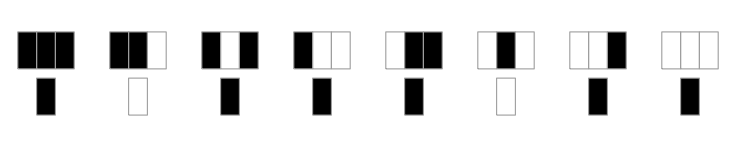

```mathematica
RulePlot[CellularAutomaton[{187,2,1}]]
```

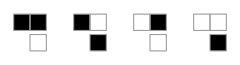

```mathematica
RulePlot[CellularAutomaton[{5,2,1/2}]]
```

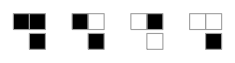

```mathematica
RulePlot[CellularAutomaton[{13,2,1/2}]]
```

```mathematica
-Graphics--Graphics-
```

### All decompositions of ECA 187

```mathematica
DecomposeCA[{187,2,1},0.5]
Map[First[#]&,%%,{2}]
```

{{{5,2,0.5},{4,2,0.5}},{{13,2,0.5},{4,2,0.5}},{{13,2,0.5},{5,2,0.5}},{{11,2,0.5},{10,2,0.5}},{{10,2,0.5},{11,2,0.5}},{{11,2,0.5},{11,2,0.5}}}

{{5,4},{13,4},{13,5},{11,10},{10,11},{11,11}}

```mathematica
DecomposeCA[{187,2,1},0.5]
Map[{First[#],Last[#]}&,%,{2}]
```

{{{5,2,0.5},{4,2,0.5}},{{13,2,0.5},{4,2,0.5}},{{13,2,0.5},{5,2,0.5}},{{11,2,0.5},{10,2,0.5}},{{10,2,0.5},{11,2,0.5}},{{11,2,0.5},{11,2,0.5}}}

{{{5,0.5},{4,0.5}},{{13,0.5},{4,0.5}},{{13,0.5},{5,0.5}},{{11,0.5},{10,0.5}},{{10,0.5},{11,0.5}},{{11,0.5},{11,0.5}}}

```mathematica
CompositeRule[##,2]&/@%
```

{{187,2,1},{187,2,1},{187,2,1},{187,2,1},{187,2,1},{187,2,1}}

## Meaning

### Composition of ECA 184 with itself (184∘184) ⇒ {3099572352, 2, 2}

```mathematica
CompositeRule[{184,1},{184,1},2]
```

{3099572352,2,2}

```mathematica
BFConservativeQ[Sequence@@%]
BFConservativeQ[Apply[Sequence,%%]]
```

True

True

```mathematica
Module[{icAux=RandomInteger[{0,1},100]},
Print@GraphicsRow@{ArrayPlot[
NestList[
CellularAutomaton[{184,2,1},
CellularAutomaton[{184,2,1},#]]&,
icAux,50]],
ArrayPlot[CellularAutomaton[{3099572352,2,2},icAux,50]]}]
```

-Graphics-

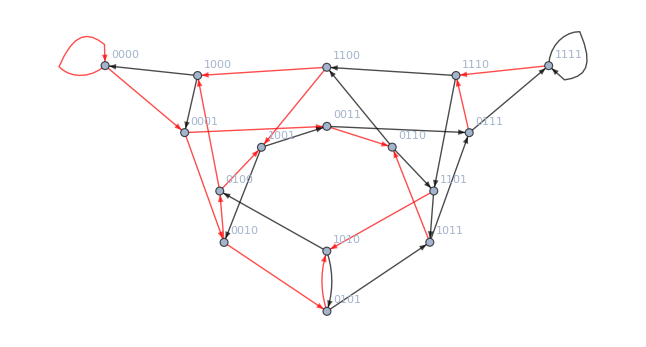

```mathematica
RuleDeBruijnGraph[3099572352,2,2]
```

### All decompositions of 184∘184

```mathematica
DecomposeCA[{3099572352,2,2},1]
```

{{{29,2,1},{71,2,1}},{{184,2,1},{184,2,1}}}

```mathematica
CompositeRule[{29,1},{71,1},2]
CompositeRule[{184,1},{184,1},2]
```

{3099572352,2,2}

{3099572352,2,2}

## Some properties

### Composition is generally noncommutative

```mathematica
DecomposeCA[{3099572352,2,2},1]
```

{{{29,2,1},{71,2,1}},{{184,2,1},{184,2,1}}}

```mathematica
CompositeRule[{29,1},{71,1},2]==CompositeRule[{71,1},{29,1},2]
```

False

```mathematica
CompositeRule[{12,1},{208,1},2]==CompositeRule[{208,1},{12,1},2]
```

True

### Question 1: Which are the non-trivial commutative and the non-commutative compositions of the elementary space?

```mathematica
nonTrivialCommutativeECAPairs=Union[Sort/@({#⟦1,1⟧,#⟦2,1⟧}&/@Select[{{#⟦1⟧,1},{#⟦2⟧,1}}&/@Select[Flatten[Outer[List,Range[0,255],Range[0,255]],1],(#⟦1⟧≠#⟦2⟧)&],(CompositeRule[#⟦1⟧,#⟦2⟧,2]==CompositeRule[#⟦2⟧,#⟦1⟧,2])&])]
```

{{0,2},{0,4},{0,6},{0,8},{0,10},{0,12},{0,14},{0,16},{0,18},{0,20},{0,22},{0,24},{0,26},{0,28},{0,30},{0,32},{0,34},{0,36},{0,38},{0,40},{0,42},{0,44},{0,46},{0,48},{0,50},{0,52},{0,54},{0,56},{0,58},{0,60},{0,62},{0,64},{0,66},{0,68},{0,70},{0,72},{0,74},{0,76},{0,78},{0,80},{0,82},{0,84},{0,86},{0,88},{0,90},{0,92},{0,94},{0,96},{0,98},{0,100},{0,102},{0,104},{0,106},{0,108},{0,110},{0,112},{0,114},{0,116},{0,118},{0,120},{0,122},{0,124},{0,126},{0,128},{0,130},{0,132},{0,134},{0,136},{0,138},{0,140},{0,142},{0,144},{0,146},{0,148},{0,150},{0,152},{0,154},{0,156},{0,158},{0,160},{0,162},{0,164},{0,166},{0,168},{0,170},{0,172},{0,174},{0,176},{0,178},{0,180},{0,182},{0,184},{0,186},{0,188},{0,190},{0,192},{0,194},{0,196},{0,198},{0,200},{0,202},{0,204},{0,206},{0,208},{0,210},{0,212},{0,214},{0,216},{0,218},{0,220},{0,222},{0,224},{0,226},{0,228},{0,230},{0,232},{0,234},{0,236},{0,238},{0,240},{0,242},{0,244},{0,246},{0,248},{0,250},{0,252},{0,254},{1,170},{1,204},{1,236},{1,240},{2,170},{2,172},{2,204},{2,236},{2,240},{3,17},{3,170},{3,204},{3,236},{3,240},{4,42},{4,112},{4,170},{4,200},{4,204},{4,232},{4,240},{5,170},{5,204},{5,240},{6,170},{6,204},{6,240},{7,170},{7,204},{7,240},{8,32},{8,42},{8,64},{8,170},{8,204},{8,240},{9,170},{9,204},{9,240},{10,170},{10,204},{10,240},{11,170},{11,204},{11,240},{12,34},{12,42},{12,140},{12,170},{12,204},{12,208},{12,240},{13,170},{13,204},{13,240},{14,142},{14,170},{14,204},{14,240},{15,23},{15,43},{15,51},{15,77},{15,85},{15,105},{15,113},{15,142},{15,150},{15,170},{15,178},{15,204},{15,212},{15,232},{15,240},{16,170},{16,204},{16,228},{16,236},{16,240},{17,170},{17,204},{17,236},{17,240},{18,170},{18,204},{18,240},{19,170},{19,204},{19,240},{20,170},{20,204},{20,240},{21,170},{21,204},{21,240},{22,170},{22,204},{22,240},{23,51},{23,85},{23,170},{23,204},{23,232},{23,240},{24,170},{24,204},{24,240},{25,170},{25,204},{25,240},{26,170},{26,204},{26,240},{27,170},{27,204},{27,240},{28,170},{28,204},{28,240},{29,170},{29,204},{29,240},{30,170},{30,204},{30,240},{31,170},{31,204},{31,240},{32,64},{32,128},{32,136},{32,170},{32,192},{32,204},{32,232},{32,240},{33,170},{33,204},{33,240},{34,42},{34,140},{34,170},{34,204},{34,208},{34,240},{35,170},{35,204},{35,240},{36,170},{36,204},{36,240},{37,170},{37,204},{37,240},{38,170},{38,204},{38,240},{39,170},{39,204},{39,240},{40,170},{40,204},{40,240},{41,170},{41,204},{41,240},{42,170},{42,200},{42,204},{42,208},{42,212},{42,240},{43,51},{43,85},{43,170},{43,204},{43,212},{43,240},{44,170},{44,204},{44,240},{45,170},{45,204},{45,240},{46,170},{46,204},{46,240},{47,170},{47,204},{47,240},{48,68},{48,112},{48,138},{48,170},{48,196},{48,204},{48,240},{49,170},{49,204},{49,240},{50,170},{50,178},{50,204},{50,240},{51,77},{51,85},{51,105},{51,113},{51,142},{51,150},{51,170},{51,178},{51,204},{51,212},{51,232},{51,240},{52,170},{52,204},{52,240},{53,170},{53,204},{53,240},{54,170},{54,204},{54,240},{55,170},{55,204},{55,240},{56,170},{56,204},{56,240},{57,170},{57,204},{57,240},{58,170},{58,204},{58,240},{59,170},{59,204},{59,240},{60,90},{60,102},{60,150},{60,170},{60,204},{60,240},{61,170},{61,204},{61,240},{62,170},{62,204},{62,240},{63,119},{63,170},{63,200},{63,204},{63,240},{64,112},{64,170},{64,204},{64,240},{65,170},{65,204},{65,240},{66,170},{66,204},{66,240},{67,170},{67,204},{67,240},{68,112},{68,138},{68,170},{68,196},{68,204},{68,240},{69,170},{69,204},{69,240},{70,170},{70,204},{70,240},{71,170},{71,204},{71,240},{72,170},{72,204},{72,240},{73,170},{73,204},{73,240},{74,170},{74,204},{74,240},{75,170},{75,204},{75,240},{76,170},{76,178},{76,204},{76,240},{77,85},{77,170},{77,178},{77,204},{77,240},{78,170},{78,204},{78,240},{79,170},{79,204},{79,240},{80,170},{80,204},{80,240},{81,170},{81,204},{81,240},{82,170},{82,204},{82,240},{83,170},{83,204},{83,240},{84,170},{84,204},{84,212},{84,240},{85,105},{85,113},{85,142},{85,150},{85,170},{85,178},{85,204},{85,212},{85,232},{85,240},{86,170},{86,204},{86,240},{87,170},{87,204},{87,240},{88,170},{88,204},{88,240},{89,170},{89,204},{89,240},{90,102},{90,150},{90,170},{90,204},{90,240},{91,170},{91,204},{91,240},{92,170},{92,204},{92,240},{93,170},{93,204},{93,240},{94,170},{94,204},{94,240},{95,170},{95,204},{95,240},{96,170},{96,204},{96,240},{97,170},{97,204},{97,240},{98,170},{98,204},{98,240},{99,170},{99,204},{99,240},{100,170},{100,204},{100,240},{101,170},{101,204},{101,240},{102,150},{102,170},{102,204},{102,240},{103,170},{103,204},{103,240},{104,170},{104,204},{104,240},{105,150},{105,170},{105,204},{105,240},{106,170},{106,204},{106,240},{107,170},{107,204},{107,240},{108,170},{108,204},{108,240},{109,170},{109,204},{109,240},{110,170},{110,204},{110,240},{111,170},{111,204},{111,240},{112,138},{112,142},{112,170},{112,200},{112,204},{112,240},{113,142},{113,170},{113,204},{113,240},{114,170},{114,204},{114,240},{115,170},{115,204},{115,240},{116,170},{116,204},{116,240},{117,170},{117,204},{117,240},{118,170},{118,204},{118,240},{119,170},{119,200},{119,204},{119,240},{120,170},{120,204},{120,240},{121,170},{121,204},{121,240},{122,170},{122,204},{122,240},{123,170},{123,204},{123,240},{124,170},{124,204},{124,240},{125,170},{125,204},{125,240},{126,170},{126,204},{126,240},{127,170},{127,200},{127,204},{127,240},{128,136},{128,160},{128,170},{128,192},{128,204},{128,240},{128,255},{129,170},{129,204},{129,240},{129,255},{130,170},{130,204},{130,240},{130,255},{131,170},{131,204},{131,240},{131,255},{132,170},{132,204},{132,240},{132,255},{133,170},{133,204},{133,240},{133,255},{134,170},{134,204},{134,240},{134,255},{135,170},{135,204},{135,240},{135,255},{136,160},{136,170},{136,192},{136,204},{136,240},{136,255},{137,170},{137,204},{137,240},{137,255},{138,170},{138,204},{138,240},{138,255},{139,170},{139,204},{139,240},{139,255},{140,170},{140,204},{140,240},{140,255},{141,170},{141,204},{141,240},{141,255},{142,143},{142,170},{142,204},{142,240},{142,241},{142,255},{143,170},{143,204},{143,240},{143,255},{144,170},{144,204},{144,240},{144,255},{145,170},{145,204},{145,240},{145,255},{146,170},{146,204},{146,240},{146,255},{147,170},{147,204},{147,240},{147,255},{148,170},{148,204},{148,240},{148,255},{149,170},{149,204},{149,240},{149,255},{150,153},{150,165},{150,170},{150,195},{150,204},{150,240},{150,255},{151,170},{151,204},{151,240},{151,255},{152,170},{152,204},{152,240},{152,255},{153,165},{153,170},{153,195},{153,204},{153,240},{153,255},{154,170},{154,204},{154,240},{154,255},{155,170},{155,204},{155,240},{155,255},{156,170},{156,204},{156,240},{156,255},{157,170},{157,204},{157,240},{157,255},{158,170},{158,204},{158,240},{158,255},{159,170},{159,204},{159,240},{159,255},{160,170},{160,192},{160,204},{160,240},{160,255},{161,170},{161,204},{161,240},{161,255},{162,170},{162,204},{162,240},{162,255},{163,170},{163,204},{163,240},{163,255},{164,170},{164,204},{164,240},{164,255},{165,170},{165,195},{165,204},{165,240},{165,255},{166,170},{166,204},{166,240},{166,255},{167,170},{167,204},{167,240},{167,255},{168,170},{168,204},{168,224},{168,240},{168,255},{169,170},{169,204},{169,240},{169,255},{170,171},{170,172},{170,173},{170,174},{170,175},{170,176},{170,177},{170,178},{170,179},{170,180},{170,181},{170,182},{170,183},{170,184},{170,185},{170,186},{170,187},{170,188},{170,189},{170,190},{170,191},{170,192},{170,193},{170,194},{170,195},{170,196},{170,197},{170,198},{170,199},{170,200},{170,201},{170,202},{170,203},{170,204},{170,205},{170,206},{170,207},{170,208},{170,209},{170,210},{170,211},{170,212},{170,213},{170,214},{170,215},{170,216},{170,217},{170,218},{170,219},{170,220},{170,221},{170,222},{170,223},{170,224},{170,225},{170,226},{170,227},{170,228},{170,229},{170,230},{170,231},{170,232},{170,233},{170,234},{170,235},{170,236},{170,237},{170,238},{170,239},{170,240},{170,241},{170,242},{170,243},{170,244},{170,245},{170,246},{170,247},{170,248},{170,249},{170,250},{170,251},{170,252},{170,253},{170,254},{170,255},{171,187},{171,204},{171,207},{171,212},{171,223},{171,236},{171,239},{171,240},{171,244},{171,255},{172,204},{172,240},{172,255},{173,204},{173,240},{173,255},{174,204},{174,221},{174,240},{174,241},{174,243},{174,255},{175,204},{175,240},{175,255},{176,204},{176,240},{176,255},{177,204},{177,240},{177,255},{178,179},{178,204},{178,205},{178,240},{178,255},{179,204},{179,240},{179,255},{180,204},{180,240},{180,255},{181,204},{181,240},{181,255},{182,204},{182,240},{182,255},{183,204},{183,240},{183,255},{184,204},{184,240},{184,255},{185,204},{185,240},{185,255},{186,204},{186,240},{186,255},{187,204},{187,206},{187,207},{187,240},{187,244},{187,255},{188,204},{188,240},{188,255},{189,204},{189,240},{189,255},{190,204},{190,240},{190,255},{191,200},{191,202},{191,204},{191,240},{191,255},{192,204},{192,240},{192,255},{193,204},{193,240},{193,255},{194,204},{194,240},{194,255},{195,204},{195,240},{195,255},{196,204},{196,240},{196,255},{197,204},{197,240},{197,255},{198,204},{198,240},{198,255},{199,204},{199,240},{199,255},{200,204},{200,240},{200,247},{200,255},{201,204},{201,240},{201,255},{202,204},{202,240},{202,255},{203,204},{203,240},{203,255},{204,205},{204,206},{204,207},{204,208},{204,209},{204,210},{204,211},{204,212},{204,213},{204,214},{204,215},{204,216},{204,217},{204,218},{204,219},{204,220},{204,221},{204,222},{204,223},{204,224},{204,225},{204,226},{204,227},{204,228},{204,229},{204,230},{204,231},{204,232},{204,233},{204,234},{204,235},{204,236},{204,237},{204,238},{204,239},{204,240},{204,241},{204,242},{204,243},{204,244},{204,245},{204,246},{204,247},{204,248},{204,249},{204,250},{204,251},{204,252},{204,253},{204,254},{204,255},{205,240},{205,255},{206,207},{206,240},{206,255},{207,240},{207,244},{207,255},{208,240},{208,255},{209,240},{209,255},{210,240},{210,255},{211,240},{211,255},{212,213},{212,240},{212,255},{213,240},{213,255},{214,240},{214,255},{215,240},{215,255},{216,240},{216,247},{216,255},{217,240},{217,255},{218,240},{218,255},{219,240},{219,255},{220,221},{220,240},{220,243},{220,255},{221,240},{221,241},{221,243},{221,255},{222,240},{222,255},{223,232},{223,236},{223,240},{223,241},{223,255},{224,240},{224,255},{225,240},{225,255},{226,240},{226,255},{227,240},{227,255},{228,240},{228,255},{229,240},{229,255},{230,240},{230,255},{231,240},{231,255},{232,240},{232,251},{232,255},{233,240},{233,255},{234,240},{234,248},{234,255},{235,240},{235,255},{236,240},{236,241},{236,255},{237,240},{237,255},{238,240},{238,250},{238,251},{238,252},{238,254},{238,255},{239,240},{239,251},{239,253},{239,255},{240,241},{240,242},{240,243},{240,244},{240,245},{240,246},{240,247},{240,248},{240,249},{240,250},{240,251},{240,252},{240,253},{240,254},{240,255},{241,243},{241,253},{241,255},{242,255},{243,255},{244,255},{245,255},{246,255},{247,255},{248,255},{249,255},{250,252},{250,254},{250,255},{251,252},{251,253},{251,254},{251,255},{252,254},{252,255},{253,255},{254,255}}

```mathematica
Length@%
```

1164

```mathematica
noncommutativeECAPairs=Union[Sort/@({#⟦1,1⟧,#⟦2,1⟧}&/@Select[{{#⟦1⟧,1},{#⟦2⟧,1}}&/@Select[Flatten[Outer[List,Range[0,255],Range[0,255]],1],(#⟦1⟧≠#⟦2⟧)&],(CompositeRule[#⟦1⟧,#⟦2⟧,2]≠CompositeRule[#⟦2⟧,#⟦1⟧,2])&])]
```

{{0,1},{0,3},{0,5},{0,7},{0,9},{0,11},{0,13},{0,15},{0,17},{0,19},{0,21},{0,23},{0,25},{0,27},{0,29},{0,31},{0,33},{0,35},{0,37},{0,39},{0,41},{0,43},{0,45},{0,47},{0,49},{0,51},{0,53},{0,55},{0,57},{0,59},{0,61},{0,63},{0,65},{0,67},{0,69},{0,71},{0,73},{0,75},{0,77},{0,79},{0,81},{0,83},{0,85},{0,87},{0,89},{0,91},{0,93},{0,95},{0,97},{0,99},{0,101},{0,103},{0,105},{0,107},{0,109},{0,111},{0,113},{0,115},{0,117},{0,119},{0,121},{0,123},{0,125},{0,127},{0,129},{0,131},{0,133},{0,135},{0,137},{0,139},{0,141},{0,143},{0,145},{0,147},{0,149},{0,151},{0,153},{0,155},{0,157},{0,159},{0,161},{0,163},{0,165},{0,167},{0,169},{0,171},{0,173},{0,175},{0,177},{0,179},{0,181},{0,183},{0,185},{0,187},{0,189},{0,191},{0,193},{0,195},{0,197},{0,199},{0,201},{0,203},{0,205},{0,207},{0,209},{0,211},{0,213},{0,215},{0,217},{0,219},{0,221},{0,223},{0,225},{0,227},{0,229},{0,231},{0,233},{0,235},{0,237},{0,239},{0,241},{0,243},{0,245},{0,247},{0,249},{0,251},{0,253},{0,255},{1,2},{1,3},{1,4},{1,5},{1,6},{1,7},{1,8},{1,9},{1,10},{1,11},{1,12},{1,13},{1,14},{1,15},{1,16},{1,17},{1,18},{1,19},{1,20},{1,21},{1,22},{1,23},{1,24},{1,25},{1,26},{1,27},{1,28},{1,29},{1,30},{1,31},{1,32},{1,33},{1,34},{1,35},{1,36},{1,37},{1,38},{1,39},{1,40},{1,41},{1,42},{1,43},{1,44},{1,45},{1,46},{1,47},{1,48},{1,49},{1,50},{1,51},{1,52},{1,53},{1,54},{1,55},{1,56},{1,57},{1,58},{1,59},{1,60},{1,61},{1,62},{1,63},{1,64},{1,65},{1,66},{1,67},{1,68},{1,69},{1,70},{1,71},{1,72},{1,73},{1,74},{1,75},{1,76},{1,77},{1,78},{1,79},{1,80},{1,81},{1,82},{1,83},{1,84},{1,85},{1,86},{1,87},{1,88},{1,89},{1,90},{1,91},{1,92},{1,93},{1,94},{1,95},{1,96},{1,97},{1,98},{1,99},{1,100},{1,101},{1,102},{1,103},{1,104},{1,105},{1,106},{1,107},{1,108},{1,109},{1,110},{1,111},{1,112},{1,113},{1,114},{1,115},{1,116},{1,117},{1,118},{1,119},{1,120},{1,121},{1,122},{1,123},{1,124},{1,125},{1,126},{1,127},{1,128},{1,129},{1,130},{1,131},{1,132},{1,133},{1,134},{1,135},{1,136},{1,137},{1,138},{1,139},{1,140},{1,141},{1,142},{1,143},{1,144},{1,145},{1,146},{1,147},{1,148},{1,149},{1,150},{1,151},{1,152},{1,153},{1,154},{1,155},{1,156},{1,157},{1,158},{1,159},{1,160},{1,161},{1,162},{1,163},{1,164},{1,165},{1,166},{1,167},{1,168},{1,169},{1,171},{1,172},{1,173},{1,174},{1,175},{1,176},{1,177},{1,178},{1,179},{1,180},{1,181},{1,182},{1,183},{1,184},{1,185},{1,186},{1,187},{1,188},{1,189},{1,190},{1,191},{1,192},{1,193},{1,194},{1,195},{1,196},{1,197},{1,198},{1,199},{1,200},{1,201},{1,202},{1,203},{1,205},{1,206},{1,207},{1,208},{1,209},{1,210},{1,211},{1,212},{1,213},{1,214},{1,215},{1,216},{1,217},{1,218},{1,219},{1,220},{1,221},{1,222},{1,223},{1,224},{1,225},{1,226},{1,227},{1,228},{1,229},{1,230},{1,231},{1,232},{1,233},{1,234},{1,235},{1,237},{1,238},{1,239},{1,241},{1,242},{1,243},{1,244},{1,245},{1,246},{1,247},{1,248},{1,249},{1,250},{1,251},{1,252},{1,253},{1,254},{1,255},{2,3},{2,4},{2,5},{2,6},{2,7},{2,8},{2,9},{2,10},{2,11},{2,12},{2,13},{2,14},{2,15},{2,16},{2,17},{2,18},{2,19},{2,20},{2,21},{2,22},{2,23},{2,24},{2,25},{2,26},{2,27},{2,28},{2,29},{2,30},{2,31},{2,32},{2,33},{2,34},{2,35},{2,36},{2,37},{2,38},{2,39},{2,40},{2,41},{2,42},{2,43},{2,44},{2,45},{2,46},{2,47},{2,48},{2,49},{2,50},{2,51},{2,52},{2,53},{2,54},{2,55},{2,56},{2,57},{2,58},{2,59},{2,60},{2,61},{2,62},{2,63},{2,64},{2,65},{2,66},{2,67},{2,68},{2,69},{2,70},{2,71},{2,72},{2,73},{2,74},{2,75},{2,76},{2,77},{2,78},{2,79},{2,80},{2,81},{2,82},{2,83},{2,84},{2,85},{2,86},{2,87},{2,88},{2,89},{2,90},{2,91},{2,92},{2,93},{2,94},{2,95},{2,96},{2,97},{2,98},{2,99},{2,100},{2,101},{2,102},{2,103},{2,104},{2,105},{2,106},{2,107},{2,108},{2,109},{2,110},{2,111},{2,112},{2,113},{2,114},{2,115},{2,116},{2,117},{2,118},{2,119},{2,120},{2,121},{2,122},{2,123},{2,124},{2,125},{2,126},{2,127},{2,128},{2,129},{2,130},{2,131},{2,132},{2,133},{2,134},{2,135},{2,136},{2,137},{2,138},{2,139},{2,140},{2,141},{2,142},{2,143},{2,144},{2,145},{2,146},{2,147},{2,148},{2,149},{2,150},{2,151},{2,152},{2,153},{2,154},{2,155},{2,156},{2,157},{2,158},{2,159},{2,160},{2,161},{2,162},{2,163},{2,164},{2,165},{2,166},{2,167},{2,168},{2,169},{2,171},{2,173},{2,174},{2,175},{2,176},{2,177},{2,178},{2,179},{2,180},{2,181},{2,182},{2,183},{2,184},{2,185},{2,186},{2,187},{2,188},{2,189},{2,190},{2,191},{2,192},{2,193},{2,194},{2,195},{2,196},{2,197},{2,198},{2,199},{2,200},{2,201},{2,202},{2,203},{2,205},{2,206},{2,207},{2,208},{2,209},{2,210},{2,211},{2,212},{2,213},{2,214},{2,215},{2,216},{2,217},{2,218},{2,219},{2,220},{2,221},{2,222},{2,223},{2,224},{2,225},{2,226},{2,227},{2,228},{2,229},{2,230},{2,231},{2,232},{2,233},{2,234},{2,235},{2,237},{2,238},{2,239},{2,241},{2,242},{2,243},{2,244},{2,245},{2,246},{2,247},{2,248},{2,249},{2,250},{2,251},{2,252},{2,253},{2,254},{2,255},{3,4},{3,5},{3,6},{3,7},{3,8},{3,9},{3,10},{3,11},{3,12},{3,13},{3,14},{3,15},{3,16},{3,18},{3,19},{3,20},{3,21},{3,22},{3,23},{3,24},{3,25},{3,26},{3,27},{3,28},{3,29},{3,30},{3,31},{3,32},{3,33},{3,34},{3,35},{3,36},{3,37},{3,38},{3,39},{3,40},{3,41},{3,42},{3,43},{3,44},{3,45},{3,46},{3,47},{3,48},{3,49},{3,50},{3,51},{3,52},{3,53},{3,54},{3,55},{3,56},{3,57},{3,58},{3,59},{3,60},{3,61},{3,62},{3,63},{3,64},{3,65},{3,66},{3,67},{3,68},{3,69},{3,70},{3,71},{3,72},{3,73},{3,74},{3,75},{3,76},{3,77},{3,78},{3,79},{3,80},{3,81},{3,82},{3,83},{3,84},{3,85},{3,86},{3,87},{3,88},{3,89},{3,90},{3,91},{3,92},{3,93},{3,94},{3,95},{3,96},{3,97},{3,98},{3,99},{3,100},{3,101},{3,102},{3,103},{3,104},{3,105},{3,106},{3,107},{3,108},{3,109},{3,110},{3,111},{3,112},{3,113},{3,114},{3,115},{3,116},{3,117},{3,118},{3,119},{3,120},{3,121},{3,122},{3,123},{3,124},{3,125},{3,126},{3,127},{3,128},{3,129},{3,130},{3,131},{3,132},{3,133},{3,134},{3,135},{3,136},{3,137},{3,138},{3,139},{3,140},{3,141},{3,142},{3,143},{3,144},{3,145},{3,146},{3,147},{3,148},{3,149},{3,150},{3,151},{3,152},{3,153},{3,154},{3,155},{3,156},{3,157},{3,158},{3,159},{3,160},{3,161},{3,162},{3,163},{3,164},{3,165},{3,166},{3,167},{3,168},{3,169},{3,171},{3,172},{3,173},{3,174},{3,175},{3,176},{3,177},{3,178},{3,179},{3,180},{3,181},{3,182},{3,183},{3,184},{3,185},{3,186},{3,187},{3,188},{3,189},{3,190},{3,191},{3,192},{3,193},{3,194},{3,195},{3,196},{3,197},{3,198},{3,199},{3,200},{3,201},{3,202},{3,203},{3,205},{3,206},{3,207},{3,208},{3,209},{3,210},{3,211},{3,212},{3,213},{3,214},{3,215},{3,216},{3,217},{3,218},{3,219},{3,220},{3,221},{3,222},{3,223},{3,224},{3,225},{3,226},{3,227},{3,228},{3,229},{3,230},{3,231},{3,232},{3,233},{3,234},{3,235},{3,237},{3,238},{3,239},{3,241},{3,242},{3,243},{3,244},{3,245},{3,246},{3,247},{3,248},{3,249},{3,250},{3,251},{3,252},{3,253},{3,254},{3,255},{4,5},{4,6},{4,7},{4,8},{4,9},{4,10},{4,11},{4,12},{4,13},{4,14},{4,15},{4,16},{4,17},{4,18},{4,19},{4,20},{4,21},{4,22},{4,23},{4,24},{4,25},{4,26},{4,27},{4,28},{4,29},{4,30},{4,31},{4,32},{4,33},{4,34},{4,35},{4,36},{4,37},{4,38},{4,39},{4,40},{4,41},{4,43},{4,44},{4,45},{4,46},{4,47},{4,48},{4,49},{4,50},{4,51},{4,52},{4,53},{4,54},{4,55},{4,56},{4,57},{4,58},{4,59},{4,60},{4,61},{4,62},{4,63},{4,64},{4,65},{4,66},{4,67},{4,68},{4,69},{4,70},{4,71},{4,72},{4,73},{4,74},{4,75},{4,76},{4,77},{4,78},{4,79},{4,80},{4,81},{4,82},{4,83},{4,84},{4,85},{4,86},{4,87},{4,88},{4,89},{4,90},{4,91},{4,92},{4,93},{4,94},{4,95},{4,96},{4,97},{4,98},{4,99},{4,100},{4,101},{4,102},{4,103},{4,104},{4,105},{4,106},{4,107},{4,108},{4,109},{4,110},{4,111},{4,113},{4,114},{4,115},{4,116},{4,117},{4,118},{4,119},{4,120},{4,121},{4,122},{4,123},{4,124},{4,125},{4,126},{4,127},{4,128},{4,129},{4,130},{4,131},{4,132},{4,133},{4,134},{4,135},{4,136},{4,137},{4,138},{4,139},{4,140},{4,141},{4,142},{4,143},{4,144},{4,145},{4,146},{4,147},{4,148},{4,149},{4,150},{4,151},{4,152},{4,153},{4,154},{4,155},{4,156},{4,157},{4,158},{4,159},{4,160},{4,161},{4,162},{4,163},{4,164},{4,165},{4,166},{4,167},{4,168},{4,169},{4,171},{4,172},{4,173},{4,174},{4,175},{4,176},{4,177},{4,178},{4,179},{4,180},{4,181},{4,182},{4,183},{4,184},{4,185},{4,186},{4,187},{4,188},{4,189},{4,190},{4,191},{4,192},{4,193},{4,194},{4,195},{4,196},{4,197},{4,198},{4,199},{4,201},{4,202},{4,203},{4,205},{4,206},{4,207},{4,208},{4,209},{4,210},{4,211},{4,212},{4,213},{4,214},{4,215},{4,216},{4,217},{4,218},{4,219},{4,220},{4,221},{4,222},{4,223},{4,224},{4,225},{4,226},{4,227},{4,228},{4,229},{4,230},{4,231},{4,233},{4,234},{4,235},{4,236},{4,237},{4,238},{4,239},{4,241},{4,242},{4,243},{4,244},{4,245},{4,246},{4,247},{4,248},{4,249},{4,250},{4,251},{4,252},{4,253},{4,254},{4,255},{5,6},{5,7},{5,8},{5,9},{5,10},{5,11},{5,12},{5,13},{5,14},{5,15},{5,16},{5,17},{5,18},{5,19},{5,20},{5,21},{5,22},{5,23},{5,24},{5,25},{5,26},{5,27},{5,28},{5,29},{5,30},{5,31},{5,32},{5,33},{5,34},{5,35},{5,36},{5,37},{5,38},{5,39},{5,40},{5,41},{5,42},{5,43},{5,44},{5,45},{5,46},{5,47},{5,48},{5,49},{5,50},{5,51},{5,52},{5,53},{5,54},{5,55},{5,56},{5,57},{5,58},{5,59},{5,60},{5,61},{5,62},{5,63},{5,64},{5,65},{5,66},{5,67},{5,68},{5,69},{5,70},{5,71},{5,72},{5,73},{5,74},{5,75},{5,76},{5,77},{5,78},{5,79},{5,80},{5,81},{5,82},{5,83},{5,84},{5,85},{5,86},{5,87},{5,88},{5,89},{5,90},{5,91},{5,92},{5,93},{5,94},{5,95},{5,96},{5,97},{5,98},{5,99},{5,100},{5,101},{5,102},{5,103},{5,104},{5,105},{5,106},{5,107},{5,108},{5,109},{5,110},{5,111},{5,112},{5,113},{5,114},{5,115},{5,116},{5,117},{5,118},{5,119},{5,120},{5,121},{5,122},{5,123},{5,124},{5,125},{5,126},{5,127},{5,128},{5,129},{5,130},{5,131},{5,132},{5,133},{5,134},{5,135},{5,136},{5,137},{5,138},{5,139},{5,140},{5,141},{5,142},{5,143},{5,144},{5,145},{5,146},{5,147},{5,148},{5,149},{5,150},{5,151},{5,152},{5,153},{5,154},{5,155},{5,156},{5,157},{5,158},{5,159},{5,160},{5,161},{5,162},{5,163},{5,164},{5,165},{5,166},{5,167},{5,168},{5,169},{5,171},{5,172},{5,173},{5,174},{5,175},{5,176},{5,177},{5,178},{5,179},{5,180},{5,181},{5,182},{5,183},{5,184},{5,185},{5,186},{5,187},{5,188},{5,189},{5,190},{5,191},{5,192},{5,193},{5,194},{5,195},{5,196},{5,197},{5,198},{5,199},{5,200},{5,201},{5,202},{5,203},{5,205},{5,206},{5,207},{5,208},{5,209},{5,210},{5,211},{5,212},{5,213},{5,214},{5,215},{5,216},{5,217},{5,218},{5,219},{5,220},{5,221},{5,222},{5,223},{5,224},{5,225},{5,226},{5,227},{5,228},{5,229},{5,230},{5,231},{5,232},{5,233},{5,234},{5,235},{5,236},{5,237},{5,238},{5,239},{5,241},{5,242},{5,243},{5,244},{5,245},{5,246},{5,247},{5,248},{5,249},{5,250},{5,251},{5,252},{5,253},{5,254},{5,255},{6,7},{6,8},{6,9},{6,10},{6,11},{6,12},{6,13},{6,14},{6,15},{6,16},{6,17},{6,18},{6,19},{6,20},{6,21},{6,22},{6,23},{6,24},{6,25},{6,26},{6,27},{6,28},{6,29},{6,30},{6,31},{6,32},{6,33},{6,34},{6,35},{6,36},{6,37},{6,38},{6,39},{6,40},{6,41},{6,42},{6,43},{6,44},{6,45},{6,46},{6,47},{6,48},{6,49},{6,50},{6,51},{6,52},{6,53},{6,54},{6,55},{6,56},{6,57},{6,58},{6,59},{6,60},{6,61},{6,62},{6,63},{6,64},{6,65},{6,66},{6,67},{6,68},{6,69},{6,70},{6,71},{6,72},{6,73},{6,74},{6,75},{6,76},{6,77},{6,78},{6,79},{6,80},{6,81},{6,82},{6,83},{6,84},{6,85},{6,86},{6,87},{6,88},{6,89},{6,90},{6,91},{6,92},{6,93},{6,94},{6,95},{6,96},{6,97},{6,98},{6,99},{6,100},{6,101},{6,102},{6,103},{6,104},{6,105},{6,106},{6,107},{6,108},{6,109},{6,110},{6,111},{6,112},{6,113},{6,114},{6,115},{6,116},{6,117},{6,118},{6,119},{6,120},{6,121},{6,122},{6,123},{6,124},{6,125},{6,126},{6,127},{6,128},{6,129},{6,130},{6,131},{6,132},{6,133},{6,134},{6,135},{6,136},{6,137},{6,138},{6,139},{6,140},{6,141},{6,142},{6,143},{6,144},{6,145},{6,146},{6,147},{6,148},{6,149},{6,150},{6,151},{6,152},{6,153},{6,154},{6,155},{6,156},{6,157},{6,158},{6,159},{6,160},{6,161},{6,162},{6,163},{6,164},{6,165},{6,166},{6,167},{6,168},{6,169},{6,171},{6,172},{6,173},{6,174},{6,175},{6,176},{6,177},{6,178},{6,179},{6,180},{6,181},{6,182},{6,183},{6,184},{6,185},{6,186},{6,187},{6,188},{6,189},{6,190},{6,191},{6,192},{6,193},{6,194},{6,195},{6,196},{6,197},{6,198},{6,199},{6,200},{6,201},{6,202},{6,203},{6,205},{6,206},{6,207},{6,208},{6,209},{6,210},{6,211},{6,212},{6,213},{6,214},{6,215},{6,216},{6,217},{6,218},{6,219},{6,220},{6,221},{6,222},{6,223},{6,224},{6,225},{6,226},{6,227},{6,228},{6,229},{6,230},{6,231},{6,232},{6,233},{6,234},{6,235},{6,236},{6,237},{6,238},{6,239},{6,241},{6,242},{6,243},{6,244},{6,245},{6,246},{6,247},{6,248},{6,249},{6,250},{6,251},{6,252},{6,253},{6,254},{6,255},{7,8},{7,9},{7,10},{7,11},{7,12},{7,13},{7,14},{7,15},{7,16},{7,17},{7,18},{7,19},{7,20},{7,21},{7,22},{7,23},{7,24},{7,25},{7,26},{7,27},{7,28},{7,29},{7,30},{7,31},{7,32},{7,33},{7,34},{7,35},{7,36},{7,37},{7,38},{7,39},{7,40},{7,41},{7,42},{7,43},{7,44},{7,45},{7,46},{7,47},{7,48},{7,49},{7,50},{7,51},{7,52},{7,53},{7,54},{7,55},{7,56},{7,57},{7,58},{7,59},{7,60},{7,61},{7,62},{7,63},{7,64},{7,65},{7,66},{7,67},{7,68},{7,69},{7,70},{7,71},{7,72},{7,73},{7,74},{7,75},{7,76},{7,77},{7,78},{7,79},{7,80},{7,81},{7,82},{7,83},{7,84},{7,85},{7,86},{7,87},{7,88},{7,89},{7,90},{7,91},{7,92},{7,93},{7,94},{7,95},{7,96},{7,97},{7,98},{7,99},{7,100},{7,101},{7,102},{7,103},{7,104},{7,105},{7,106},{7,107},{7,108},{7,109},{7,110},{7,111},{7,112},{7,113},{7,114},{7,115},{7,116},{7,117},{7,118},{7,119},{7,120},{7,121},{7,122},{7,123},{7,124},{7,125},{7,126},{7,127},{7,128},{7,129},{7,130},{7,131},{7,132},{7,133},{7,134},{7,135},{7,136},{7,137},{7,138},{7,139},{7,140},{7,141},{7,142},{7,143},{7,144},{7,145},{7,146},{7,147},{7,148},{7,149},{7,150},{7,151},{7,152},{7,153},{7,154},{7,155},{7,156},{7,157},{7,158},{7,159},{7,160},{7,161},{7,162},{7,163},{7,164},{7,165},{7,166},{7,167},{7,168},{7,169},{7,171},{7,172},{7,173},{7,174},{7,175},{7,176},{7,177},{7,178},{7,179},{7,180},{7,181},{7,182},{7,183},{7,184},{7,185},{7,186},{7,187},{7,188},{7,189},{7,190},{7,191},{7,192},{7,193},{7,194},{7,195},{7,196},{7,197},{7,198},{7,199},{7,200},{7,201},{7,202},{7,203},{7,205},{7,206},{7,207},{7,208},{7,209},{7,210},{7,211},{7,212},{7,213},{7,214},{7,215},{7,216},{7,217},{7,218},{7,219},{7,220},{7,221},{7,222},{7,223},{7,224},{7,225},{7,226},{7,227},{7,228},{7,229},{7,230},{7,231},{7,232},{7,233},{7,234},{7,235},{7,236},{7,237},{7,238},{7,239},{7,241},{7,242},{7,243},{7,244},{7,245},{7,246},{7,247},{7,248},{7,249},{7,250},{7,251},{7,252},{7,253},{7,254},{7,255},{8,9},{8,10},{8,11},{8,12},{8,13},{8,14},{8,15},{8,16},{8,17},{8,18},{8,19},{8,20},{8,21},{8,22},{8,23},{8,24},{8,25},{8,26},{8,27},{8,28},{8,29},{8,30},{8,31},{8,33},{8,34},{8,35},{8,36},{8,37},{8,38},{8,39},{8,40},{8,41},{8,43},{8,44},{8,45},{8,46},{8,47},{8,48},{8,49},{8,50},{8,51},{8,52},{8,53},{8,54},{8,55},{8,56},{8,57},{8,58},{8,59},{8,60},{8,61},{8,62},{8,63},{8,65},{8,66},{8,67},{8,68},{8,69},{8,70},{8,71},{8,72},{8,73},{8,74},{8,75},{8,76},{8,77},{8,78},{8,79},{8,80},{8,81},{8,82},{8,83},{8,84},{8,85},{8,86},{8,87},{8,88},{8,89},{8,90},{8,91},{8,92},{8,93},{8,94},{8,95},{8,96},{8,97},{8,98},{8,99},{8,100},{8,101},{8,102},{8,103},{8,104},{8,105},{8,106},{8,107},{8,108},{8,109},{8,110},{8,111},{8,112},{8,113},{8,114},{8,115},{8,116},{8,117},{8,118},{8,119},{8,120},{8,121},{8,122},{8,123},{8,124},{8,125},{8,126},{8,127},{8,128},{8,129},{8,130},{8,131},{8,132},{8,133},{8,134},{8,135},{8,136},{8,137},{8,138},{8,139},{8,140},{8,141},{8,142},{8,143},{8,144},{8,145},{8,146},{8,147},{8,148},{8,149},{8,150},{8,151},{8,152},{8,153},{8,154},{8,155},{8,156},{8,157},{8,158},{8,159},{8,160},{8,161},{8,162},{8,163},{8,164},{8,165},{8,166},{8,167},{8,168},{8,169},{8,171},{8,172},{8,173},{8,174},{8,175},{8,176},{8,177},{8,178},{8,179},{8,180},{8,181},{8,182},{8,183},{8,184},{8,185},{8,186},{8,187},{8,188},{8,189},{8,190},{8,191},{8,192},{8,193},{8,194},{8,195},{8,196},{8,197},{8,198},{8,199},{8,200},{8,201},{8,202},{8,203},{8,205},{8,206},{8,207},{8,208},{8,209},{8,210},{8,211},{8,212},{8,213},{8,214},{8,215},{8,216},{8,217},{8,218},{8,219},{8,220},{8,221},{8,222},{8,223},{8,224},{8,225},{8,226},{8,227},{8,228},{8,229},{8,230},{8,231},{8,232},{8,233},{8,234},{8,235},{8,236},{8,237},{8,238},{8,239},{8,241},{8,242},{8,243},{8,244},{8,245},{8,246},{8,247},{8,248},{8,249},{8,250},{8,251},{8,252},{8,253},{8,254},{8,255},{9,10},{9,11},{9,12},{9,13},{9,14},{9,15},{9,16},{9,17},{9,18},{9,19},{9,20},{9,21},{9,22},{9,23},{9,24},{9,25},{9,26},{9,27},{9,28},{9,29},{9,30},{9,31},{9,32},{9,33},{9,34},{9,35},{9,36},{9,37},{9,38},{9,39},{9,40},{9,41},{9,42},{9,43},{9,44},{9,45},{9,46},{9,47},{9,48},{9,49},{9,50},{9,51},{9,52},{9,53},{9,54},{9,55},{9,56},{9,57},{9,58},{9,59},{9,60},{9,61},{9,62},{9,63},{9,64},{9,65},{9,66},{9,67},{9,68},{9,69},{9,70},{9,71},{9,72},{9,73},{9,74},{9,75},{9,76},{9,77},{9,78},{9,79},{9,80},{9,81},{9,82},{9,83},{9,84},{9,85},{9,86},{9,87},{9,88},{9,89},{9,90},{9,91},{9,92},{9,93},{9,94},{9,95},{9,96},{9,97},{9,98},{9,99},{9,100},{9,101},{9,102},{9,103},{9,104},{9,105},{9,106},{9,107},{9,108},{9,109},{9,110},{9,111},{9,112},{9,113},{9,114},{9,115},{9,116},{9,117},{9,118},{9,119},{9,120},{9,121},{9,122},{9,123},{9,124},{9,125},{9,126},{9,127},{9,128},{9,129},{9,130},{9,131},{9,132},{9,133},{9,134},{9,135},{9,136},{9,137},{9,138},{9,139},{9,140},{9,141},{9,142},{9,143},{9,144},{9,145},{9,146},{9,147},{9,148},{9,149},{9,150},{9,151},{9,152},{9,153},{9,154},{9,155},{9,156},{9,157},{9,158},{9,159},{9,160},{9,161},{9,162},{9,163},{9,164},{9,165},{9,166},{9,167},{9,168},{9,169},{9,171},{9,172},{9,173},{9,174},{9,175},{9,176},{9,177},{9,178},{9,179},{9,180},{9,181},{9,182},{9,183},{9,184},{9,185},{9,186},{9,187},{9,188},{9,189},{9,190},{9,191},{9,192},{9,193},{9,194},{9,195},{9,196},{9,197},{9,198},{9,199},{9,200},{9,201},{9,202},{9,203},{9,205},{9,206},{9,207},{9,208},{9,209},{9,210},{9,211},{9,212},{9,213},{9,214},{9,215},{9,216},{9,217},{9,218},{9,219},{9,220},{9,221},{9,222},{9,223},{9,224},{9,225},{9,226},{9,227},{9,228},{9,229},{9,230},{9,231},{9,232},{9,233},{9,234},{9,235},{9,236},{9,237},{9,238},{9,239},{9,241},{9,242},{9,243},{9,244},{9,245},{9,246},{9,247},{9,248},{9,249},{9,250},{9,251},{9,252},{9,253},{9,254},{9,255},{10,11},{10,12},{10,13},{10,14},{10,15},{10,16},{10,17},{10,18},{10,19},{10,20},{10,21},{10,22},{10,23},{10,24},{10,25},{10,26},{10,27},{10,28},{10,29},{10,30},{10,31},{10,32},{10,33},{10,34},{10,35},{10,36},{10,37},{10,38},{10,39},{10,40},{10,41},{10,42},{10,43},{10,44},{10,45},{10,46},{10,47},{10,48},{10,49},{10,50},{10,51},{10,52},{10,53},{10,54},{10,55},{10,56},{10,57},{10,58},{10,59},{10,60},{10,61},{10,62},{10,63},{10,64},{10,65},{10,66},{10,67},{10,68},{10,69},{10,70},{10,71},{10,72},{10,73},{10,74},{10,75},{10,76},{10,77},{10,78},{10,79},{10,80},{10,81},{10,82},{10,83},{10,84},{10,85},{10,86},{10,87},{10,88},{10,89},{10,90},{10,91},{10,92},{10,93},{10,94},{10,95},{10,96},{10,97},{10,98},{10,99},{10,100},{10,101},{10,102},{10,103},{10,104},{10,105},{10,106},{10,107},{10,108},{10,109},{10,110},{10,111},{10,112},{10,113},{10,114},{10,115},{10,116},{10,117},{10,118},{10,119},{10,120},{10,121},{10,122},{10,123},{10,124},{10,125},{10,126},{10,127},{10,128},{10,129},{10,130},{10,131},{10,132},{10,133},{10,134},{10,135},{10,136},{10,137},{10,138},{10,139},{10,140},{10,141},{10,142},{10,143},{10,144},{10,145},{10,146},{10,147},{10,148},{10,149},{10,150},{10,151},{10,152},{10,153},{10,154},{10,155},{10,156},{10,157},{10,158},{10,159},{10,160},{10,161},{10,162},{10,163},{10,164},{10,165},{10,166},{10,167},{10,168},{10,169},{10,171},{10,172},{10,173},{10,174},{10,175},{10,176},{10,177},{10,178},{10,179},{10,180},{10,181},{10,182},{10,183},{10,184},{10,185},{10,186},{10,187},{10,188},{10,189},{10,190},{10,191},{10,192},{10,193},{10,194},{10,195},{10,196},{10,197},{10,198},{10,199},{10,200},{10,201},{10,202},{10,203},{10,205},{10,206},{10,207},{10,208},{10,209},{10,210},{10,211},{10,212},{10,213},{10,214},{10,215},{10,216},{10,217},{10,218},{10,219},{10,220},{10,221},{10,222},{10,223},{10,224},{10,225},{10,226},{10,227},{10,228},{10,229},{10,230},{10,231},{10,232},{10,233},{10,234},{10,235},{10,236},{10,237},{10,238},{10,239},{10,241},{10,242},{10,243},{10,244},{10,245},{10,246},{10,247},{10,248},{10,249},{10,250},{10,251},{10,252},{10,253},{10,254},{10,255},{11,12},{11,13},{11,14},{11,15},{11,16},{11,17},{11,18},{11,19},{11,20},{11,21},{11,22},{11,23},{11,24},{11,25},{11,26},{11,27},{11,28},{11,29},{11,30},{11,31},{11,32},{11,33},{11,34},{11,35},{11,36},{11,37},{11,38},{11,39},{11,40},{11,41},{11,42},{11,43},{11,44},{11,45},{11,46},{11,47},{11,48},{11,49},{11,50},{11,51},{11,52},{11,53},{11,54},{11,55},{11,56},{11,57},{11,58},{11,59},{11,60},{11,61},{11,62},{11,63},{11,64},{11,65},{11,66},{11,67},{11,68},{11,69},{11,70},{11,71},{11,72},{11,73},{11,74},{11,75},{11,76},{11,77},{11,78},{11,79},{11,80},{11,81},{11,82},{11,83},{11,84},{11,85},{11,86},{11,87},{11,88},{11,89},{11,90},{11,91},{11,92},{11,93},{11,94},{11,95},{11,96},{11,97},{11,98},{11,99},{11,100},{11,101},{11,102},{11,103},{11,104},{11,105},{11,106},{11,107},{11,108},{11,109},{11,110},{11,111},{11,112},{11,113},{11,114},{11,115},{11,116},{11,117},{11,118},{11,119},{11,120},{11,121},{11,122},{11,123},{11,124},{11,125},{11,126},{11,127},{11,128},{11,129},{11,130},{11,131},{11,132},{11,133},{11,134},{11,135},{11,136},{11,137},{11,138},{11,139},{11,140},{11,141},{11,142},{11,143},{11,144},{11,145},{11,146},{11,147},{11,148},{11,149},{11,150},{11,151},{11,152},{11,153},{11,154},{11,155},{11,156},{11,157},{11,158},{11,159},{11,160},{11,161},{11,162},{11,163},{11,164},{11,165},{11,166},{11,167},{11,168},{11,169},{11,171},{11,172},{11,173},{11,174},{11,175},{11,176},{11,177},{11,178},{11,179},{11,180},{11,181},{11,182},{11,183},{11,184},{11,185},{11,186},{11,187},{11,188},{11,189},{11,190},{11,191},{11,192},{11,193},{11,194},{11,195},{11,196},{11,197},{11,198},{11,199},{11,200},{11,201},{11,202},{11,203},{11,205},{11,206},{11,207},{11,208},{11,209},{11,210},{11,211},{11,212},{11,213},{11,214},{11,215},{11,216},{11,217},{11,218},{11,219},{11,220},{11,221},{11,222},{11,223},{11,224},{11,225},{11,226},{11,227},{11,228},{11,229},{11,230},{11,231},{11,232},{11,233},{11,234},{11,235},{11,236},{11,237},{11,238},{11,239},{11,241},{11,242},{11,243},{11,244},{11,245},{11,246},{11,247},{11,248},{11,249},{11,250},{11,251},{11,252},{11,253},{11,254},{11,255},{12,13},{12,14},{12,15},{12,16},{12,17},{12,18},{12,19},{12,20},{12,21},{12,22},{12,23},{12,24},{12,25},{12,26},{12,27},{12,28},{12,29},{12,30},{12,31},{12,32},{12,33},{12,35},{12,36},{12,37},{12,38},{12,39},{12,40},{12,41},{12,43},{12,44},{12,45},{12,46},{12,47},{12,48},{12,49},{12,50},{12,51},{12,52},{12,53},{12,54},{12,55},{12,56},{12,57},{12,58},{12,59},{12,60},{12,61},{12,62},{12,63},{12,64},{12,65},{12,66},{12,67},{12,68},{12,69},{12,70},{12,71},{12,72},{12,73},{12,74},{12,75},{12,76},{12,77},{12,78},{12,79},{12,80},{12,81},{12,82},{12,83},{12,84},{12,85},{12,86},{12,87},{12,88},{12,89},{12,90},{12,91},{12,92},{12,93},{12,94},{12,95},{12,96},{12,97},{12,98},{12,99},{12,100},{12,101},{12,102},{12,103},{12,104},{12,105},{12,106},{12,107},{12,108},{12,109},{12,110},{12,111},{12,112},{12,113},{12,114},{12,115},{12,116},{12,117},{12,118},{12,119},{12,120},{12,121},{12,122},{12,123},{12,124},{12,125},{12,126},{12,127},{12,128},{12,129},{12,130},{12,131},{12,132},{12,133},{12,134},{12,135},{12,136},{12,137},{12,138},{12,139},{12,141},{12,142},{12,143},{12,144},{12,145},{12,146},{12,147},{12,148},{12,149},{12,150},{12,151},{12,152},{12,153},{12,154},{12,155},{12,156},{12,157},{12,158},{12,159},{12,160},{12,161},{12,162},{12,163},{12,164},{12,165},{12,166},{12,167},{12,168},{12,169},{12,171},{12,172},{12,173},{12,174},{12,175},{12,176},{12,177},{12,178},{12,179},{12,180},{12,181},{12,182},{12,183},{12,184},{12,185},{12,186},{12,187},{12,188},{12,189},{12,190},{12,191},{12,192},{12,193},{12,194},{12,195},{12,196},{12,197},{12,198},{12,199},{12,200},{12,201},{12,202},{12,203},{12,205},{12,206},{12,207},{12,209},{12,210},{12,211},{12,212},{12,213},{12,214},{12,215},{12,216},{12,217},{12,218},{12,219},{12,220},{12,221},{12,222},{12,223},{12,224},{12,225},{12,226},{12,227},{12,228},{12,229},{12,230},{12,231},{12,232},{12,233},{12,234},{12,235},{12,236},{12,237},{12,238},{12,239},{12,241},{12,242},{12,243},{12,244},{12,245},{12,246},{12,247},{12,248},{12,249},{12,250},{12,251},{12,252},{12,253},{12,254},{12,255},{13,14},{13,15},{13,16},{13,17},{13,18},{13,19},{13,20},{13,21},{13,22},{13,23},{13,24},{13,25},{13,26},{13,27},{13,28},{13,29},{13,30},{13,31},{13,32},{13,33},{13,34},{13,35},{13,36},{13,37},{13,38},{13,39},{13,40},{13,41},{13,42},{13,43},{13,44},{13,45},{13,46},{13,47},{13,48},{13,49},{13,50},{13,51},{13,52},{13,53},{13,54},{13,55},{13,56},{13,57},{13,58},{13,59},{13,60},{13,61},{13,62},{13,63},{13,64},{13,65},{13,66},{13,67},{13,68},{13,69},{13,70},{13,71},{13,72},{13,73},{13,74},{13,75},{13,76},{13,77},{13,78},{13,79},{13,80},{13,81},{13,82},{13,83},{13,84},{13,85},{13,86},{13,87},{13,88},{13,89},{13,90},{13,91},{13,92},{13,93},{13,94},{13,95},{13,96},{13,97},{13,98},{13,99},{13,100},{13,101},{13,102},{13,103},{13,104},{13,105},{13,106},{13,107},{13,108},{13,109},{13,110},{13,111},{13,112},{13,113},{13,114},{13,115},{13,116},{13,117},{13,118},{13,119},{13,120},{13,121},{13,122},{13,123},{13,124},{13,125},{13,126},{13,127},{13,128},{13,129},{13,130},{13,131},{13,132},{13,133},{13,134},{13,135},{13,136},{13,137},{13,138},{13,139},{13,140},{13,141},{13,142},{13,143},{13,144},{13,145},{13,146},{13,147},{13,148},{13,149},{13,150},{13,151},{13,152},{13,153},{13,154},{13,155},{13,156},{13,157},{13,158},{13,159},{13,160},{13,161},{13,162},{13,163},{13,164},{13,165},{13,166},{13,167},{13,168},{13,169},{13,171},{13,172},{13,173},{13,174},{13,175},{13,176},{13,177},{13,178},{13,179},{13,180},{13,181},{13,182},{13,183},{13,184},{13,185},{13,186},{13,187},{13,188},{13,189},{13,190},{13,191},{13,192},{13,193},{13,194},{13,195},{13,196},{13,197},{13,198},{13,199},{13,200},{13,201},{13,202},{13,203},{13,205},{13,206},{13,207},{13,208},{13,209},{13,210},{13,211},{13,212},{13,213},{13,214},{13,215},{13,216},{13,217},{13,218},{13,219},{13,220},{13,221},{13,222},{13,223},{13,224},{13,225},{13,226},{13,227},{13,228},{13,229},{13,230},{13,231},{13,232},{13,233},{13,234},{13,235},{13,236},{13,237},{13,238},{13,239},{13,241},{13,242},{13,243},{13,244},{13,245},{13,246},{13,247},{13,248},{13,249},{13,250},{13,251},{13,252},{13,253},{13,254},{13,255},{14,15},{14,16},{14,17},{14,18},{14,19},{14,20},{14,21},{14,22},{14,23},{14,24},{14,25},{14,26},{14,27},{14,28},{14,29},{14,30},{14,31},{14,32},{14,33},{14,34},{14,35},{14,36},{14,37},{14,38},{14,39},{14,40},{14,41},{14,42},{14,43},{14,44},{14,45},{14,46},{14,47},{14,48},{14,49},{14,50},{14,51},{14,52},{14,53},{14,54},{14,55},{14,56},{14,57},{14,58},{14,59},{14,60},{14,61},{14,62},{14,63},{14,64},{14,65},{14,66},{14,67},{14,68},{14,69},{14,70},{14,71},{14,72},{14,73},{14,74},{14,75},{14,76},{14,77},{14,78},{14,79},{14,80},{14,81},{14,82},{14,83},{14,84},{14,85},{14,86},{14,87},{14,88},{14,89},{14,90},{14,91},{14,92},{14,93},{14,94},{14,95},{14,96},{14,97},{14,98},{14,99},{14,100},{14,101},{14,102},{14,103},{14,104},{14,105},{14,106},{14,107},{14,108},{14,109},{14,110},{14,111},{14,112},{14,113},{14,114},{14,115},{14,116},{14,117},{14,118},{14,119},{14,120},{14,121},{14,122},{14,123},{14,124},{14,125},{14,126},{14,127},{14,128},{14,129},{14,130},{14,131},{14,132},{14,133},{14,134},{14,135},{14,136},{14,137},{14,138},{14,139},{14,140},{14,141},{14,143},{14,144},{14,145},{14,146},{14,147},{14,148},{14,149},{14,150},{14,151},{14,152},{14,153},{14,154},{14,155},{14,156},{14,157},{14,158},{14,159},{14,160},{14,161},{14,162},{14,163},{14,164},{14,165},{14,166},{14,167},{14,168},{14,169},{14,171},{14,172},{14,173},{14,174},{14,175},{14,176},{14,177},{14,178},{14,179},{14,180},{14,181},{14,182},{14,183},{14,184},{14,185},{14,186},{14,187},{14,188},{14,189},{14,190},{14,191},{14,192},{14,193},{14,194},{14,195},{14,196},{14,197},{14,198},{14,199},{14,200},{14,201},{14,202},{14,203},{14,205},{14,206},{14,207},{14,208},{14,209},{14,210},{14,211},{14,212},{14,213},{14,214},{14,215},{14,216},{14,217},{14,218},{14,219},{14,220},{14,221},{14,222},{14,223},{14,224},{14,225},{14,226},{14,227},{14,228},{14,229},{14,230},{14,231},{14,232},{14,233},{14,234},{14,235},{14,236},{14,237},{14,238},{14,239},{14,241},{14,242},{14,243},{14,244},{14,245},{14,246},{14,247},{14,248},{14,249},{14,250},{14,251},{14,252},{14,253},{14,254},{14,255},{15,16},{15,17},{15,18},{15,19},{15,20},{15,21},{15,22},{15,24},{15,25},{15,26},{15,27},{15,28},{15,29},{15,30},{15,31},{15,32},{15,33},{15,34},{15,35},{15,36},{15,37},{15,38},{15,39},{15,40},{15,41},{15,42},{15,44},{15,45},{15,46},{15,47},{15,48},{15,49},{15,50},{15,52},{15,53},{15,54},{15,55},{15,56},{15,57},{15,58},{15,59},{15,60},{15,61},{15,62},{15,63},{15,64},{15,65},{15,66},{15,67},{15,68},{15,69},{15,70},{15,71},{15,72},{15,73},{15,74},{15,75},{15,76},{15,78},{15,79},{15,80},{15,81},{15,82},{15,83},{15,84},{15,86},{15,87},{15,88},{15,89},{15,90},{15,91},{15,92},{15,93},{15,94},{15,95},{15,96},{15,97},{15,98},{15,99},{15,100},{15,101},{15,102},{15,103},{15,104},{15,106},{15,107},{15,108},{15,109},{15,110},{15,111},{15,112},{15,114},{15,115},{15,116},{15,117},{15,118},{15,119},{15,120},{15,121},{15,122},{15,123},{15,124},{15,125},{15,126},{15,127},{15,128},{15,129},{15,130},{15,131},{15,132},{15,133},{15,134},{15,135},{15,136},{15,137},{15,138},{15,139},{15,140},{15,141},{15,143},{15,144},{15,145},{15,146},{15,147},{15,148},{15,149},{15,151},{15,152},{15,153},{15,154},{15,155},{15,156},{15,157},{15,158},{15,159},{15,160},{15,161},{15,162},{15,163},{15,164},{15,165},{15,166},{15,167},{15,168},{15,169},{15,171},{15,172},{15,173},{15,174},{15,175},{15,176},{15,177},{15,179},{15,180},{15,181},{15,182},{15,183},{15,184},{15,185},{15,186},{15,187},{15,188},{15,189},{15,190},{15,191},{15,192},{15,193},{15,194},{15,195},{15,196},{15,197},{15,198},{15,199},{15,200},{15,201},{15,202},{15,203},{15,205},{15,206},{15,207},{15,208},{15,209},{15,210},{15,211},{15,213},{15,214},{15,215},{15,216},{15,217},{15,218},{15,219},{15,220},{15,221},{15,222},{15,223},{15,224},{15,225},{15,226},{15,227},{15,228},{15,229},{15,230},{15,231},{15,233},{15,234},{15,235},{15,236},{15,237},{15,238},{15,239},{15,241},{15,242},{15,243},{15,244},{15,245},{15,246},{15,247},{15,248},{15,249},{15,250},{15,251},{15,252},{15,253},{15,254},{15,255},{16,17},{16,18},{16,19},{16,20},{16,21},{16,22},{16,23},{16,24},{16,25},{16,26},{16,27},{16,28},{16,29},{16,30},{16,31},{16,32},{16,33},{16,34},{16,35},{16,36},{16,37},{16,38},{16,39},{16,40},{16,41},{16,42},{16,43},{16,44},{16,45},{16,46},{16,47},{16,48},{16,49},{16,50},{16,51},{16,52},{16,53},{16,54},{16,55},{16,56},{16,57},{16,58},{16,59},{16,60},{16,61},{16,62},{16,63},{16,64},{16,65},{16,66},{16,67},{16,68},{16,69},{16,70},{16,71},{16,72},{16,73},{16,74},{16,75},{16,76},{16,77},{16,78},{16,79},{16,80},{16,81},{16,82},{16,83},{16,84},{16,85},{16,86},{16,87},{16,88},{16,89},{16,90},{16,91},{16,92},{16,93},{16,94},{16,95},{16,96},{16,97},{16,98},{16,99},{16,100},{16,101},{16,102},{16,103},{16,104},{16,105},{16,106},{16,107},{16,108},{16,109},{16,110},{16,111},{16,112},{16,113},{16,114},{16,115},{16,116},{16,117},{16,118},{16,119},{16,120},{16,121},{16,122},{16,123},{16,124},{16,125},{16,126},{16,127},{16,128},{16,129},{16,130},{16,131},{16,132},{16,133},{16,134},{16,135},{16,136},{16,137},{16,138},{16,139},{16,140},{16,141},{16,142},{16,143},{16,144},{16,145},{16,146},{16,147},{16,148},{16,149},{16,150},{16,151},{16,152},{16,153},{16,154},{16,155},{16,156},{16,157},{16,158},{16,159},{16,160},{16,161},{16,162},{16,163},{16,164},{16,165},{16,166},{16,167},{16,168},{16,169},{16,171},{16,172},{16,173},{16,174},{16,175},{16,176},{16,177},{16,178},{16,179},{16,180},{16,181},{16,182},{16,183},{16,184},{16,185},{16,186},{16,187},{16,188},{16,189},{16,190},{16,191},{16,192},{16,193},{16,194},{16,195},{16,196},{16,197},{16,198},{16,199},{16,200},{16,201},{16,202},{16,203},{16,205},{16,206},{16,207},{16,208},{16,209},{16,210},{16,211},{16,212},{16,213},{16,214},{16,215},{16,216},{16,217},{16,218},{16,219},{16,220},{16,221},{16,222},{16,223},{16,224},{16,225},{16,226},{16,227},{16,229},{16,230},{16,231},{16,232},{16,233},{16,234},{16,235},{16,237},{16,238},{16,239},{16,241},{16,242},{16,243},{16,244},{16,245},{16,246},{16,247},{16,248},{16,249},{16,250},{16,251},{16,252},{16,253},{16,254},{16,255},{17,18},{17,19},{17,20},{17,21},{17,22},{17,23},{17,24},{17,25},{17,26},{17,27},{17,28},{17,29},{17,30},{17,31},{17,32},{17,33},{17,34},{17,35},{17,36},{17,37},{17,38},{17,39},{17,40},{17,41},{17,42},{17,43},{17,44},{17,45},{17,46},{17,47},{17,48},{17,49},{17,50},{17,51},{17,52},{17,53},{17,54},{17,55},{17,56},{17,57},{17,58},{17,59},{17,60},{17,61},{17,62},{17,63},{17,64},{17,65},{17,66},{17,67},{17,68},{17,69},{17,70},{17,71},{17,72},{17,73},{17,74},{17,75},{17,76},{17,77},{17,78},{17,79},{17,80},{17,81},{17,82},{17,83},{17,84},{17,85},{17,86},{17,87},{17,88},{17,89},{17,90},{17,91},{17,92},{17,93},{17,94},{17,95},{17,96},{17,97},{17,98},{17,99},{17,100},{17,101},{17,102},{17,103},{17,104},{17,105},{17,106},{17,107},{17,108},{17,109},{17,110},{17,111},{17,112},{17,113},{17,114},{17,115},{17,116},{17,117},{17,118},{17,119},{17,120},{17,121},{17,122},{17,123},{17,124},{17,125},{17,126},{17,127},{17,128},{17,129},{17,130},{17,131},{17,132},{17,133},{17,134},{17,135},{17,136},{17,137},{17,138},{17,139},{17,140},{17,141},{17,142},{17,143},{17,144},{17,145},{17,146},{17,147},{17,148},{17,149},{17,150},{17,151},{17,152},{17,153},{17,154},{17,155},{17,156},{17,157},{17,158},{17,159},{17,160},{17,161},{17,162},{17,163},{17,164},{17,165},{17,166},{17,167},{17,168},{17,169},{17,171},{17,172},{17,173},{17,174},{17,175},{17,176},{17,177},{17,178},{17,179},{17,180},{17,181},{17,182},{17,183},{17,184},{17,185},{17,186},{17,187},{17,188},{17,189},{17,190},{17,191},{17,192},{17,193},{17,194},{17,195},{17,196},{17,197},{17,198},{17,199},{17,200},{17,201},{17,202},{17,203},{17,205},{17,206},{17,207},{17,208},{17,209},{17,210},{17,211},{17,212},{17,213},{17,214},{17,215},{17,216},{17,217},{17,218},{17,219},{17,220},{17,221},{17,222},{17,223},{17,224},{17,225},{17,226},{17,227},{17,228},{17,229},{17,230},{17,231},{17,232},{17,233},{17,234},{17,235},{17,237},{17,238},{17,239},{17,241},{17,242},{17,243},{17,244},{17,245},{17,246},{17,247},{17,248},{17,249},{17,250},{17,251},{17,252},{17,253},{17,254},{17,255},{18,19},{18,20},{18,21},{18,22},{18,23},{18,24},{18,25},{18,26},{18,27},{18,28},{18,29},{18,30},{18,31},{18,32},{18,33},{18,34},{18,35},{18,36},{18,37},{18,38},{18,39},{18,40},{18,41},{18,42},{18,43},{18,44},{18,45},{18,46},{18,47},{18,48},{18,49},{18,50},{18,51},{18,52},{18,53},{18,54},{18,55},{18,56},{18,57},{18,58},{18,59},{18,60},{18,61},{18,62},{18,63},{18,64},{18,65},{18,66},{18,67},{18,68},{18,69},{18,70},{18,71},{18,72},{18,73},{18,74},{18,75},{18,76},{18,77},{18,78},{18,79},{18,80},{18,81},{18,82},{18,83},{18,84},{18,85},{18,86},{18,87},{18,88},{18,89},{18,90},{18,91},{18,92},{18,93},{18,94},{18,95},{18,96},{18,97},{18,98},{18,99},{18,100},{18,101},{18,102},{18,103},{18,104},{18,105},{18,106},{18,107},{18,108},{18,109},{18,110},{18,111},{18,112},{18,113},{18,114},{18,115},{18,116},{18,117},{18,118},{18,119},{18,120},{18,121},{18,122},{18,123},{18,124},{18,125},{18,126},{18,127},{18,128},{18,129},{18,130},{18,131},{18,132},{18,133},{18,134},{18,135},{18,136},{18,137},{18,138},{18,139},{18,140},{18,141},{18,142},{18,143},{18,144},{18,145},{18,146},{18,147},{18,148},{18,149},{18,150},{18,151},{18,152},{18,153},{18,154},{18,155},{18,156},{18,157},{18,158},{18,159},{18,160},{18,161},{18,162},{18,163},{18,164},{18,165},{18,166},{18,167},{18,168},{18,169},{18,171},{18,172},{18,173},{18,174},{18,175},{18,176},{18,177},{18,178},{18,179},{18,180},{18,181},{18,182},{18,183},{18,184},{18,185},{18,186},{18,187},{18,188},{18,189},{18,190},{18,191},{18,192},{18,193},{18,194},{18,195},{18,196},{18,197},{18,198},{18,199},{18,200},{18,201},{18,202},{18,203},{18,205},{18,206},{18,207},{18,208},{18,209},{18,210},{18,211},{18,212},{18,213},{18,214},{18,215},{18,216},{18,217},{18,218},{18,219},{18,220},{18,221},{18,222},{18,223},{18,224},{18,225},{18,226},{18,227},{18,228},{18,229},{18,230},{18,231},{18,232},{18,233},{18,234},{18,235},{18,236},{18,237},{18,238},{18,239},{18,241},{18,242},{18,243},{18,244},{18,245},{18,246},{18,247},{18,248},{18,249},{18,250},{18,251},{18,252},{18,253},{18,254},{18,255},{19,20},{19,21},{19,22},{19,23},{19,24},{19,25},{19,26},{19,27},{19,28},{19,29},{19,30},{19,31},{19,32},{19,33},{19,34},{19,35},{19,36},{19,37},{19,38},{19,39},{19,40},{19,41},{19,42},{19,43},{19,44},{19,45},{19,46},{19,47},{19,48},{19,49},{19,50},{19,51},{19,52},{19,53},{19,54},{19,55},{19,56},{19,57},{19,58},{19,59},{19,60},{19,61},{19,62},{19,63},{19,64},{19,65},{19,66},{19,67},{19,68},{19,69},{19,70},{19,71},{19,72},{19,73},{19,74},{19,75},{19,76},{19,77},{19,78},{19,79},{19,80},{19,81},{19,82},{19,83},{19,84},{19,85},{19,86},{19,87},{19,88},{19,89},{19,90},{19,91},{19,92},{19,93},{19,94},{19,95},{19,96},{19,97},{19,98},{19,99},{19,100},{19,101},{19,102},{19,103},{19,104},{19,105},{19,106},{19,107},{19,108},{19,109},{19,110},{19,111},{19,112},{19,113},{19,114},{19,115},{19,116},{19,117},{19,118},{19,119},{19,120},{19,121},{19,122},{19,123},{19,124},{19,125},{19,126},{19,127},{19,128},{19,129},{19,130},{19,131},{19,132},{19,133},{19,134},{19,135},{19,136},{19,137},{19,138},{19,139},{19,140},{19,141},{19,142},{19,143},{19,144},{19,145},{19,146},{19,147},{19,148},{19,149},{19,150},{19,151},{19,152},{19,153},{19,154},{19,155},{19,156},{19,157},{19,158},{19,159},{19,160},{19,161},{19,162},{19,163},{19,164},{19,165},{19,166},{19,167},{19,168},{19,169},{19,171},{19,172},{19,173},{19,174},{19,175},{19,176},{19,177},{19,178},{19,179},{19,180},{19,181},{19,182},{19,183},{19,184},{19,185},{19,186},{19,187},{19,188},{19,189},{19,190},{19,191},{19,192},{19,193},{19,194},{19,195},{19,196},{19,197},{19,198},{19,199},{19,200},{19,201},{19,202},{19,203},{19,205},{19,206},{19,207},{19,208},{19,209},{19,210},{19,211},{19,212},{19,213},{19,214},{19,215},{19,216},{19,217},{19,218},{19,219},{19,220},{19,221},{19,222},{19,223},{19,224},{19,225},{19,226},{19,227},{19,228},{19,229},{19,230},{19,231},{19,232},{19,233},{19,234},{19,235},{19,236},{19,237},{19,238},{19,239},{19,241},{19,242},{19,243},{19,244},{19,245},{19,246},{19,247},{19,248},{19,249},{19,250},{19,251},{19,252},{19,253},{19,254},{19,255},{20,21},{20,22},{20,23},{20,24},{20,25},{20,26},{20,27},{20,28},{20,29},{20,30},{20,31},{20,32},{20,33},{20,34},{20,35},{20,36},{20,37},{20,38},{20,39},{20,40},{20,41},{20,42},{20,43},{20,44},{20,45},{20,46},{20,47},{20,48},{20,49},{20,50},{20,51},{20,52},{20,53},{20,54},{20,55},{20,56},{20,57},{20,58},{20,59},{20,60},{20,61},{20,62},{20,63},{20,64},{20,65},{20,66},{20,67},{20,68},{20,69},{20,70},{20,71},{20,72},{20,73},{20,74},{20,75},{20,76},{20,77},{20,78},{20,79},{20,80},{20,81},{20,82},{20,83},{20,84},{20,85},{20,86},{20,87},{20,88},{20,89},{20,90},{20,91},{20,92},{20,93},{20,94},{20,95},{20,96},{20,97},{20,98},{20,99},{20,100},{20,101},{20,102},{20,103},{20,104},{20,105},{20,106},{20,107},{20,108},{20,109},{20,110},{20,111},{20,112},{20,113},{20,114},{20,115},{20,116},{20,117},{20,118},{20,119},{20,120},{20,121},{20,122},{20,123},{20,124},{20,125},{20,126},{20,127},{20,128},{20,129},{20,130},{20,131},{20,132},{20,133},{20,134},{20,135},{20,136},{20,137},{20,138},{20,139},{20,140},{20,141},{20,142},{20,143},{20,144},{20,145},{20,146},{20,147},{20,148},{20,149},{20,150},{20,151},{20,152},{20,153},{20,154},{20,155},{20,156},{20,157},{20,158},{20,159},{20,160},{20,161},{20,162},{20,163},{20,164},{20,165},{20,166},{20,167},{20,168},{20,169},{20,171},{20,172},{20,173},{20,174},{20,175},{20,176},{20,177},{20,178},{20,179},{20,180},{20,181},{20,182},{20,183},{20,184},{20,185},{20,186},{20,187},{20,188},{20,189},{20,190},{20,191},{20,192},{20,193},{20,194},{20,195},{20,196},{20,197},{20,198},{20,199},{20,200},{20,201},{20,202},{20,203},{20,205},{20,206},{20,207},{20,208},{20,209},{20,210},{20,211},{20,212},{20,213},{20,214},{20,215},{20,216},{20,217},{20,218},{20,219},{20,220},{20,221},{20,222},{20,223},{20,224},{20,225},{20,226},{20,227},{20,228},{20,229},{20,230},{20,231},{20,232},{20,233},{20,234},{20,235},{20,236},{20,237},{20,238},{20,239},{20,241},{20,242},{20,243},{20,244},{20,245},{20,246},{20,247},{20,248},{20,249},{20,250},{20,251},{20,252},{20,253},{20,254},{20,255},{21,22},{21,23},{21,24},{21,25},{21,26},{21,27},{21,28},{21,29},{21,30},{21,31},{21,32},{21,33},{21,34},{21,35},{21,36},{21,37},{21,38},{21,39},{21,40},{21,41},{21,42},{21,43},{21,44},{21,45},{21,46},{21,47},{21,48},{21,49},{21,50},{21,51},{21,52},{21,53},{21,54},{21,55},{21,56},{21,57},{21,58},{21,59},{21,60},{21,61},{21,62},{21,63},{21,64},{21,65},{21,66},{21,67},{21,68},{21,69},{21,70},{21,71},{21,72},{21,73},{21,74},{21,75},{21,76},{21,77},{21,78},{21,79},{21,80},{21,81},{21,82},{21,83},{21,84},{21,85},{21,86},{21,87},{21,88},{21,89},{21,90},{21,91},{21,92},{21,93},{21,94},{21,95},{21,96},{21,97},{21,98},{21,99},{21,100},{21,101},{21,102},{21,103},{21,104},{21,105},{21,106},{21,107},{21,108},{21,109},{21,110},{21,111},{21,112},{21,113},{21,114},{21,115},{21,116},{21,117},{21,118},{21,119},{21,120},{21,121},{21,122},{21,123},{21,124},{21,125},{21,126},{21,127},{21,128},{21,129},{21,130},{21,131},{21,132},{21,133},{21,134},{21,135},{21,136},{21,137},{21,138},{21,139},{21,140},{21,141},{21,142},{21,143},{21,144},{21,145},{21,146},{21,147},{21,148},{21,149},{21,150},{21,151},{21,152},{21,153},{21,154},{21,155},{21,156},{21,157},{21,158},{21,159},{21,160},{21,161},{21,162},{21,163},{21,164},{21,165},{21,166},{21,167},{21,168},{21,169},{21,171},{21,172},{21,173},{21,174},{21,175},{21,176},{21,177},{21,178},{21,179},{21,180},{21,181},{21,182},{21,183},{21,184},{21,185},{21,186},{21,187},{21,188},{21,189},{21,190},{21,191},{21,192},{21,193},{21,194},{21,195},{21,196},{21,197},{21,198},{21,199},{21,200},{21,201},{21,202},{21,203},{21,205},{21,206},{21,207},{21,208},{21,209},{21,210},{21,211},{21,212},{21,213},{21,214},{21,215},{21,216},{21,217},{21,218},{21,219},{21,220},{21,221},{21,222},{21,223},{21,224},{21,225},{21,226},{21,227},{21,228},{21,229},{21,230},{21,231},{21,232},{21,233},{21,234},{21,235},{21,236},{21,237},{21,238},{21,239},{21,241},{21,242},{21,243},{21,244},{21,245},{21,246},{21,247},{21,248},{21,249},{21,250},{21,251},{21,252},{21,253},{21,254},{21,255},{22,23},{22,24},{22,25},{22,26},{22,27},{22,28},{22,29},{22,30},{22,31},{22,32},{22,33},{22,34},{22,35},{22,36},{22,37},{22,38},{22,39},{22,40},{22,41},{22,42},{22,43},{22,44},{22,45},{22,46},{22,47},{22,48},{22,49},{22,50},{22,51},{22,52},{22,53},{22,54},{22,55},{22,56},{22,57},{22,58},{22,59},{22,60},{22,61},{22,62},{22,63},{22,64},{22,65},{22,66},{22,67},{22,68},{22,69},{22,70},{22,71},{22,72},{22,73},{22,74},{22,75},{22,76},{22,77},{22,78},{22,79},{22,80},{22,81},{22,82},{22,83},{22,84},{22,85},{22,86},{22,87},{22,88},{22,89},{22,90},{22,91},{22,92},{22,93},{22,94},{22,95},{22,96},{22,97},{22,98},{22,99},{22,100},{22,101},{22,102},{22,103},{22,104},{22,105},{22,106},{22,107},{22,108},{22,109},{22,110},{22,111},{22,112},{22,113},{22,114},{22,115},{22,116},{22,117},{22,118},{22,119},{22,120},{22,121},{22,122},{22,123},{22,124},{22,125},{22,126},{22,127},{22,128},{22,129},{22,130},{22,131},{22,132},{22,133},{22,134},{22,135},{22,136},{22,137},{22,138},{22,139},{22,140},{22,141},{22,142},{22,143},{22,144},{22,145},{22,146},{22,147},{22,148},{22,149},{22,150},{22,151},{22,152},{22,153},{22,154},{22,155},{22,156},{22,157},{22,158},{22,159},{22,160},{22,161},{22,162},{22,163},{22,164},{22,165},{22,166},{22,167},{22,168},{22,169},{22,171},{22,172},{22,173},{22,174},{22,175},{22,176},{22,177},{22,178},{22,179},{22,180},{22,181},{22,182},{22,183},{22,184},{22,185},{22,186},{22,187},{22,188},{22,189},{22,190},{22,191},{22,192},{22,193},{22,194},{22,195},{22,196},{22,197},{22,198},{22,199},{22,200},{22,201},{22,202},{22,203},{22,205},{22,206},{22,207},{22,208},{22,209},{22,210},{22,211},{22,212},{22,213},{22,214},{22,215},{22,216},{22,217},{22,218},{22,219},{22,220},{22,221},{22,222},{22,223},{22,224},{22,225},{22,226},{22,227},{22,228},{22,229},{22,230},{22,231},{22,232},{22,233},{22,234},{22,235},{22,236},{22,237},{22,238},{22,239},{22,241},{22,242},{22,243},{22,244},{22,245},{22,246},{22,247},{22,248},{22,249},{22,250},{22,251},{22,252},{22,253},{22,254},{22,255},{23,24},{23,25},{23,26},{23,27},{23,28},{23,29},{23,30},{23,31},{23,32},{23,33},{23,34},{23,35},{23,36},{23,37},{23,38},{23,39},{23,40},{23,41},{23,42},{23,43},{23,44},{23,45},{23,46},{23,47},{23,48},{23,49},{23,50},{23,52},{23,53},{23,54},{23,55},{23,56},{23,57},{23,58},{23,59},{23,60},{23,61},{23,62},{23,63},{23,64},{23,65},{23,66},{23,67},{23,68},{23,69},{23,70},{23,71},{23,72},{23,73},{23,74},{23,75},{23,76},{23,77},{23,78},{23,79},{23,80},{23,81},{23,82},{23,83},{23,84},{23,86},{23,87},{23,88},{23,89},{23,90},{23,91},{23,92},{23,93},{23,94},{23,95},{23,96},{23,97},{23,98},{23,99},{23,100},{23,101},{23,102},{23,103},{23,104},{23,105},{23,106},{23,107},{23,108},{23,109},{23,110},{23,111},{23,112},{23,113},{23,114},{23,115},{23,116},{23,117},{23,118},{23,119},{23,120},{23,121},{23,122},{23,123},{23,124},{23,125},{23,126},{23,127},{23,128},{23,129},{23,130},{23,131},{23,132},{23,133},{23,134},{23,135},{23,136},{23,137},{23,138},{23,139},{23,140},{23,141},{23,142},{23,143},{23,144},{23,145},{23,146},{23,147},{23,148},{23,149},{23,150},{23,151},{23,152},{23,153},{23,154},{23,155},{23,156},{23,157},{23,158},{23,159},{23,160},{23,161},{23,162},{23,163},{23,164},{23,165},{23,166},{23,167},{23,168},{23,169},{23,171},{23,172},{23,173},{23,174},{23,175},{23,176},{23,177},{23,178},{23,179},{23,180},{23,181},{23,182},{23,183},{23,184},{23,185},{23,186},{23,187},{23,188},{23,189},{23,190},{23,191},{23,192},{23,193},{23,194},{23,195},{23,196},{23,197},{23,198},{23,199},{23,200},{23,201},{23,202},{23,203},{23,205},{23,206},{23,207},{23,208},{23,209},{23,210},{23,211},{23,212},{23,213},{23,214},{23,215},{23,216},{23,217},{23,218},{23,219},{23,220},{23,221},{23,222},{23,223},{23,224},{23,225},{23,226},{23,227},{23,228},{23,229},{23,230},{23,231},{23,233},{23,234},{23,235},{23,236},{23,237},{23,238},{23,239},{23,241},{23,242},{23,243},{23,244},{23,245},{23,246},{23,247},{23,248},{23,249},{23,250},{23,251},{23,252},{23,253},{23,254},{23,255},{24,25},{24,26},{24,27},{24,28},{24,29},{24,30},{24,31},{24,32},{24,33},{24,34},{24,35},{24,36},{24,37},{24,38},{24,39},{24,40},{24,41},{24,42},{24,43},{24,44},{24,45},{24,46},{24,47},{24,48},{24,49},{24,50},{24,51},{24,52},{24,53},{24,54},{24,55},{24,56},{24,57},{24,58},{24,59},{24,60},{24,61},{24,62},{24,63},{24,64},{24,65},{24,66},{24,67},{24,68},{24,69},{24,70},{24,71},{24,72},{24,73},{24,74},{24,75},{24,76},{24,77},{24,78},{24,79},{24,80},{24,81},{24,82},{24,83},{24,84},{24,85},{24,86},{24,87},{24,88},{24,89},{24,90},{24,91},{24,92},{24,93},{24,94},{24,95},{24,96},{24,97},{24,98},{24,99},{24,100},{24,101},{24,102},{24,103},{24,104},{24,105},{24,106},{24,107},{24,108},{24,109},{24,110},{24,111},{24,112},{24,113},{24,114},{24,115},{24,116},{24,117},{24,118},{24,119},{24,120},{24,121},{24,122},{24,123},{24,124},{24,125},{24,126},{24,127},{24,128},{24,129},{24,130},{24,131},{24,132},{24,133},{24,134},{24,135},{24,136},{24,137},{24,138},{24,139},{24,140},{24,141},{24,142},{24,143},{24,144},{24,145},{24,146},{24,147},{24,148},{24,149},{24,150},{24,151},{24,152},{24,153},{24,154},{24,155},{24,156},{24,157},{24,158},{24,159},{24,160},{24,161},{24,162},{24,163},{24,164},{24,165},{24,166},{24,167},{24,168},{24,169},{24,171},{24,172},{24,173},{24,174},{24,175},{24,176},{24,177},{24,178},{24,179},{24,180},{24,181},{24,182},{24,183},{24,184},{24,185},{24,186},{24,187},{24,188},{24,189},{24,190},{24,191},{24,192},{24,193},{24,194},{24,195},{24,196},{24,197},{24,198},{24,199},{24,200},{24,201},{24,202},{24,203},{24,205},{24,206},{24,207},{24,208},{24,209},{24,210},{24,211},{24,212},{24,213},{24,214},{24,215},{24,216},{24,217},{24,218},{24,219},{24,220},{24,221},{24,222},{24,223},{24,224},{24,225},{24,226},{24,227},{24,228},{24,229},{24,230},{24,231},{24,232},{24,233},{24,234},{24,235},{24,236},{24,237},{24,238},{24,239},{24,241},{24,242},{24,243},{24,244},{24,245},{24,246},{24,247},{24,248},{24,249},{24,250},{24,251},{24,252},{24,253},{24,254},{24,255},{25,26},{25,27},{25,28},{25,29},{25,30},{25,31},{25,32},{25,33},{25,34},{25,35},{25,36},{25,37},{25,38},{25,39},{25,40},{25,41},{25,42},{25,43},{25,44},{25,45},{25,46},{25,47},{25,48},{25,49},{25,50},{25,51},{25,52},{25,53},{25,54},{25,55},{25,56},{25,57},{25,58},{25,59},{25,60},{25,61},{25,62},{25,63},{25,64},{25,65},{25,66},{25,67},{25,68},{25,69},{25,70},{25,71},{25,72},{25,73},{25,74},{25,75},{25,76},{25,77},{25,78},{25,79},{25,80},{25,81},{25,82},{25,83},{25,84},{25,85},{25,86},{25,87},{25,88},{25,89},{25,90},{25,91},{25,92},{25,93},{25,94},{25,95},{25,96},{25,97},{25,98},{25,99},{25,100},{25,101},{25,102},{25,103},{25,104},{25,105},{25,106},{25,107},{25,108},{25,109},{25,110},{25,111},{25,112},{25,113},{25,114},{25,115},{25,116},{25,117},{25,118},{25,119},{25,120},{25,121},{25,122},{25,123},{25,124},{25,125},{25,126},{25,127},{25,128},{25,129},{25,130},{25,131},{25,132},{25,133},{25,134},{25,135},{25,136},{25,137},{25,138},{25,139},{25,140},{25,141},{25,142},{25,143},{25,144},{25,145},{25,146},{25,147},{25,148},{25,149},{25,150},{25,151},{25,152},{25,153},{25,154},{25,155},{25,156},{25,157},{25,158},{25,159},{25,160},{25,161},{25,162},{25,163},{25,164},{25,165},{25,166},{25,167},{25,168},{25,169},{25,171},{25,172},{25,173},{25,174},{25,175},{25,176},{25,177},{25,178},{25,179},{25,180},{25,181},{25,182},{25,183},{25,184},{25,185},{25,186},{25,187},{25,188},{25,189},{25,190},{25,191},{25,192},{25,193},{25,194},{25,195},{25,196},{25,197},{25,198},{25,199},{25,200},{25,201},{25,202},{25,203},{25,205},{25,206},{25,207},{25,208},{25,209},{25,210},{25,211},{25,212},{25,213},{25,214},{25,215},{25,216},{25,217},{25,218},{25,219},{25,220},{25,221},{25,222},{25,223},{25,224},{25,225},{25,226},{25,227},{25,228},{25,229},{25,230},{25,231},{25,232},{25,233},{25,234},{25,235},{25,236},{25,237},{25,238},{25,239},{25,241},{25,242},{25,243},{25,244},{25,245},{25,246},{25,247},{25,248},{25,249},{25,250},{25,251},{25,252},{25,253},{25,254},{25,255},{26,27},{26,28},{26,29},{26,30},{26,31},{26,32},{26,33},{26,34},{26,35},{26,36},{26,37},{26,38},{26,39},{26,40},{26,41},{26,42},{26,43},{26,44},{26,45},{26,46},{26,47},{26,48},{26,49},{26,50},{26,51},{26,52},{26,53},{26,54},{26,55},{26,56},{26,57},{26,58},{26,59},{26,60},{26,61},{26,62},{26,63},{26,64},{26,65},{26,66},{26,67},{26,68},{26,69},{26,70},{26,71},{26,72},{26,73},{26,74},{26,75},{26,76},{26,77},{26,78},{26,79},{26,80},{26,81},{26,82},{26,83},{26,84},{26,85},{26,86},{26,87},{26,88},{26,89},{26,90},{26,91},{26,92},{26,93},{26,94},{26,95},{26,96},{26,97},{26,98},{26,99},{26,100},{26,101},{26,102},{26,103},{26,104},{26,105},{26,106},{26,107},{26,108},{26,109},{26,110},{26,111},{26,112},{26,113},{26,114},{26,115},{26,116},{26,117},{26,118},{26,119},{26,120},{26,121},{26,122},{26,123},{26,124},{26,125},{26,126},{26,127},{26,128},{26,129},{26,130},{26,131},{26,132},{26,133},{26,134},{26,135},{26,136},{26,137},{26,138},{26,139},{26,140},{26,141},{26,142},{26,143},{26,144},{26,145},{26,146},{26,147},{26,148},{26,149},{26,150},{26,151},{26,152},{26,153},{26,154},{26,155},{26,156},{26,157},{26,158},{26,159},{26,160},{26,161},{26,162},{26,163},{26,164},{26,165},{26,166},{26,167},{26,168},{26,169},{26,171},{26,172},{26,173},{26,174},{26,175},{26,176},{26,177},{26,178},{26,179},{26,180},{26,181},{26,182},{26,183},{26,184},{26,185},{26,186},{26,187},{26,188},{26,189},{26,190},{26,191},{26,192},{26,193},{26,194},{26,195},{26,196},{26,197},{26,198},{26,199},{26,200},{26,201},{26,202},{26,203},{26,205},{26,206},{26,207},{26,208},{26,209},{26,210},{26,211},{26,212},{26,213},{26,214},{26,215},{26,216},{26,217},{26,218},{26,219},{26,220},{26,221},{26,222},{26,223},{26,224},{26,225},{26,226},{26,227},{26,228},{26,229},{26,230},{26,231},{26,232},{26,233},{26,234},{26,235},{26,236},{26,237},{26,238},{26,239},{26,241},{26,242},{26,243},{26,244},{26,245},{26,246},{26,247},{26,248},{26,249},{26,250},{26,251},{26,252},{26,253},{26,254},{26,255},{27,28},{27,29},{27,30},{27,31},{27,32},{27,33},{27,34},{27,35},{27,36},{27,37},{27,38},{27,39},{27,40},{27,41},{27,42},{27,43},{27,44},{27,45},{27,46},{27,47},{27,48},{27,49},{27,50},{27,51},{27,52},{27,53},{27,54},{27,55},{27,56},{27,57},{27,58},{27,59},{27,60},{27,61},{27,62},{27,63},{27,64},{27,65},{27,66},{27,67},{27,68},{27,69},{27,70},{27,71},{27,72},{27,73},{27,74},{27,75},{27,76},{27,77},{27,78},{27,79},{27,80},{27,81},{27,82},{27,83},{27,84},{27,85},{27,86},{27,87},{27,88},{27,89},{27,90},{27,91},{27,92},{27,93},{27,94},{27,95},{27,96},{27,97},{27,98},{27,99},{27,100},{27,101},{27,102},{27,103},{27,104},{27,105},{27,106},{27,107},{27,108},{27,109},{27,110},{27,111},{27,112},{27,113},{27,114},{27,115},{27,116},{27,117},{27,118},{27,119},{27,120},{27,121},{27,122},{27,123},{27,124},{27,125},{27,126},{27,127},{27,128},{27,129},{27,130},{27,131},{27,132},{27,133},{27,134},{27,135},{27,136},{27,137},{27,138},{27,139},{27,140},{27,141},{27,142},{27,143},{27,144},{27,145},{27,146},{27,147},{27,148},{27,149},{27,150},{27,151},{27,152},{27,153},{27,154},{27,155},{27,156},{27,157},{27,158},{27,159},{27,160},{27,161},{27,162},{27,163},{27,164},{27,165},{27,166},{27,167},{27,168},{27,169},{27,171},{27,172},{27,173},{27,174},{27,175},{27,176},{27,177},{27,178},{27,179},{27,180},{27,181},{27,182},{27,183},{27,184},{27,185},{27,186},{27,187},{27,188},{27,189},{27,190},{27,191},{27,192},{27,193},{27,194},{27,195},{27,196},{27,197},{27,198},{27,199},{27,200},{27,201},{27,202},{27,203},{27,205},{27,206},{27,207},{27,208},{27,209},{27,210},{27,211},{27,212},{27,213},{27,214},{27,215},{27,216},{27,217},{27,218},{27,219},{27,220},{27,221},{27,222},{27,223},{27,224},{27,225},{27,226},{27,227},{27,228},{27,229},{27,230},{27,231},{27,232},{27,233},{27,234},{27,235},{27,236},{27,237},{27,238},{27,239},{27,241},{27,242},{27,243},{27,244},{27,245},{27,246},{27,247},{27,248},{27,249},{27,250},{27,251},{27,252},{27,253},{27,254},{27,255},{28,29},{28,30},{28,31},{28,32},{28,33},{28,34},{28,35},{28,36},{28,37},{28,38},{28,39},{28,40},{28,41},{28,42},{28,43},{28,44},{28,45},{28,46},{28,47},{28,48},{28,49},{28,50},{28,51},{28,52},{28,53},{28,54},{28,55},{28,56},{28,57},{28,58},{28,59},{28,60},{28,61},{28,62},{28,63},{28,64},{28,65},{28,66},{28,67},{28,68},{28,69},{28,70},{28,71},{28,72},{28,73},{28,74},{28,75},{28,76},{28,77},{28,78},{28,79},{28,80},{28,81},{28,82},{28,83},{28,84},{28,85},{28,86},{28,87},{28,88},{28,89},{28,90},{28,91},{28,92},{28,93},{28,94},{28,95},{28,96},{28,97},{28,98},{28,99},{28,100},{28,101},{28,102},{28,103},{28,104},{28,105},{28,106},{28,107},{28,108},{28,109},{28,110},{28,111},{28,112},{28,113},{28,114},{28,115},{28,116},{28,117},{28,118},{28,119},{28,120},{28,121},{28,122},{28,123},{28,124},{28,125},{28,126},{28,127},{28,128},{28,129},{28,130},{28,131},{28,132},{28,133},{28,134},{28,135},{28,136},{28,137},{28,138},{28,139},{28,140},{28,141},{28,142},{28,143},{28,144},{28,145},{28,146},{28,147},{28,148},{28,149},{28,150},{28,151},{28,152},{28,153},{28,154},{28,155},{28,156},{28,157},{28,158},{28,159},{28,160},{28,161},{28,162},{28,163},{28,164},{28,165},{28,166},{28,167},{28,168},{28,169},{28,171},{28,172},{28,173},{28,174},{28,175},{28,176},{28,177},{28,178},{28,179},{28,180},{28,181},{28,182},{28,183},{28,184},{28,185},{28,186},{28,187},{28,188},{28,189},{28,190},{28,191},{28,192},{28,193},{28,194},{28,195},{28,196},{28,197},{28,198},{28,199},{28,200},{28,201},{28,202},{28,203},{28,205},{28,206},{28,207},{28,208},{28,209},{28,210},{28,211},{28,212},{28,213},{28,214},{28,215},{28,216},{28,217},{28,218},{28,219},{28,220},{28,221},{28,222},{28,223},{28,224},{28,225},{28,226},{28,227},{28,228},{28,229},{28,230},{28,231},{28,232},{28,233},{28,234},{28,235},{28,236},{28,237},{28,238},{28,239},{28,241},{28,242},{28,243},{28,244},{28,245},{28,246},{28,247},{28,248},{28,249},{28,250},{28,251},{28,252},{28,253},{28,254},{28,255},{29,30},{29,31},{29,32},{29,33},{29,34},{29,35},{29,36},{29,37},{29,38},{29,39},{29,40},{29,41},{29,42},{29,43},{29,44},{29,45},{29,46},{29,47},{29,48},{29,49},{29,50},{29,51},{29,52},{29,53},{29,54},{29,55},{29,56},{29,57},{29,58},{29,59},{29,60},{29,61},{29,62},{29,63},{29,64},{29,65},{29,66},{29,67},{29,68},{29,69},{29,70},{29,71},{29,72},{29,73},{29,74},{29,75},{29,76},{29,77},{29,78},{29,79},{29,80},{29,81},{29,82},{29,83},{29,84},{29,85},{29,86},{29,87},{29,88},{29,89},{29,90},{29,91},{29,92},{29,93},{29,94},{29,95},{29,96},{29,97},{29,98},{29,99},{29,100},{29,101},{29,102},{29,103},{29,104},{29,105},{29,106},{29,107},{29,108},{29,109},{29,110},{29,111},{29,112},{29,113},{29,114},{29,115},{29,116},{29,117},{29,118},{29,119},{29,120},{29,121},{29,122},{29,123},{29,124},{29,125},{29,126},{29,127},{29,128},{29,129},{29,130},{29,131},{29,132},{29,133},{29,134},{29,135},{29,136},{29,137},{29,138},{29,139},{29,140},{29,141},{29,142},{29,143},{29,144},{29,145},{29,146},{29,147},{29,148},{29,149},{29,150},{29,151},{29,152},{29,153},{29,154},{29,155},{29,156},{29,157},{29,158},{29,159},{29,160},{29,161},{29,162},{29,163},{29,164},{29,165},{29,166},{29,167},{29,168},{29,169},{29,171},{29,172},{29,173},{29,174},{29,175},{29,176},{29,177},{29,178},{29,179},{29,180},{29,181},{29,182},{29,183},{29,184},{29,185},{29,186},{29,187},{29,188},{29,189},{29,190},{29,191},{29,192},{29,193},{29,194},{29,195},{29,196},{29,197},{29,198},{29,199},{29,200},{29,201},{29,202},{29,203},{29,205},{29,206},{29,207},{29,208},{29,209},{29,210},{29,211},{29,212},{29,213},{29,214},{29,215},{29,216},{29,217},{29,218},{29,219},{29,220},{29,221},{29,222},{29,223},{29,224},{29,225},{29,226},{29,227},{29,228},{29,229},{29,230},{29,231},{29,232},{29,233},{29,234},{29,235},{29,236},{29,237},{29,238},{29,239},{29,241},{29,242},{29,243},{29,244},{29,245},{29,246},{29,247},{29,248},{29,249},{29,250},{29,251},{29,252},{29,253},{29,254},{29,255},{30,31},{30,32},{30,33},{30,34},{30,35},{30,36},{30,37},{30,38},{30,39},{30,40},{30,41},{30,42},{30,43},{30,44},{30,45},{30,46},{30,47},{30,48},{30,49},{30,50},{30,51},{30,52},{30,53},{30,54},{30,55},{30,56},{30,57},{30,58},{30,59},{30,60},{30,61},{30,62},{30,63},{30,64},{30,65},{30,66},{30,67},{30,68},{30,69},{30,70},{30,71},{30,72},{30,73},{30,74},{30,75},{30,76},{30,77},{30,78},{30,79},{30,80},{30,81},{30,82},{30,83},{30,84},{30,85},{30,86},{30,87},{30,88},{30,89},{30,90},{30,91},{30,92},{30,93},{30,94},{30,95},{30,96},{30,97},{30,98},{30,99},{30,100},{30,101},{30,102},{30,103},{30,104},{30,105},{30,106},{30,107},{30,108},{30,109},{30,110},{30,111},{30,112},{30,113},{30,114},{30,115},{30,116},{30,117},{30,118},{30,119},{30,120},{30,121},{30,122},{30,123},{30,124},{30,125},{30,126},{30,127},{30,128},{30,129},{30,130},{30,131},{30,132},{30,133},{30,134},{30,135},{30,136},{30,137},{30,138},{30,139},{30,140},{30,141},{30,142},{30,143},{30,144},{30,145},{30,146},{30,147},{30,148},{30,149},{30,150},{30,151},{30,152},{30,153},{30,154},{30,155},{30,156},{30,157},{30,158},{30,159},{30,160},{30,161},{30,162},{30,163},{30,164},{30,165},{30,166},{30,167},{30,168},{30,169},{30,171},{30,172},{30,173},{30,174},{30,175},{30,176},{30,177},{30,178},{30,179},{30,180},{30,181},{30,182},{30,183},{30,184},{30,185},{30,186},{30,187},{30,188},{30,189},{30,190},{30,191},{30,192},{30,193},{30,194},{30,195},{30,196},{30,197},{30,198},{30,199},{30,200},{30,201},{30,202},{30,203},{30,205},{30,206},{30,207},{30,208},{30,209},{30,210},{30,211},{30,212},{30,213},{30,214},{30,215},{30,216},{30,217},{30,218},{30,219},{30,220},{30,221},{30,222},{30,223},{30,224},{30,225},{30,226},{30,227},{30,228},{30,229},{30,230},{30,231},{30,232},{30,233},{30,234},{30,235},{30,236},{30,237},{30,238},{30,239},{30,241},{30,242},{30,243},{30,244},{30,245},{30,246},{30,247},{30,248},{30,249},{30,250},{30,251},{30,252},{30,253},{30,254},{30,255},{31,32},{31,33},{31,34},{31,35},{31,36},{31,37},{31,38},{31,39},{31,40},{31,41},{31,42},{31,43},{31,44},{31,45},{31,46},{31,47},{31,48},{31,49},{31,50},{31,51},{31,52},{31,53},{31,54},{31,55},{31,56},{31,57},{31,58},{31,59},{31,60},{31,61},{31,62},{31,63},{31,64},{31,65},{31,66},{31,67},{31,68},{31,69},{31,70},{31,71},{31,72},{31,73},{31,74},{31,75},{31,76},{31,77},{31,78},{31,79},{31,80},{31,81},{31,82},{31,83},{31,84},{31,85},{31,86},{31,87},{31,88},{31,89},{31,90},{31,91},{31,92},{31,93},{31,94},{31,95},{31,96},{31,97},{31,98},{31,99},{31,100},{31,101},{31,102},{31,103},{31,104},{31,105},{31,106},{31,107},{31,108},{31,109},{31,110},{31,111},{31,112},{31,113},{31,114},{31,115},{31,116},{31,117},{31,118},{31,119},{31,120},{31,121},{31,122},{31,123},{31,124},{31,125},{31,126},{31,127},{31,128},{31,129},{31,130},{31,131},{31,132},{31,133},{31,134},{31,135},{31,136},{31,137},{31,138},{31,139},{31,140},{31,141},{31,142},{31,143},{31,144},{31,145},{31,146},{31,147},{31,148},{31,149},{31,150},{31,151},{31,152},{31,153},{31,154},{31,155},{31,156},{31,157},{31,158},{31,159},{31,160},{31,161},{31,162},{31,163},{31,164},{31,165},{31,166},{31,167},{31,168},{31,169},{31,171},{31,172},{31,173},{31,174},{31,175},{31,176},{31,177},{31,178},{31,179},{31,180},{31,181},{31,182},{31,183},{31,184},{31,185},{31,186},{31,187},{31,188},{31,189},{31,190},{31,191},{31,192},{31,193},{31,194},{31,195},{31,196},{31,197},{31,198},{31,199},{31,200},{31,201},{31,202},{31,203},{31,205},{31,206},{31,207},{31,208},{31,209},{31,210},{31,211},{31,212},{31,213},{31,214},{31,215},{31,216},{31,217},{31,218},{31,219},{31,220},{31,221},{31,222},{31,223},{31,224},{31,225},{31,226},{31,227},{31,228},{31,229},{31,230},{31,231},{31,232},{31,233},{31,234},{31,235},{31,236},{31,237},{31,238},{31,239},{31,241},{31,242},{31,243},{31,244},{31,245},{31,246},{31,247},{31,248},{31,249},{31,250},{31,251},{31,252},{31,253},{31,254},{31,255},{32,33},{32,34},{32,35},{32,36},{32,37},{32,38},{32,39},{32,40},{32,41},{32,42},{32,43},{32,44},{32,45},{32,46},{32,47},{32,48},{32,49},{32,50},{32,51},{32,52},{32,53},{32,54},{32,55},{32,56},{32,57},{32,58},{32,59},{32,60},{32,61},{32,62},{32,63},{32,65},{32,66},{32,67},{32,68},{32,69},{32,70},{32,71},{32,72},{32,73},{32,74},{32,75},{32,76},{32,77},{32,78},{32,79},{32,80},{32,81},{32,82},{32,83},{32,84},{32,85},{32,86},{32,87},{32,88},{32,89},{32,90},{32,91},{32,92},{32,93},{32,94},{32,95},{32,96},{32,97},{32,98},{32,99},{32,100},{32,101},{32,102},{32,103},{32,104},{32,105},{32,106},{32,107},{32,108},{32,109},{32,110},{32,111},{32,112},{32,113},{32,114},{32,115},{32,116},{32,117},{32,118},{32,119},{32,120},{32,121},{32,122},{32,123},{32,124},{32,125},{32,126},{32,127},{32,129},{32,130},{32,131},{32,132},{32,133},{32,134},{32,135},{32,137},{32,138},{32,139},{32,140},{32,141},{32,142},{32,143},{32,144},{32,145},{32,146},{32,147},{32,148},{32,149},{32,150},{32,151},{32,152},{32,153},{32,154},{32,155},{32,156},{32,157},{32,158},{32,159},{32,160},{32,161},{32,162},{32,163},{32,164},{32,165},{32,166},{32,167},{32,168},{32,169},{32,171},{32,172},{32,173},{32,174},{32,175},{32,176},{32,177},{32,178},{32,179},{32,180},{32,181},{32,182},{32,183},{32,184},{32,185},{32,186},{32,187},{32,188},{32,189},{32,190},{32,191},{32,193},{32,194},{32,195},{32,196},{32,197},{32,198},{32,199},{32,200},{32,201},{32,202},{32,203},{32,205},{32,206},{32,207},{32,208},{32,209},{32,210},{32,211},{32,212},{32,213},{32,214},{32,215},{32,216},{32,217},{32,218},{32,219},{32,220},{32,221},{32,222},{32,223},{32,224},{32,225},{32,226},{32,227},{32,228},{32,229},{32,230},{32,231},{32,233},{32,234},{32,235},{32,236},{32,237},{32,238},{32,239},{32,241},{32,242},{32,243},{32,244},{32,245},{32,246},{32,247},{32,248},{32,249},{32,250},{32,251},{32,252},{32,253},{32,254},{32,255},{33,34},{33,35},{33,36},{33,37},{33,38},{33,39},{33,40},{33,41},{33,42},{33,43},{33,44},{33,45},{33,46},{33,47},{33,48},{33,49},{33,50},{33,51},{33,52},{33,53},{33,54},{33,55},{33,56},{33,57},{33,58},{33,59},{33,60},{33,61},{33,62},{33,63},{33,64},{33,65},{33,66},{33,67},{33,68},{33,69},{33,70},{33,71},{33,72},{33,73},{33,74},{33,75},{33,76},{33,77},{33,78},{33,79},{33,80},{33,81},{33,82},{33,83},{33,84},{33,85},{33,86},{33,87},{33,88},{33,89},{33,90},{33,91},{33,92},{33,93},{33,94},{33,95},{33,96},{33,97},{33,98},{33,99},{33,100},{33,101},{33,102},{33,103},{33,104},{33,105},{33,106},{33,107},{33,108},{33,109},{33,110},{33,111},{33,112},{33,113},{33,114},{33,115},{33,116},{33,117},{33,118},{33,119},{33,120},{33,121},{33,122},{33,123},{33,124},{33,125},{33,126},{33,127},{33,128},{33,129},{33,130},{33,131},{33,132},{33,133},{33,134},{33,135},{33,136},{33,137},{33,138},{33,139},{33,140},{33,141},{33,142},{33,143},{33,144},{33,145},{33,146},{33,147},{33,148},{33,149},{33,150},{33,151},{33,152},{33,153},{33,154},{33,155},{33,156},{33,157},{33,158},{33,159},{33,160},{33,161},{33,162},{33,163},{33,164},{33,165},{33,166},{33,167},{33,168},{33,169},{33,171},{33,172},{33,173},{33,174},{33,175},{33,176},{33,177},{33,178},{33,179},{33,180},{33,181},{33,182},{33,183},{33,184},{33,185},{33,186},{33,187},{33,188},{33,189},{33,190},{33,191},{33,192},{33,193},{33,194},{33,195},{33,196},{33,197},{33,198},{33,199},{33,200},{33,201},{33,202},{33,203},{33,205},{33,206},{33,207},{33,208},{33,209},{33,210},{33,211},{33,212},{33,213},{33,214},{33,215},{33,216},{33,217},{33,218},{33,219},{33,220},{33,221},{33,222},{33,223},{33,224},{33,225},{33,226},{33,227},{33,228},{33,229},{33,230},{33,231},{33,232},{33,233},{33,234},{33,235},{33,236},{33,237},{33,238},{33,239},{33,241},{33,242},{33,243},{33,244},{33,245},{33,246},{33,247},{33,248},{33,249},{33,250},{33,251},{33,252},{33,253},{33,254},{33,255},{34,35},{34,36},{34,37},{34,38},{34,39},{34,40},{34,41},{34,43},{34,44},{34,45},{34,46},{34,47},{34,48},{34,49},{34,50},{34,51},{34,52},{34,53},{34,54},{34,55},{34,56},{34,57},{34,58},{34,59},{34,60},{34,61},{34,62},{34,63},{34,64},{34,65},{34,66},{34,67},{34,68},{34,69},{34,70},{34,71},{34,72},{34,73},{34,74},{34,75},{34,76},{34,77},{34,78},{34,79},{34,80},{34,81},{34,82},{34,83},{34,84},{34,85},{34,86},{34,87},{34,88},{34,89},{34,90},{34,91},{34,92},{34,93},{34,94},{34,95},{34,96},{34,97},{34,98},{34,99},{34,100},{34,101},{34,102},{34,103},{34,104},{34,105},{34,106},{34,107},{34,108},{34,109},{34,110},{34,111},{34,112},{34,113},{34,114},{34,115},{34,116},{34,117},{34,118},{34,119},{34,120},{34,121},{34,122},{34,123},{34,124},{34,125},{34,126},{34,127},{34,128},{34,129},{34,130},{34,131},{34,132},{34,133},{34,134},{34,135},{34,136},{34,137},{34,138},{34,139},{34,141},{34,142},{34,143},{34,144},{34,145},{34,146},{34,147},{34,148},{34,149},{34,150},{34,151},{34,152},{34,153},{34,154},{34,155},{34,156},{34,157},{34,158},{34,159},{34,160},{34,161},{34,162},{34,163},{34,164},{34,165},{34,166},{34,167},{34,168},{34,169},{34,171},{34,172},{34,173},{34,174},{34,175},{34,176},{34,177},{34,178},{34,179},{34,180},{34,181},{34,182},{34,183},{34,184},{34,185},{34,186},{34,187},{34,188},{34,189},{34,190},{34,191},{34,192},{34,193},{34,194},{34,195},{34,196},{34,197},{34,198},{34,199},{34,200},{34,201},{34,202},{34,203},{34,205},{34,206},{34,207},{34,209},{34,210},{34,211},{34,212},{34,213},{34,214},{34,215},{34,216},{34,217},{34,218},{34,219},{34,220},{34,221},{34,222},{34,223},{34,224},{34,225},{34,226},{34,227},{34,228},{34,229},{34,230},{34,231},{34,232},{34,233},{34,234},{34,235},{34,236},{34,237},{34,238},{34,239},{34,241},{34,242},{34,243},{34,244},{34,245},{34,246},{34,247},{34,248},{34,249},{34,250},{34,251},{34,252},{34,253},{34,254},{34,255},{35,36},{35,37},{35,38},{35,39},{35,40},{35,41},{35,42},{35,43},{35,44},{35,45},{35,46},{35,47},{35,48},{35,49},{35,50},{35,51},{35,52},{35,53},{35,54},{35,55},{35,56},{35,57},{35,58},{35,59},{35,60},{35,61},{35,62},{35,63},{35,64},{35,65},{35,66},{35,67},{35,68},{35,69},{35,70},{35,71},{35,72},{35,73},{35,74},{35,75},{35,76},{35,77},{35,78},{35,79},{35,80},{35,81},{35,82},{35,83},{35,84},{35,85},{35,86},{35,87},{35,88},{35,89},{35,90},{35,91},{35,92},{35,93},{35,94},{35,95},{35,96},{35,97},{35,98},{35,99},{35,100},{35,101},{35,102},{35,103},{35,104},{35,105},{35,106},{35,107},{35,108},{35,109},{35,110},{35,111},{35,112},{35,113},{35,114},{35,115},{35,116},{35,117},{35,118},{35,119},{35,120},{35,121},{35,122},{35,123},{35,124},{35,125},{35,126},{35,127},{35,128},{35,129},{35,130},{35,131},{35,132},{35,133},{35,134},{35,135},{35,136},{35,137},{35,138},{35,139},{35,140},{35,141},{35,142},{35,143},{35,144},{35,145},{35,146},{35,147},{35,148},{35,149},{35,150},{35,151},{35,152},{35,153},{35,154},{35,155},{35,156},{35,157},{35,158},{35,159},{35,160},{35,161},{35,162},{35,163},{35,164},{35,165},{35,166},{35,167},{35,168},{35,169},{35,171},{35,172},{35,173},{35,174},{35,175},{35,176},{35,177},{35,178},{35,179},{35,180},{35,181},{35,182},{35,183},{35,184},{35,185},{35,186},{35,187},{35,188},{35,189},{35,190},{35,191},{35,192},{35,193},{35,194},{35,195},{35,196},{35,197},{35,198},{35,199},{35,200},{35,201},{35,202},{35,203},{35,205},{35,206},{35,207},{35,208},{35,209},{35,210},{35,211},{35,212},{35,213},{35,214},{35,215},{35,216},{35,217},{35,218},{35,219},{35,220},{35,221},{35,222},{35,223},{35,224},{35,225},{35,226},{35,227},{35,228},{35,229},{35,230},{35,231},{35,232},{35,233},{35,234},{35,235},{35,236},{35,237},{35,238},{35,239},{35,241},{35,242},{35,243},{35,244},{35,245},{35,246},{35,247},{35,248},{35,249},{35,250},{35,251},{35,252},{35,253},{35,254},{35,255},{36,37},{36,38},{36,39},{36,40},{36,41},{36,42},{36,43},{36,44},{36,45},{36,46},{36,47},{36,48},{36,49},{36,50},{36,51},{36,52},{36,53},{36,54},{36,55},{36,56},{36,57},{36,58},{36,59},{36,60},{36,61},{36,62},{36,63},{36,64},{36,65},{36,66},{36,67},{36,68},{36,69},{36,70},{36,71},{36,72},{36,73},{36,74},{36,75},{36,76},{36,77},{36,78},{36,79},{36,80},{36,81},{36,82},{36,83},{36,84},{36,85},{36,86},{36,87},{36,88},{36,89},{36,90},{36,91},{36,92},{36,93},{36,94},{36,95},{36,96},{36,97},{36,98},{36,99},{36,100},{36,101},{36,102},{36,103},{36,104},{36,105},{36,106},{36,107},{36,108},{36,109},{36,110},{36,111},{36,112},{36,113},{36,114},{36,115},{36,116},{36,117},{36,118},{36,119},{36,120},{36,121},{36,122},{36,123},{36,124},{36,125},{36,126},{36,127},{36,128},{36,129},{36,130},{36,131},{36,132},{36,133},{36,134},{36,135},{36,136},{36,137},{36,138},{36,139},{36,140},{36,141},{36,142},{36,143},{36,144},{36,145},{36,146},{36,147},{36,148},{36,149},{36,150},{36,151},{36,152},{36,153},{36,154},{36,155},{36,156},{36,157},{36,158},{36,159},{36,160},{36,161},{36,162},{36,163},{36,164},{36,165},{36,166},{36,167},{36,168},{36,169},{36,171},{36,172},{36,173},{36,174},{36,175},{36,176},{36,177},{36,178},{36,179},{36,180},{36,181},{36,182},{36,183},{36,184},{36,185},{36,186},{36,187},{36,188},{36,189},{36,190},{36,191},{36,192},{36,193},{36,194},{36,195},{36,196},{36,197},{36,198},{36,199},{36,200},{36,201},{36,202},{36,203},{36,205},{36,206},{36,207},{36,208},{36,209},{36,210},{36,211},{36,212},{36,213},{36,214},{36,215},{36,216},{36,217},{36,218},{36,219},{36,220},{36,221},{36,222},{36,223},{36,224},{36,225},{36,226},{36,227},{36,228},{36,229},{36,230},{36,231},{36,232},{36,233},{36,234},{36,235},{36,236},{36,237},{36,238},{36,239},{36,241},{36,242},{36,243},{36,244},{36,245},{36,246},{36,247},{36,248},{36,249},{36,250},{36,251},{36,252},{36,253},{36,254},{36,255},{37,38},{37,39},{37,40},{37,41},{37,42},{37,43},{37,44},{37,45},{37,46},{37,47},{37,48},{37,49},{37,50},{37,51},{37,52},{37,53},{37,54},{37,55},{37,56},{37,57},{37,58},{37,59},{37,60},{37,61},{37,62},{37,63},{37,64},{37,65},{37,66},{37,67},{37,68},{37,69},{37,70},{37,71},{37,72},{37,73},{37,74},{37,75},{37,76},{37,77},{37,78},{37,79},{37,80},{37,81},{37,82},{37,83},{37,84},{37,85},{37,86},{37,87},{37,88},{37,89},{37,90},{37,91},{37,92},{37,93},{37,94},{37,95},{37,96},{37,97},{37,98},{37,99},{37,100},{37,101},{37,102},{37,103},{37,104},{37,105},{37,106},{37,107},{37,108},{37,109},{37,110},{37,111},{37,112},{37,113},{37,114},{37,115},{37,116},{37,117},{37,118},{37,119},{37,120},{37,121},{37,122},{37,123},{37,124},{37,125},{37,126},{37,127},{37,128},{37,129},{37,130},{37,131},{37,132},{37,133},{37,134},{37,135},{37,136},{37,137},{37,138},{37,139},{37,140},{37,141},{37,142},{37,143},{37,144},{37,145},{37,146},{37,147},{37,148},{37,149},{37,150},{37,151},{37,152},{37,153},{37,154},{37,155},{37,156},{37,157},{37,158},{37,159},{37,160},{37,161},{37,162},{37,163},{37,164},{37,165},{37,166},{37,167},{37,168},{37,169},{37,171},{37,172},{37,173},{37,174},{37,175},{37,176},{37,177},{37,178},{37,179},{37,180},{37,181},{37,182},{37,183},{37,184},{37,185},{37,186},{37,187},{37,188},{37,189},{37,190},{37,191},{37,192},{37,193},{37,194},{37,195},{37,196},{37,197},{37,198},{37,199},{37,200},{37,201},{37,202},{37,203},{37,205},{37,206},{37,207},{37,208},{37,209},{37,210},{37,211},{37,212},{37,213},{37,214},{37,215},{37,216},{37,217},{37,218},{37,219},{37,220},{37,221},{37,222},{37,223},{37,224},{37,225},{37,226},{37,227},{37,228},{37,229},{37,230},{37,231},{37,232},{37,233},{37,234},{37,235},{37,236},{37,237},{37,238},{37,239},{37,241},{37,242},{37,243},{37,244},{37,245},{37,246},{37,247},{37,248},{37,249},{37,250},{37,251},{37,252},{37,253},{37,254},{37,255},{38,39},{38,40},{38,41},{38,42},{38,43},{38,44},{38,45},{38,46},{38,47},{38,48},{38,49},{38,50},{38,51},{38,52},{38,53},{38,54},{38,55},{38,56},{38,57},{38,58},{38,59},{38,60},{38,61},{38,62},{38,63},{38,64},{38,65},{38,66},{38,67},{38,68},{38,69},{38,70},{38,71},{38,72},{38,73},{38,74},{38,75},{38,76},{38,77},{38,78},{38,79},{38,80},{38,81},{38,82},{38,83},{38,84},{38,85},{38,86},{38,87},{38,88},{38,89},{38,90},{38,91},{38,92},{38,93},{38,94},{38,95},{38,96},{38,97},{38,98},{38,99},{38,100},{38,101},{38,102},{38,103},{38,104},{38,105},{38,106},{38,107},{38,108},{38,109},{38,110},{38,111},{38,112},{38,113},{38,114},{38,115},{38,116},{38,117},{38,118},{38,119},{38,120},{38,121},{38,122},{38,123},{38,124},{38,125},{38,126},{38,127},{38,128},{38,129},{38,130},{38,131},{38,132},{38,133},{38,134},{38,135},{38,136},{38,137},{38,138},{38,139},{38,140},{38,141},{38,142},{38,143},{38,144},{38,145},{38,146},{38,147},{38,148},{38,149},{38,150},{38,151},{38,152},{38,153},{38,154},{38,155},{38,156},{38,157},{38,158},{38,159},{38,160},{38,161},{38,162},{38,163},{38,164},{38,165},{38,166},{38,167},{38,168},{38,169},{38,171},{38,172},{38,173},{38,174},{38,175},{38,176},{38,177},{38,178},{38,179},{38,180},{38,181},{38,182},{38,183},{38,184},{38,185},{38,186},{38,187},{38,188},{38,189},{38,190},{38,191},{38,192},{38,193},{38,194},{38,195},{38,196},{38,197},{38,198},{38,199},{38,200},{38,201},{38,202},{38,203},{38,205},{38,206},{38,207},{38,208},{38,209},{38,210},{38,211},{38,212},{38,213},{38,214},{38,215},{38,216},{38,217},{38,218},{38,219},{38,220},{38,221},{38,222},{38,223},{38,224},{38,225},{38,226},{38,227},{38,228},{38,229},{38,230},{38,231},{38,232},{38,233},{38,234},{38,235},{38,236},{38,237},{38,238},{38,239},{38,241},{38,242},{38,243},{38,244},{38,245},{38,246},{38,247},{38,248},{38,249},{38,250},{38,251},{38,252},{38,253},{38,254},{38,255},{39,40},{39,41},{39,42},{39,43},{39,44},{39,45},{39,46},{39,47},{39,48},{39,49},{39,50},{39,51},{39,52},{39,53},{39,54},{39,55},{39,56},{39,57},{39,58},{39,59},{39,60},{39,61},{39,62},{39,63},{39,64},{39,65},{39,66},{39,67},{39,68},{39,69},{39,70},{39,71},{39,72},{39,73},{39,74},{39,75},{39,76},{39,77},{39,78},{39,79},{39,80},{39,81},{39,82},{39,83},{39,84},{39,85},{39,86},{39,87},{39,88},{39,89},{39,90},{39,91},{39,92},{39,93},{39,94},{39,95},{39,96},{39,97},{39,98},{39,99},{39,100},{39,101},{39,102},{39,103},{39,104},{39,105},{39,106},{39,107},{39,108},{39,109},{39,110},{39,111},{39,112},{39,113},{39,114},{39,115},{39,116},{39,117},{39,118},{39,119},{39,120},{39,121},{39,122},{39,123},{39,124},{39,125},{39,126},{39,127},{39,128},{39,129},{39,130},{39,131},{39,132},{39,133},{39,134},{39,135},{39,136},{39,137},{39,138},{39,139},{39,140},{39,141},{39,142},{39,143},{39,144},{39,145},{39,146},{39,147},{39,148},{39,149},{39,150},{39,151},{39,152},{39,153},{39,154},{39,155},{39,156},{39,157},{39,158},{39,159},{39,160},{39,161},{39,162},{39,163},{39,164},{39,165},{39,166},{39,167},{39,168},{39,169},{39,171},{39,172},{39,173},{39,174},{39,175},{39,176},{39,177},{39,178},{39,179},{39,180},{39,181},{39,182},{39,183},{39,184},{39,185},{39,186},{39,187},{39,188},{39,189},{39,190},{39,191},{39,192},{39,193},{39,194},{39,195},{39,196},{39,197},{39,198},{39,199},{39,200},{39,201},{39,202},{39,203},{39,205},{39,206},{39,207},{39,208},{39,209},{39,210},{39,211},{39,212},{39,213},{39,214},{39,215},{39,216},{39,217},{39,218},{39,219},{39,220},{39,221},{39,222},{39,223},{39,224},{39,225},{39,226},{39,227},{39,228},{39,229},{39,230},{39,231},{39,232},{39,233},{39,234},{39,235},{39,236},{39,237},{39,238},{39,239},{39,241},{39,242},{39,243},{39,244},{39,245},{39,246},{39,247},{39,248},{39,249},{39,250},{39,251},{39,252},{39,253},{39,254},{39,255},{40,41},{40,42},{40,43},{40,44},{40,45},{40,46},{40,47},{40,48},{40,49},{40,50},{40,51},{40,52},{40,53},{40,54},{40,55},{40,56},{40,57},{40,58},{40,59},{40,60},{40,61},{40,62},{40,63},{40,64},{40,65},{40,66},{40,67},{40,68},{40,69},{40,70},{40,71},{40,72},{40,73},{40,74},{40,75},{40,76},{40,77},{40,78},{40,79},{40,80},{40,81},{40,82},{40,83},{40,84},{40,85},{40,86},{40,87},{40,88},{40,89},{40,90},{40,91},{40,92},{40,93},{40,94},{40,95},{40,96},{40,97},{40,98},{40,99},{40,100},{40,101},{40,102},{40,103},{40,104},{40,105},{40,106},{40,107},{40,108},{40,109},{40,110},{40,111},{40,112},{40,113},{40,114},{40,115},{40,116},{40,117},{40,118},{40,119},{40,120},{40,121},{40,122},{40,123},{40,124},{40,125},{40,126},{40,127},{40,128},{40,129},{40,130},{40,131},{40,132},{40,133},{40,134},{40,135},{40,136},{40,137},{40,138},{40,139},{40,140},{40,141},{40,142},{40,143},{40,144},{40,145},{40,146},{40,147},{40,148},{40,149},{40,150},{40,151},{40,152},{40,153},{40,154},{40,155},{40,156},{40,157},{40,158},{40,159},{40,160},{40,161},{40,162},{40,163},{40,164},{40,165},{40,166},{40,167},{40,168},{40,169},{40,171},{40,172},{40,173},{40,174},{40,175},{40,176},{40,177},{40,178},{40,179},{40,180},{40,181},{40,182},{40,183},{40,184},{40,185},{40,186},{40,187},{40,188},{40,189},{40,190},{40,191},{40,192},{40,193},{40,194},{40,195},{40,196},{40,197},{40,198},{40,199},{40,200},{40,201},{40,202},{40,203},{40,205},{40,206},{40,207},{40,208},{40,209},{40,210},{40,211},{40,212},{40,213},{40,214},{40,215},{40,216},{40,217},{40,218},{40,219},{40,220},{40,221},{40,222},{40,223},{40,224},{40,225},{40,226},{40,227},{40,228},{40,229},{40,230},{40,231},{40,232},{40,233},{40,234},{40,235},{40,236},{40,237},{40,238},{40,239},{40,241},{40,242},{40,243},{40,244},{40,245},{40,246},{40,247},{40,248},{40,249},{40,250},{40,251},{40,252},{40,253},{40,254},{40,255},{41,42},{41,43},{41,44},{41,45},{41,46},{41,47},{41,48},{41,49},{41,50},{41,51},{41,52},{41,53},{41,54},{41,55},{41,56},{41,57},{41,58},{41,59},{41,60},{41,61},{41,62},{41,63},{41,64},{41,65},{41,66},{41,67},{41,68},{41,69},{41,70},{41,71},{41,72},{41,73},{41,74},{41,75},{41,76},{41,77},{41,78},{41,79},{41,80},{41,81},{41,82},{41,83},{41,84},{41,85},{41,86},{41,87},{41,88},{41,89},{41,90},{41,91},{41,92},{41,93},{41,94},{41,95},{41,96},{41,97},{41,98},{41,99},{41,100},{41,101},{41,102},{41,103},{41,104},{41,105},{41,106},{41,107},{41,108},{41,109},{41,110},{41,111},{41,112},{41,113},{41,114},{41,115},{41,116},{41,117},{41,118},{41,119},{41,120},{41,121},{41,122},{41,123},{41,124},{41,125},{41,126},{41,127},{41,128},{41,129},{41,130},{41,131},{41,132},{41,133},{41,134},{41,135},{41,136},{41,137},{41,138},{41,139},{41,140},{41,141},{41,142},{41,143},{41,144},{41,145},{41,146},{41,147},{41,148},{41,149},{41,150},{41,151},{41,152},{41,153},{41,154},{41,155},{41,156},{41,157},{41,158},{41,159},{41,160},{41,161},{41,162},{41,163},{41,164},{41,165},{41,166},{41,167},{41,168},{41,169},{41,171},{41,172},{41,173},{41,174},{41,175},{41,176},{41,177},{41,178},{41,179},{41,180},{41,181},{41,182},{41,183},{41,184},{41,185},{41,186},{41,187},{41,188},{41,189},{41,190},{41,191},{41,192},{41,193},{41,194},{41,195},{41,196},{41,197},{41,198},{41,199},{41,200},{41,201},{41,202},{41,203},{41,205},{41,206},{41,207},{41,208},{41,209},{41,210},{41,211},{41,212},{41,213},{41,214},{41,215},{41,216},{41,217},{41,218},{41,219},{41,220},{41,221},{41,222},{41,223},{41,224},{41,225},{41,226},{41,227},{41,228},{41,229},{41,230},{41,231},{41,232},{41,233},{41,234},{41,235},{41,236},{41,237},{41,238},{41,239},{41,241},{41,242},{41,243},{41,244},{41,245},{41,246},{41,247},{41,248},{41,249},{41,250},{41,251},{41,252},{41,253},{41,254},{41,255},{42,43},{42,44},{42,45},{42,46},{42,47},{42,48},{42,49},{42,50},{42,51},{42,52},{42,53},{42,54},{42,55},{42,56},{42,57},{42,58},{42,59},{42,60},{42,61},{42,62},{42,63},{42,64},{42,65},{42,66},{42,67},{42,68},{42,69},{42,70},{42,71},{42,72},{42,73},{42,74},{42,75},{42,76},{42,77},{42,78},{42,79},{42,80},{42,81},{42,82},{42,83},{42,84},{42,85},{42,86},{42,87},{42,88},{42,89},{42,90},{42,91},{42,92},{42,93},{42,94},{42,95},{42,96},{42,97},{42,98},{42,99},{42,100},{42,101},{42,102},{42,103},{42,104},{42,105},{42,106},{42,107},{42,108},{42,109},{42,110},{42,111},{42,112},{42,113},{42,114},{42,115},{42,116},{42,117},{42,118},{42,119},{42,120},{42,121},{42,122},{42,123},{42,124},{42,125},{42,126},{42,127},{42,128},{42,129},{42,130},{42,131},{42,132},{42,133},{42,134},{42,135},{42,136},{42,137},{42,138},{42,139},{42,140},{42,141},{42,142},{42,143},{42,144},{42,145},{42,146},{42,147},{42,148},{42,149},{42,150},{42,151},{42,152},{42,153},{42,154},{42,155},{42,156},{42,157},{42,158},{42,159},{42,160},{42,161},{42,162},{42,163},{42,164},{42,165},{42,166},{42,167},{42,168},{42,169},{42,171},{42,172},{42,173},{42,174},{42,175},{42,176},{42,177},{42,178},{42,179},{42,180},{42,181},{42,182},{42,183},{42,184},{42,185},{42,186},{42,187},{42,188},{42,189},{42,190},{42,191},{42,192},{42,193},{42,194},{42,195},{42,196},{42,197},{42,198},{42,199},{42,201},{42,202},{42,203},{42,205},{42,206},{42,207},{42,209},{42,210},{42,211},{42,213},{42,214},{42,215},{42,216},{42,217},{42,218},{42,219},{42,220},{42,221},{42,222},{42,223},{42,224},{42,225},{42,226},{42,227},{42,228},{42,229},{42,230},{42,231},{42,232},{42,233},{42,234},{42,235},{42,236},{42,237},{42,238},{42,239},{42,241},{42,242},{42,243},{42,244},{42,245},{42,246},{42,247},{42,248},{42,249},{42,250},{42,251},{42,252},{42,253},{42,254},{42,255},{43,44},{43,45},{43,46},{43,47},{43,48},{43,49},{43,50},{43,52},{43,53},{43,54},{43,55},{43,56},{43,57},{43,58},{43,59},{43,60},{43,61},{43,62},{43,63},{43,64},{43,65},{43,66},{43,67},{43,68},{43,69},{43,70},{43,71},{43,72},{43,73},{43,74},{43,75},{43,76},{43,77},{43,78},{43,79},{43,80},{43,81},{43,82},{43,83},{43,84},{43,86},{43,87},{43,88},{43,89},{43,90},{43,91},{43,92},{43,93},{43,94},{43,95},{43,96},{43,97},{43,98},{43,99},{43,100},{43,101},{43,102},{43,103},{43,104},{43,105},{43,106},{43,107},{43,108},{43,109},{43,110},{43,111},{43,112},{43,113},{43,114},{43,115},{43,116},{43,117},{43,118},{43,119},{43,120},{43,121},{43,122},{43,123},{43,124},{43,125},{43,126},{43,127},{43,128},{43,129},{43,130},{43,131},{43,132},{43,133},{43,134},{43,135},{43,136},{43,137},{43,138},{43,139},{43,140},{43,141},{43,142},{43,143},{43,144},{43,145},{43,146},{43,147},{43,148},{43,149},{43,150},{43,151},{43,152},{43,153},{43,154},{43,155},{43,156},{43,157},{43,158},{43,159},{43,160},{43,161},{43,162},{43,163},{43,164},{43,165},{43,166},{43,167},{43,168},{43,169},{43,171},{43,172},{43,173},{43,174},{43,175},{43,176},{43,177},{43,178},{43,179},{43,180},{43,181},{43,182},{43,183},{43,184},{43,185},{43,186},{43,187},{43,188},{43,189},{43,190},{43,191},{43,192},{43,193},{43,194},{43,195},{43,196},{43,197},{43,198},{43,199},{43,200},{43,201},{43,202},{43,203},{43,205},{43,206},{43,207},{43,208},{43,209},{43,210},{43,211},{43,213},{43,214},{43,215},{43,216},{43,217},{43,218},{43,219},{43,220},{43,221},{43,222},{43,223},{43,224},{43,225},{43,226},{43,227},{43,228},{43,229},{43,230},{43,231},{43,232},{43,233},{43,234},{43,235},{43,236},{43,237},{43,238},{43,239},{43,241},{43,242},{43,243},{43,244},{43,245},{43,246},{43,247},{43,248},{43,249},{43,250},{43,251},{43,252},{43,253},{43,254},{43,255},{44,45},{44,46},{44,47},{44,48},{44,49},{44,50},{44,51},{44,52},{44,53},{44,54},{44,55},{44,56},{44,57},{44,58},{44,59},{44,60},{44,61},{44,62},{44,63},{44,64},{44,65},{44,66},{44,67},{44,68},{44,69},{44,70},{44,71},{44,72},{44,73},{44,74},{44,75},{44,76},{44,77},{44,78},{44,79},{44,80},{44,81},{44,82},{44,83},{44,84},{44,85},{44,86},{44,87},{44,88},{44,89},{44,90},{44,91},{44,92},{44,93},{44,94},{44,95},{44,96},{44,97},{44,98},{44,99},{44,100},{44,101},{44,102},{44,103},{44,104},{44,105},{44,106},{44,107},{44,108},{44,109},{44,110},{44,111},{44,112},{44,113},{44,114},{44,115},{44,116},{44,117},{44,118},{44,119},{44,120},{44,121},{44,122},{44,123},{44,124},{44,125},{44,126},{44,127},{44,128},{44,129},{44,130},{44,131},{44,132},{44,133},{44,134},{44,135},{44,136},{44,137},{44,138},{44,139},{44,140},{44,141},{44,142},{44,143},{44,144},{44,145},{44,146},{44,147},{44,148},{44,149},{44,150},{44,151},{44,152},{44,153},{44,154},{44,155},{44,156},{44,157},{44,158},{44,159},{44,160},{44,161},{44,162},{44,163},{44,164},{44,165},{44,166},{44,167},{44,168},{44,169},{44,171},{44,172},{44,173},{44,174},{44,175},{44,176},{44,177},{44,178},{44,179},{44,180},{44,181},{44,182},{44,183},{44,184},{44,185},{44,186},{44,187},{44,188},{44,189},{44,190},{44,191},{44,192},{44,193},{44,194},{44,195},{44,196},{44,197},{44,198},{44,199},{44,200},{44,201},{44,202},{44,203},{44,205},{44,206},{44,207},{44,208},{44,209},{44,210},{44,211},{44,212},{44,213},{44,214},{44,215},{44,216},{44,217},{44,218},{44,219},{44,220},{44,221},{44,222},{44,223},{44,224},{44,225},{44,226},{44,227},{44,228},{44,229},{44,230},{44,231},{44,232},{44,233},{44,234},{44,235},{44,236},{44,237},{44,238},{44,239},{44,241},{44,242},{44,243},{44,244},{44,245},{44,246},{44,247},{44,248},{44,249},{44,250},{44,251},{44,252},{44,253},{44,254},{44,255},{45,46},{45,47},{45,48},{45,49},{45,50},{45,51},{45,52},{45,53},{45,54},{45,55},{45,56},{45,57},{45,58},{45,59},{45,60},{45,61},{45,62},{45,63},{45,64},{45,65},{45,66},{45,67},{45,68},{45,69},{45,70},{45,71},{45,72},{45,73},{45,74},{45,75},{45,76},{45,77},{45,78},{45,79},{45,80},{45,81},{45,82},{45,83},{45,84},{45,85},{45,86},{45,87},{45,88},{45,89},{45,90},{45,91},{45,92},{45,93},{45,94},{45,95},{45,96},{45,97},{45,98},{45,99},{45,100},{45,101},{45,102},{45,103},{45,104},{45,105},{45,106},{45,107},{45,108},{45,109},{45,110},{45,111},{45,112},{45,113},{45,114},{45,115},{45,116},{45,117},{45,118},{45,119},{45,120},{45,121},{45,122},{45,123},{45,124},{45,125},{45,126},{45,127},{45,128},{45,129},{45,130},{45,131},{45,132},{45,133},{45,134},{45,135},{45,136},{45,137},{45,138},{45,139},{45,140},{45,141},{45,142},{45,143},{45,144},{45,145},{45,146},{45,147},{45,148},{45,149},{45,150},{45,151},{45,152},{45,153},{45,154},{45,155},{45,156},{45,157},{45,158},{45,159},{45,160},{45,161},{45,162},{45,163},{45,164},{45,165},{45,166},{45,167},{45,168},{45,169},{45,171},{45,172},{45,173},{45,174},{45,175},{45,176},{45,177},{45,178},{45,179},{45,180},{45,181},{45,182},{45,183},{45,184},{45,185},{45,186},{45,187},{45,188},{45,189},{45,190},{45,191},{45,192},{45,193},{45,194},{45,195},{45,196},{45,197},{45,198},{45,199},{45,200},{45,201},{45,202},{45,203},{45,205},{45,206},{45,207},{45,208},{45,209},{45,210},{45,211},{45,212},{45,213},{45,214},{45,215},{45,216},{45,217},{45,218},{45,219},{45,220},{45,221},{45,222},{45,223},{45,224},{45,225},{45,226},{45,227},{45,228},{45,229},{45,230},{45,231},{45,232},{45,233},{45,234},{45,235},{45,236},{45,237},{45,238},{45,239},{45,241},{45,242},{45,243},{45,244},{45,245},{45,246},{45,247},{45,248},{45,249},{45,250},{45,251},{45,252},{45,253},{45,254},{45,255},{46,47},{46,48},{46,49},{46,50},{46,51},{46,52},{46,53},{46,54},{46,55},{46,56},{46,57},{46,58},{46,59},{46,60},{46,61},{46,62},{46,63},{46,64},{46,65},{46,66},{46,67},{46,68},{46,69},{46,70},{46,71},{46,72},{46,73},{46,74},{46,75},{46,76},{46,77},{46,78},{46,79},{46,80},{46,81},{46,82},{46,83},{46,84},{46,85},{46,86},{46,87},{46,88},{46,89},{46,90},{46,91},{46,92},{46,93},{46,94},{46,95},{46,96},{46,97},{46,98},{46,99},{46,100},{46,101},{46,102},{46,103},{46,104},{46,105},{46,106},{46,107},{46,108},{46,109},{46,110},{46,111},{46,112},{46,113},{46,114},{46,115},{46,116},{46,117},{46,118},{46,119},{46,120},{46,121},{46,122},{46,123},{46,124},{46,125},{46,126},{46,127},{46,128},{46,129},{46,130},{46,131},{46,132},{46,133},{46,134},{46,135},{46,136},{46,137},{46,138},{46,139},{46,140},{46,141},{46,142},{46,143},{46,144},{46,145},{46,146},{46,147},{46,148},{46,149},{46,150},{46,151},{46,152},{46,153},{46,154},{46,155},{46,156},{46,157},{46,158},{46,159},{46,160},{46,161},{46,162},{46,163},{46,164},{46,165},{46,166},{46,167},{46,168},{46,169},{46,171},{46,172},{46,173},{46,174},{46,175},{46,176},{46,177},{46,178},{46,179},{46,180},{46,181},{46,182},{46,183},{46,184},{46,185},{46,186},{46,187},{46,188},{46,189},{46,190},{46,191},{46,192},{46,193},{46,194},{46,195},{46,196},{46,197},{46,198},{46,199},{46,200},{46,201},{46,202},{46,203},{46,205},{46,206},{46,207},{46,208},{46,209},{46,210},{46,211},{46,212},{46,213},{46,214},{46,215},{46,216},{46,217},{46,218},{46,219},{46,220},{46,221},{46,222},{46,223},{46,224},{46,225},{46,226},{46,227},{46,228},{46,229},{46,230},{46,231},{46,232},{46,233},{46,234},{46,235},{46,236},{46,237},{46,238},{46,239},{46,241},{46,242},{46,243},{46,244},{46,245},{46,246},{46,247},{46,248},{46,249},{46,250},{46,251},{46,252},{46,253},{46,254},{46,255},{47,48},{47,49},{47,50},{47,51},{47,52},{47,53},{47,54},{47,55},{47,56},{47,57},{47,58},{47,59},{47,60},{47,61},{47,62},{47,63},{47,64},{47,65},{47,66},{47,67},{47,68},{47,69},{47,70},{47,71},{47,72},{47,73},{47,74},{47,75},{47,76},{47,77},{47,78},{47,79},{47,80},{47,81},{47,82},{47,83},{47,84},{47,85},{47,86},{47,87},{47,88},{47,89},{47,90},{47,91},{47,92},{47,93},{47,94},{47,95},{47,96},{47,97},{47,98},{47,99},{47,100},{47,101},{47,102},{47,103},{47,104},{47,105},{47,106},{47,107},{47,108},{47,109},{47,110},{47,111},{47,112},{47,113},{47,114},{47,115},{47,116},{47,117},{47,118},{47,119},{47,120},{47,121},{47,122},{47,123},{47,124},{47,125},{47,126},{47,127},{47,128},{47,129},{47,130},{47,131},{47,132},{47,133},{47,134},{47,135},{47,136},{47,137},{47,138},{47,139},{47,140},{47,141},{47,142},{47,143},{47,144},{47,145},{47,146},{47,147},{47,148},{47,149},{47,150},{47,151},{47,152},{47,153},{47,154},{47,155},{47,156},{47,157},{47,158},{47,159},{47,160},{47,161},{47,162},{47,163},{47,164},{47,165},{47,166},{47,167},{47,168},{47,169},{47,171},{47,172},{47,173},{47,174},{47,175},{47,176},{47,177},{47,178},{47,179},{47,180},{47,181},{47,182},{47,183},{47,184},{47,185},{47,186},{47,187},{47,188},{47,189},{47,190},{47,191},{47,192},{47,193},{47,194},{47,195},{47,196},{47,197},{47,198},{47,199},{47,200},{47,201},{47,202},{47,203},{47,205},{47,206},{47,207},{47,208},{47,209},{47,210},{47,211},{47,212},{47,213},{47,214},{47,215},{47,216},{47,217},{47,218},{47,219},{47,220},{47,221},{47,222},{47,223},{47,224},{47,225},{47,226},{47,227},{47,228},{47,229},{47,230},{47,231},{47,232},{47,233},{47,234},{47,235},{47,236},{47,237},{47,238},{47,239},{47,241},{47,242},{47,243},{47,244},{47,245},{47,246},{47,247},{47,248},{47,249},{47,250},{47,251},{47,252},{47,253},{47,254},{47,255},{48,49},{48,50},{48,51},{48,52},{48,53},{48,54},{48,55},{48,56},{48,57},{48,58},{48,59},{48,60},{48,61},{48,62},{48,63},{48,64},{48,65},{48,66},{48,67},{48,69},{48,70},{48,71},{48,72},{48,73},{48,74},{48,75},{48,76},{48,77},{48,78},{48,79},{48,80},{48,81},{48,82},{48,83},{48,84},{48,85},{48,86},{48,87},{48,88},{48,89},{48,90},{48,91},{48,92},{48,93},{48,94},{48,95},{48,96},{48,97},{48,98},{48,99},{48,100},{48,101},{48,102},{48,103},{48,104},{48,105},{48,106},{48,107},{48,108},{48,109},{48,110},{48,111},{48,113},{48,114},{48,115},{48,116},{48,117},{48,118},{48,119},{48,120},{48,121},{48,122},{48,123},{48,124},{48,125},{48,126},{48,127},{48,128},{48,129},{48,130},{48,131},{48,132},{48,133},{48,134},{48,135},{48,136},{48,137},{48,139},{48,140},{48,141},{48,142},{48,143},{48,144},{48,145},{48,146},{48,147},{48,148},{48,149},{48,150},{48,151},{48,152},{48,153},{48,154},{48,155},{48,156},{48,157},{48,158},{48,159},{48,160},{48,161},{48,162},{48,163},{48,164},{48,165},{48,166},{48,167},{48,168},{48,169},{48,171},{48,172},{48,173},{48,174},{48,175},{48,176},{48,177},{48,178},{48,179},{48,180},{48,181},{48,182},{48,183},{48,184},{48,185},{48,186},{48,187},{48,188},{48,189},{48,190},{48,191},{48,192},{48,193},{48,194},{48,195},{48,197},{48,198},{48,199},{48,200},{48,201},{48,202},{48,203},{48,205},{48,206},{48,207},{48,208},{48,209},{48,210},{48,211},{48,212},{48,213},{48,214},{48,215},{48,216},{48,217},{48,218},{48,219},{48,220},{48,221},{48,222},{48,223},{48,224},{48,225},{48,226},{48,227},{48,228},{48,229},{48,230},{48,231},{48,232},{48,233},{48,234},{48,235},{48,236},{48,237},{48,238},{48,239},{48,241},{48,242},{48,243},{48,244},{48,245},{48,246},{48,247},{48,248},{48,249},{48,250},{48,251},{48,252},{48,253},{48,254},{48,255},{49,50},{49,51},{49,52},{49,53},{49,54},{49,55},{49,56},{49,57},{49,58},{49,59},{49,60},{49,61},{49,62},{49,63},{49,64},{49,65},{49,66},{49,67},{49,68},{49,69},{49,70},{49,71},{49,72},{49,73},{49,74},{49,75},{49,76},{49,77},{49,78},{49,79},{49,80},{49,81},{49,82},{49,83},{49,84},{49,85},{49,86},{49,87},{49,88},{49,89},{49,90},{49,91},{49,92},{49,93},{49,94},{49,95},{49,96},{49,97},{49,98},{49,99},{49,100},{49,101},{49,102},{49,103},{49,104},{49,105},{49,106},{49,107},{49,108},{49,109},{49,110},{49,111},{49,112},{49,113},{49,114},{49,115},{49,116},{49,117},{49,118},{49,119},{49,120},{49,121},{49,122},{49,123},{49,124},{49,125},{49,126},{49,127},{49,128},{49,129},{49,130},{49,131},{49,132},{49,133},{49,134},{49,135},{49,136},{49,137},{49,138},{49,139},{49,140},{49,141},{49,142},{49,143},{49,144},{49,145},{49,146},{49,147},{49,148},{49,149},{49,150},{49,151},{49,152},{49,153},{49,154},{49,155},{49,156},{49,157},{49,158},{49,159},{49,160},{49,161},{49,162},{49,163},{49,164},{49,165},{49,166},{49,167},{49,168},{49,169},{49,171},{49,172},{49,173},{49,174},{49,175},{49,176},{49,177},{49,178},{49,179},{49,180},{49,181},{49,182},{49,183},{49,184},{49,185},{49,186},{49,187},{49,188},{49,189},{49,190},{49,191},{49,192},{49,193},{49,194},{49,195},{49,196},{49,197},{49,198},{49,199},{49,200},{49,201},{49,202},{49,203},{49,205},{49,206},{49,207},{49,208},{49,209},{49,210},{49,211},{49,212},{49,213},{49,214},{49,215},{49,216},{49,217},{49,218},{49,219},{49,220},{49,221},{49,222},{49,223},{49,224},{49,225},{49,226},{49,227},{49,228},{49,229},{49,230},{49,231},{49,232},{49,233},{49,234},{49,235},{49,236},{49,237},{49,238},{49,239},{49,241},{49,242},{49,243},{49,244},{49,245},{49,246},{49,247},{49,248},{49,249},{49,250},{49,251},{49,252},{49,253},{49,254},{49,255},{50,51},{50,52},{50,53},{50,54},{50,55},{50,56},{50,57},{50,58},{50,59},{50,60},{50,61},{50,62},{50,63},{50,64},{50,65},{50,66},{50,67},{50,68},{50,69},{50,70},{50,71},{50,72},{50,73},{50,74},{50,75},{50,76},{50,77},{50,78},{50,79},{50,80},{50,81},{50,82},{50,83},{50,84},{50,85},{50,86},{50,87},{50,88},{50,89},{50,90},{50,91},{50,92},{50,93},{50,94},{50,95},{50,96},{50,97},{50,98},{50,99},{50,100},{50,101},{50,102},{50,103},{50,104},{50,105},{50,106},{50,107},{50,108},{50,109},{50,110},{50,111},{50,112},{50,113},{50,114},{50,115},{50,116},{50,117},{50,118},{50,119},{50,120},{50,121},{50,122},{50,123},{50,124},{50,125},{50,126},{50,127},{50,128},{50,129},{50,130},{50,131},{50,132},{50,133},{50,134},{50,135},{50,136},{50,137},{50,138},{50,139},{50,140},{50,141},{50,142},{50,143},{50,144},{50,145},{50,146},{50,147},{50,148},{50,149},{50,150},{50,151},{50,152},{50,153},{50,154},{50,155},{50,156},{50,157},{50,158},{50,159},{50,160},{50,161},{50,162},{50,163},{50,164},{50,165},{50,166},{50,167},{50,168},{50,169},{50,171},{50,172},{50,173},{50,174},{50,175},{50,176},{50,177},{50,179},{50,180},{50,181},{50,182},{50,183},{50,184},{50,185},{50,186},{50,187},{50,188},{50,189},{50,190},{50,191},{50,192},{50,193},{50,194},{50,195},{50,196},{50,197},{50,198},{50,199},{50,200},{50,201},{50,202},{50,203},{50,205},{50,206},{50,207},{50,208},{50,209},{50,210},{50,211},{50,212},{50,213},{50,214},{50,215},{50,216},{50,217},{50,218},{50,219},{50,220},{50,221},{50,222},{50,223},{50,224},{50,225},{50,226},{50,227},{50,228},{50,229},{50,230},{50,231},{50,232},{50,233},{50,234},{50,235},{50,236},{50,237},{50,238},{50,239},{50,241},{50,242},{50,243},{50,244},{50,245},{50,246},{50,247},{50,248},{50,249},{50,250},{50,251},{50,252},{50,253},{50,254},{50,255},{51,52},{51,53},{51,54},{51,55},{51,56},{51,57},{51,58},{51,59},{51,60},{51,61},{51,62},{51,63},{51,64},{51,65},{51,66},{51,67},{51,68},{51,69},{51,70},{51,71},{51,72},{51,73},{51,74},{51,75},{51,76},{51,78},{51,79},{51,80},{51,81},{51,82},{51,83},{51,84},{51,86},{51,87},{51,88},{51,89},{51,90},{51,91},{51,92},{51,93},{51,94},{51,95},{51,96},{51,97},{51,98},{51,99},{51,100},{51,101},{51,102},{51,103},{51,104},{51,106},{51,107},{51,108},{51,109},{51,110},{51,111},{51,112},{51,114},{51,115},{51,116},{51,117},{51,118},{51,119},{51,120},{51,121},{51,122},{51,123},{51,124},{51,125},{51,126},{51,127},{51,128},{51,129},{51,130},{51,131},{51,132},{51,133},{51,134},{51,135},{51,136},{51,137},{51,138},{51,139},{51,140},{51,141},{51,143},{51,144},{51,145},{51,146},{51,147},{51,148},{51,149},{51,151},{51,152},{51,153},{51,154},{51,155},{51,156},{51,157},{51,158},{51,159},{51,160},{51,161},{51,162},{51,163},{51,164},{51,165},{51,166},{51,167},{51,168},{51,169},{51,171},{51,172},{51,173},{51,174},{51,175},{51,176},{51,177},{51,179},{51,180},{51,181},{51,182},{51,183},{51,184},{51,185},{51,186},{51,187},{51,188},{51,189},{51,190},{51,191},{51,192},{51,193},{51,194},{51,195},{51,196},{51,197},{51,198},{51,199},{51,200},{51,201},{51,202},{51,203},{51,205},{51,206},{51,207},{51,208},{51,209},{51,210},{51,211},{51,213},{51,214},{51,215},{51,216},{51,217},{51,218},{51,219},{51,220},{51,221},{51,222},{51,223},{51,224},{51,225},{51,226},{51,227},{51,228},{51,229},{51,230},{51,231},{51,233},{51,234},{51,235},{51,236},{51,237},{51,238},{51,239},{51,241},{51,242},{51,243},{51,244},{51,245},{51,246},{51,247},{51,248},{51,249},{51,250},{51,251},{51,252},{51,253},{51,254},{51,255},{52,53},{52,54},{52,55},{52,56},{52,57},{52,58},{52,59},{52,60},{52,61},{52,62},{52,63},{52,64},{52,65},{52,66},{52,67},{52,68},{52,69},{52,70},{52,71},{52,72},{52,73},{52,74},{52,75},{52,76},{52,77},{52,78},{52,79},{52,80},{52,81},{52,82},{52,83},{52,84},{52,85},{52,86},{52,87},{52,88},{52,89},{52,90},{52,91},{52,92},{52,93},{52,94},{52,95},{52,96},{52,97},{52,98},{52,99},{52,100},{52,101},{52,102},{52,103},{52,104},{52,105},{52,106},{52,107},{52,108},{52,109},{52,110},{52,111},{52,112},{52,113},{52,114},{52,115},{52,116},{52,117},{52,118},{52,119},{52,120},{52,121},{52,122},{52,123},{52,124},{52,125},{52,126},{52,127},{52,128},{52,129},{52,130},{52,131},{52,132},{52,133},{52,134},{52,135},{52,136},{52,137},{52,138},{52,139},{52,140},{52,141},{52,142},{52,143},{52,144},{52,145},{52,146},{52,147},{52,148},{52,149},{52,150},{52,151},{52,152},{52,153},{52,154},{52,155},{52,156},{52,157},{52,158},{52,159},{52,160},{52,161},{52,162},{52,163},{52,164},{52,165},{52,166},{52,167},{52,168},{52,169},{52,171},{52,172},{52,173},{52,174},{52,175},{52,176},{52,177},{52,178},{52,179},{52,180},{52,181},{52,182},{52,183},{52,184},{52,185},{52,186},{52,187},{52,188},{52,189},{52,190},{52,191},{52,192},{52,193},{52,194},{52,195},{52,196},{52,197},{52,198},{52,199},{52,200},{52,201},{52,202},{52,203},{52,205},{52,206},{52,207},{52,208},{52,209},{52,210},{52,211},{52,212},{52,213},{52,214},{52,215},{52,216},{52,217},{52,218},{52,219},{52,220},{52,221},{52,222},{52,223},{52,224},{52,225},{52,226},{52,227},{52,228},{52,229},{52,230},{52,231},{52,232},{52,233},{52,234},{52,235},{52,236},{52,237},{52,238},{52,239},{52,241},{52,242},{52,243},{52,244},{52,245},{52,246},{52,247},{52,248},{52,249},{52,250},{52,251},{52,252},{52,253},{52,254},{52,255},{53,54},{53,55},{53,56},{53,57},{53,58},{53,59},{53,60},{53,61},{53,62},{53,63},{53,64},{53,65},{53,66},{53,67},{53,68},{53,69},{53,70},{53,71},{53,72},{53,73},{53,74},{53,75},{53,76},{53,77},{53,78},{53,79},{53,80},{53,81},{53,82},{53,83},{53,84},{53,85},{53,86},{53,87},{53,88},{53,89},{53,90},{53,91},{53,92},{53,93},{53,94},{53,95},{53,96},{53,97},{53,98},{53,99},{53,100},{53,101},{53,102},{53,103},{53,104},{53,105},{53,106},{53,107},{53,108},{53,109},{53,110},{53,111},{53,112},{53,113},{53,114},{53,115},{53,116},{53,117},{53,118},{53,119},{53,120},{53,121},{53,122},{53,123},{53,124},{53,125},{53,126},{53,127},{53,128},{53,129},{53,130},{53,131},{53,132},{53,133},{53,134},{53,135},{53,136},{53,137},{53,138},{53,139},{53,140},{53,141},{53,142},{53,143},{53,144},{53,145},{53,146},{53,147},{53,148},{53,149},{53,150},{53,151},{53,152},{53,153},{53,154},{53,155},{53,156},{53,157},{53,158},{53,159},{53,160},{53,161},{53,162},{53,163},{53,164},{53,165},{53,166},{53,167},{53,168},{53,169},{53,171},{53,172},{53,173},{53,174},{53,175},{53,176},{53,177},{53,178},{53,179},{53,180},{53,181},{53,182},{53,183},{53,184},{53,185},{53,186},{53,187},{53,188},{53,189},{53,190},{53,191},{53,192},{53,193},{53,194},{53,195},{53,196},{53,197},{53,198},{53,199},{53,200},{53,201},{53,202},{53,203},{53,205},{53,206},{53,207},{53,208},{53,209},{53,210},{53,211},{53,212},{53,213},{53,214},{53,215},{53,216},{53,217},{53,218},{53,219},{53,220},{53,221},{53,222},{53,223},{53,224},{53,225},{53,226},{53,227},{53,228},{53,229},{53,230},{53,231},{53,232},{53,233},{53,234},{53,235},{53,236},{53,237},{53,238},{53,239},{53,241},{53,242},{53,243},{53,244},{53,245},{53,246},{53,247},{53,248},{53,249},{53,250},{53,251},{53,252},{53,253},{53,254},{53,255},{54,55},{54,56},{54,57},{54,58},{54,59},{54,60},{54,61},{54,62},{54,63},{54,64},{54,65},{54,66},{54,67},{54,68},{54,69},{54,70},{54,71},{54,72},{54,73},{54,74},{54,75},{54,76},{54,77},{54,78},{54,79},{54,80},{54,81},{54,82},{54,83},{54,84},{54,85},{54,86},{54,87},{54,88},{54,89},{54,90},{54,91},{54,92},{54,93},{54,94},{54,95},{54,96},{54,97},{54,98},{54,99},{54,100},{54,101},{54,102},{54,103},{54,104},{54,105},{54,106},{54,107},{54,108},{54,109},{54,110},{54,111},{54,112},{54,113},{54,114},{54,115},{54,116},{54,117},{54,118},{54,119},{54,120},{54,121},{54,122},{54,123},{54,124},{54,125},{54,126},{54,127},{54,128},{54,129},{54,130},{54,131},{54,132},{54,133},{54,134},{54,135},{54,136},{54,137},{54,138},{54,139},{54,140},{54,141},{54,142},{54,143},{54,144},{54,145},{54,146},{54,147},{54,148},{54,149},{54,150},{54,151},{54,152},{54,153},{54,154},{54,155},{54,156},{54,157},{54,158},{54,159},{54,160},{54,161},{54,162},{54,163},{54,164},{54,165},{54,166},{54,167},{54,168},{54,169},{54,171},{54,172},{54,173},{54,174},{54,175},{54,176},{54,177},{54,178},{54,179},{54,180},{54,181},{54,182},{54,183},{54,184},{54,185},{54,186},{54,187},{54,188},{54,189},{54,190},{54,191},{54,192},{54,193},{54,194},{54,195},{54,196},{54,197},{54,198},{54,199},{54,200},{54,201},{54,202},{54,203},{54,205},{54,206},{54,207},{54,208},{54,209},{54,210},{54,211},{54,212},{54,213},{54,214},{54,215},{54,216},{54,217},{54,218},{54,219},{54,220},{54,221},{54,222},{54,223},{54,224},{54,225},{54,226},{54,227},{54,228},{54,229},{54,230},{54,231},{54,232},{54,233},{54,234},{54,235},{54,236},{54,237},{54,238},{54,239},{54,241},{54,242},{54,243},{54,244},{54,245},{54,246},{54,247},{54,248},{54,249},{54,250},{54,251},{54,252},{54,253},{54,254},{54,255},{55,56},{55,57},{55,58},{55,59},{55,60},{55,61},{55,62},{55,63},{55,64},{55,65},{55,66},{55,67},{55,68},{55,69},{55,70},{55,71},{55,72},{55,73},{55,74},{55,75},{55,76},{55,77},{55,78},{55,79},{55,80},{55,81},{55,82},{55,83},{55,84},{55,85},{55,86},{55,87},{55,88},{55,89},{55,90},{55,91},{55,92},{55,93},{55,94},{55,95},{55,96},{55,97},{55,98},{55,99},{55,100},{55,101},{55,102},{55,103},{55,104},{55,105},{55,106},{55,107},{55,108},{55,109},{55,110},{55,111},{55,112},{55,113},{55,114},{55,115},{55,116},{55,117},{55,118},{55,119},{55,120},{55,121},{55,122},{55,123},{55,124},{55,125},{55,126},{55,127},{55,128},{55,129},{55,130},{55,131},{55,132},{55,133},{55,134},{55,135},{55,136},{55,137},{55,138},{55,139},{55,140},{55,141},{55,142},{55,143},{55,144},{55,145},{55,146},{55,147},{55,148},{55,149},{55,150},{55,151},{55,152},{55,153},{55,154},{55,155},{55,156},{55,157},{55,158},{55,159},{55,160},{55,161},{55,162},{55,163},{55,164},{55,165},{55,166},{55,167},{55,168},{55,169},{55,171},{55,172},{55,173},{55,174},{55,175},{55,176},{55,177},{55,178},{55,179},{55,180},{55,181},{55,182},{55,183},{55,184},{55,185},{55,186},{55,187},{55,188},{55,189},{55,190},{55,191},{55,192},{55,193},{55,194},{55,195},{55,196},{55,197},{55,198},{55,199},{55,200},{55,201},{55,202},{55,203},{55,205},{55,206},{55,207},{55,208},{55,209},{55,210},{55,211},{55,212},{55,213},{55,214},{55,215},{55,216},{55,217},{55,218},{55,219},{55,220},{55,221},{55,222},{55,223},{55,224},{55,225},{55,226},{55,227},{55,228},{55,229},{55,230},{55,231},{55,232},{55,233},{55,234},{55,235},{55,236},{55,237},{55,238},{55,239},{55,241},{55,242},{55,243},{55,244},{55,245},{55,246},{55,247},{55,248},{55,249},{55,250},{55,251},{55,252},{55,253},{55,254},{55,255},{56,57},{56,58},{56,59},{56,60},{56,61},{56,62},{56,63},{56,64},{56,65},{56,66},{56,67},{56,68},{56,69},{56,70},{56,71},{56,72},{56,73},{56,74},{56,75},{56,76},{56,77},{56,78},{56,79},{56,80},{56,81},{56,82},{56,83},{56,84},{56,85},{56,86},{56,87},{56,88},{56,89},{56,90},{56,91},{56,92},{56,93},{56,94},{56,95},{56,96},{56,97},{56,98},{56,99},{56,100},{56,101},{56,102},{56,103},{56,104},{56,105},{56,106},{56,107},{56,108},{56,109},{56,110},{56,111},{56,112},{56,113},{56,114},{56,115},{56,116},{56,117},{56,118},{56,119},{56,120},{56,121},{56,122},{56,123},{56,124},{56,125},{56,126},{56,127},{56,128},{56,129},{56,130},{56,131},{56,132},{56,133},{56,134},{56,135},{56,136},{56,137},{56,138},{56,139},{56,140},{56,141},{56,142},{56,143},{56,144},{56,145},{56,146},{56,147},{56,148},{56,149},{56,150},{56,151},{56,152},{56,153},{56,154},{56,155},{56,156},{56,157},{56,158},{56,159},{56,160},{56,161},{56,162},{56,163},{56,164},{56,165},{56,166},{56,167},{56,168},{56,169},{56,171},{56,172},{56,173},{56,174},{56,175},{56,176},{56,177},{56,178},{56,179},{56,180},{56,181},{56,182},{56,183},{56,184},{56,185},{56,186},{56,187},{56,188},{56,189},{56,190},{56,191},{56,192},{56,193},{56,194},{56,195},{56,196},{56,197},{56,198},{56,199},{56,200},{56,201},{56,202},{56,203},{56,205},{56,206},{56,207},{56,208},{56,209},{56,210},{56,211},{56,212},{56,213},{56,214},{56,215},{56,216},{56,217},{56,218},{56,219},{56,220},{56,221},{56,222},{56,223},{56,224},{56,225},{56,226},{56,227},{56,228},{56,229},{56,230},{56,231},{56,232},{56,233},{56,234},{56,235},{56,236},{56,237},{56,238},{56,239},{56,241},{56,242},{56,243},{56,244},{56,245},{56,246},{56,247},{56,248},{56,249},{56,250},{56,251},{56,252},{56,253},{56,254},{56,255},{57,58},{57,59},{57,60},{57,61},{57,62},{57,63},{57,64},{57,65},{57,66},{57,67},{57,68},{57,69},{57,70},{57,71},{57,72},{57,73},{57,74},{57,75},{57,76},{57,77},{57,78},{57,79},{57,80},{57,81},{57,82},{57,83},{57,84},{57,85},{57,86},{57,87},{57,88},{57,89},{57,90},{57,91},{57,92},{57,93},{57,94},{57,95},{57,96},{57,97},{57,98},{57,99},{57,100},{57,101},{57,102},{57,103},{57,104},{57,105},{57,106},{57,107},{57,108},{57,109},{57,110},{57,111},{57,112},{57,113},{57,114},{57,115},{57,116},{57,117},{57,118},{57,119},{57,120},{57,121},{57,122},{57,123},{57,124},{57,125},{57,126},{57,127},{57,128},{57,129},{57,130},{57,131},{57,132},{57,133},{57,134},{57,135},{57,136},{57,137},{57,138},{57,139},{57,140},{57,141},{57,142},{57,143},{57,144},{57,145},{57,146},{57,147},{57,148},{57,149},{57,150},{57,151},{57,152},{57,153},{57,154},{57,155},{57,156},{57,157},{57,158},{57,159},{57,160},{57,161},{57,162},{57,163},{57,164},{57,165},{57,166},{57,167},{57,168},{57,169},{57,171},{57,172},{57,173},{57,174},{57,175},{57,176},{57,177},{57,178},{57,179},{57,180},{57,181},{57,182},{57,183},{57,184},{57,185},{57,186},{57,187},{57,188},{57,189},{57,190},{57,191},{57,192},{57,193},{57,194},{57,195},{57,196},{57,197},{57,198},{57,199},{57,200},{57,201},{57,202},{57,203},{57,205},{57,206},{57,207},{57,208},{57,209},{57,210},{57,211},{57,212},{57,213},{57,214},{57,215},{57,216},{57,217},{57,218},{57,219},{57,220},{57,221},{57,222},{57,223},{57,224},{57,225},{57,226},{57,227},{57,228},{57,229},{57,230},{57,231},{57,232},{57,233},{57,234},{57,235},{57,236},{57,237},{57,238},{57,239},{57,241},{57,242},{57,243},{57,244},{57,245},{57,246},{57,247},{57,248},{57,249},{57,250},{57,251},{57,252},{57,253},{57,254},{57,255},{58,59},{58,60},{58,61},{58,62},{58,63},{58,64},{58,65},{58,66},{58,67},{58,68},{58,69},{58,70},{58,71},{58,72},{58,73},{58,74},{58,75},{58,76},{58,77},{58,78},{58,79},{58,80},{58,81},{58,82},{58,83},{58,84},{58,85},{58,86},{58,87},{58,88},{58,89},{58,90},{58,91},{58,92},{58,93},{58,94},{58,95},{58,96},{58,97},{58,98},{58,99},{58,100},{58,101},{58,102},{58,103},{58,104},{58,105},{58,106},{58,107},{58,108},{58,109},{58,110},{58,111},{58,112},{58,113},{58,114},{58,115},{58,116},{58,117},{58,118},{58,119},{58,120},{58,121},{58,122},{58,123},{58,124},{58,125},{58,126},{58,127},{58,128},{58,129},{58,130},{58,131},{58,132},{58,133},{58,134},{58,135},{58,136},{58,137},{58,138},{58,139},{58,140},{58,141},{58,142},{58,143},{58,144},{58,145},{58,146},{58,147},{58,148},{58,149},{58,150},{58,151},{58,152},{58,153},{58,154},{58,155},{58,156},{58,157},{58,158},{58,159},{58,160},{58,161},{58,162},{58,163},{58,164},{58,165},{58,166},{58,167},{58,168},{58,169},{58,171},{58,172},{58,173},{58,174},{58,175},{58,176},{58,177},{58,178},{58,179},{58,180},{58,181},{58,182},{58,183},{58,184},{58,185},{58,186},{58,187},{58,188},{58,189},{58,190},{58,191},{58,192},{58,193},{58,194},{58,195},{58,196},{58,197},{58,198},{58,199},{58,200},{58,201},{58,202},{58,203},{58,205},{58,206},{58,207},{58,208},{58,209},{58,210},{58,211},{58,212},{58,213},{58,214},{58,215},{58,216},{58,217},{58,218},{58,219},{58,220},{58,221},{58,222},{58,223},{58,224},{58,225},{58,226},{58,227},{58,228},{58,229},{58,230},{58,231},{58,232},{58,233},{58,234},{58,235},{58,236},{58,237},{58,238},{58,239},{58,241},{58,242},{58,243},{58,244},{58,245},{58,246},{58,247},{58,248},{58,249},{58,250},{58,251},{58,252},{58,253},{58,254},{58,255},{59,60},{59,61},{59,62},{59,63},{59,64},{59,65},{59,66},{59,67},{59,68},{59,69},{59,70},{59,71},{59,72},{59,73},{59,74},{59,75},{59,76},{59,77},{59,78},{59,79},{59,80},{59,81},{59,82},{59,83},{59,84},{59,85},{59,86},{59,87},{59,88},{59,89},{59,90},{59,91},{59,92},{59,93},{59,94},{59,95},{59,96},{59,97},{59,98},{59,99},{59,100},{59,101},{59,102},{59,103},{59,104},{59,105},{59,106},{59,107},{59,108},{59,109},{59,110},{59,111},{59,112},{59,113},{59,114},{59,115},{59,116},{59,117},{59,118},{59,119},{59,120},{59,121},{59,122},{59,123},{59,124},{59,125},{59,126},{59,127},{59,128},{59,129},{59,130},{59,131},{59,132},{59,133},{59,134},{59,135},{59,136},{59,137},{59,138},{59,139},{59,140},{59,141},{59,142},{59,143},{59,144},{59,145},{59,146},{59,147},{59,148},{59,149},{59,150},{59,151},{59,152},{59,153},{59,154},{59,155},{59,156},{59,157},{59,158},{59,159},{59,160},{59,161},{59,162},{59,163},{59,164},{59,165},{59,166},{59,167},{59,168},{59,169},{59,171},{59,172},{59,173},{59,174},{59,175},{59,176},{59,177},{59,178},{59,179},{59,180},{59,181},{59,182},{59,183},{59,184},{59,185},{59,186},{59,187},{59,188},{59,189},{59,190},{59,191},{59,192},{59,193},{59,194},{59,195},{59,196},{59,197},{59,198},{59,199},{59,200},{59,201},{59,202},{59,203},{59,205},{59,206},{59,207},{59,208},{59,209},{59,210},{59,211},{59,212},{59,213},{59,214},{59,215},{59,216},{59,217},{59,218},{59,219},{59,220},{59,221},{59,222},{59,223},{59,224},{59,225},{59,226},{59,227},{59,228},{59,229},{59,230},{59,231},{59,232},{59,233},{59,234},{59,235},{59,236},{59,237},{59,238},{59,239},{59,241},{59,242},{59,243},{59,244},{59,245},{59,246},{59,247},{59,248},{59,249},{59,250},{59,251},{59,252},{59,253},{59,254},{59,255},{60,61},{60,62},{60,63},{60,64},{60,65},{60,66},{60,67},{60,68},{60,69},{60,70},{60,71},{60,72},{60,73},{60,74},{60,75},{60,76},{60,77},{60,78},{60,79},{60,80},{60,81},{60,82},{60,83},{60,84},{60,85},{60,86},{60,87},{60,88},{60,89},{60,91},{60,92},{60,93},{60,94},{60,95},{60,96},{60,97},{60,98},{60,99},{60,100},{60,101},{60,103},{60,104},{60,105},{60,106},{60,107},{60,108},{60,109},{60,110},{60,111},{60,112},{60,113},{60,114},{60,115},{60,116},{60,117},{60,118},{60,119},{60,120},{60,121},{60,122},{60,123},{60,124},{60,125},{60,126},{60,127},{60,128},{60,129},{60,130},{60,131},{60,132},{60,133},{60,134},{60,135},{60,136},{60,137},{60,138},{60,139},{60,140},{60,141},{60,142},{60,143},{60,144},{60,145},{60,146},{60,147},{60,148},{60,149},{60,151},{60,152},{60,153},{60,154},{60,155},{60,156},{60,157},{60,158},{60,159},{60,160},{60,161},{60,162},{60,163},{60,164},{60,165},{60,166},{60,167},{60,168},{60,169},{60,171},{60,172},{60,173},{60,174},{60,175},{60,176},{60,177},{60,178},{60,179},{60,180},{60,181},{60,182},{60,183},{60,184},{60,185},{60,186},{60,187},{60,188},{60,189},{60,190},{60,191},{60,192},{60,193},{60,194},{60,195},{60,196},{60,197},{60,198},{60,199},{60,200},{60,201},{60,202},{60,203},{60,205},{60,206},{60,207},{60,208},{60,209},{60,210},{60,211},{60,212},{60,213},{60,214},{60,215},{60,216},{60,217},{60,218},{60,219},{60,220},{60,221},{60,222},{60,223},{60,224},{60,225},{60,226},{60,227},{60,228},{60,229},{60,230},{60,231},{60,232},{60,233},{60,234},{60,235},{60,236},{60,237},{60,238},{60,239},{60,241},{60,242},{60,243},{60,244},{60,245},{60,246},{60,247},{60,248},{60,249},{60,250},{60,251},{60,252},{60,253},{60,254},{60,255},{61,62},{61,63},{61,64},{61,65},{61,66},{61,67},{61,68},{61,69},{61,70},{61,71},{61,72},{61,73},{61,74},{61,75},{61,76},{61,77},{61,78},{61,79},{61,80},{61,81},{61,82},{61,83},{61,84},{61,85},{61,86},{61,87},{61,88},{61,89},{61,90},{61,91},{61,92},{61,93},{61,94},{61,95},{61,96},{61,97},{61,98},{61,99},{61,100},{61,101},{61,102},{61,103},{61,104},{61,105},{61,106},{61,107},{61,108},{61,109},{61,110},{61,111},{61,112},{61,113},{61,114},{61,115},{61,116},{61,117},{61,118},{61,119},{61,120},{61,121},{61,122},{61,123},{61,124},{61,125},{61,126},{61,127},{61,128},{61,129},{61,130},{61,131},{61,132},{61,133},{61,134},{61,135},{61,136},{61,137},{61,138},{61,139},{61,140},{61,141},{61,142},{61,143},{61,144},{61,145},{61,146},{61,147},{61,148},{61,149},{61,150},{61,151},{61,152},{61,153},{61,154},{61,155},{61,156},{61,157},{61,158},{61,159},{61,160},{61,161},{61,162},{61,163},{61,164},{61,165},{61,166},{61,167},{61,168},{61,169},{61,171},{61,172},{61,173},{61,174},{61,175},{61,176},{61,177},{61,178},{61,179},{61,180},{61,181},{61,182},{61,183},{61,184},{61,185},{61,186},{61,187},{61,188},{61,189},{61,190},{61,191},{61,192},{61,193},{61,194},{61,195},{61,196},{61,197},{61,198},{61,199},{61,200},{61,201},{61,202},{61,203},{61,205},{61,206},{61,207},{61,208},{61,209},{61,210},{61,211},{61,212},{61,213},{61,214},{61,215},{61,216},{61,217},{61,218},{61,219},{61,220},{61,221},{61,222},{61,223},{61,224},{61,225},{61,226},{61,227},{61,228},{61,229},{61,230},{61,231},{61,232},{61,233},{61,234},{61,235},{61,236},{61,237},{61,238},{61,239},{61,241},{61,242},{61,243},{61,244},{61,245},{61,246},{61,247},{61,248},{61,249},{61,250},{61,251},{61,252},{61,253},{61,254},{61,255},{62,63},{62,64},{62,65},{62,66},{62,67},{62,68},{62,69},{62,70},{62,71},{62,72},{62,73},{62,74},{62,75},{62,76},{62,77},{62,78},{62,79},{62,80},{62,81},{62,82},{62,83},{62,84},{62,85},{62,86},{62,87},{62,88},{62,89},{62,90},{62,91},{62,92},{62,93},{62,94},{62,95},{62,96},{62,97},{62,98},{62,99},{62,100},{62,101},{62,102},{62,103},{62,104},{62,105},{62,106},{62,107},{62,108},{62,109},{62,110},{62,111},{62,112},{62,113},{62,114},{62,115},{62,116},{62,117},{62,118},{62,119},{62,120},{62,121},{62,122},{62,123},{62,124},{62,125},{62,126},{62,127},{62,128},{62,129},{62,130},{62,131},{62,132},{62,133},{62,134},{62,135},{62,136},{62,137},{62,138},{62,139},{62,140},{62,141},{62,142},{62,143},{62,144},{62,145},{62,146},{62,147},{62,148},{62,149},{62,150},{62,151},{62,152},{62,153},{62,154},{62,155},{62,156},{62,157},{62,158},{62,159},{62,160},{62,161},{62,162},{62,163},{62,164},{62,165},{62,166},{62,167},{62,168},{62,169},{62,171},{62,172},{62,173},{62,174},{62,175},{62,176},{62,177},{62,178},{62,179},{62,180},{62,181},{62,182},{62,183},{62,184},{62,185},{62,186},{62,187},{62,188},{62,189},{62,190},{62,191},{62,192},{62,193},{62,194},{62,195},{62,196},{62,197},{62,198},{62,199},{62,200},{62,201},{62,202},{62,203},{62,205},{62,206},{62,207},{62,208},{62,209},{62,210},{62,211},{62,212},{62,213},{62,214},{62,215},{62,216},{62,217},{62,218},{62,219},{62,220},{62,221},{62,222},{62,223},{62,224},{62,225},{62,226},{62,227},{62,228},{62,229},{62,230},{62,231},{62,232},{62,233},{62,234},{62,235},{62,236},{62,237},{62,238},{62,239},{62,241},{62,242},{62,243},{62,244},{62,245},{62,246},{62,247},{62,248},{62,249},{62,250},{62,251},{62,252},{62,253},{62,254},{62,255},{63,64},{63,65},{63,66},{63,67},{63,68},{63,69},{63,70},{63,71},{63,72},{63,73},{63,74},{63,75},{63,76},{63,77},{63,78},{63,79},{63,80},{63,81},{63,82},{63,83},{63,84},{63,85},{63,86},{63,87},{63,88},{63,89},{63,90},{63,91},{63,92},{63,93},{63,94},{63,95},{63,96},{63,97},{63,98},{63,99},{63,100},{63,101},{63,102},{63,103},{63,104},{63,105},{63,106},{63,107},{63,108},{63,109},{63,110},{63,111},{63,112},{63,113},{63,114},{63,115},{63,116},{63,117},{63,118},{63,120},{63,121},{63,122},{63,123},{63,124},{63,125},{63,126},{63,127},{63,128},{63,129},{63,130},{63,131},{63,132},{63,133},{63,134},{63,135},{63,136},{63,137},{63,138},{63,139},{63,140},{63,141},{63,142},{63,143},{63,144},{63,145},{63,146},{63,147},{63,148},{63,149},{63,150},{63,151},{63,152},{63,153},{63,154},{63,155},{63,156},{63,157},{63,158},{63,159},{63,160},{63,161},{63,162},{63,163},{63,164},{63,165},{63,166},{63,167},{63,168},{63,169},{63,171},{63,172},{63,173},{63,174},{63,175},{63,176},{63,177},{63,178},{63,179},{63,180},{63,181},{63,182},{63,183},{63,184},{63,185},{63,186},{63,187},{63,188},{63,189},{63,190},{63,191},{63,192},{63,193},{63,194},{63,195},{63,196},{63,197},{63,198},{63,199},{63,201},{63,202},{63,203},{63,205},{63,206},{63,207},{63,208},{63,209},{63,210},{63,211},{63,212},{63,213},{63,214},{63,215},{63,216},{63,217},{63,218},{63,219},{63,220},{63,221},{63,222},{63,223},{63,224},{63,225},{63,226},{63,227},{63,228},{63,229},{63,230},{63,231},{63,232},{63,233},{63,234},{63,235},{63,236},{63,237},{63,238},{63,239},{63,241},{63,242},{63,243},{63,244},{63,245},{63,246},{63,247},{63,248},{63,249},{63,250},{63,251},{63,252},{63,253},{63,254},{63,255},{64,65},{64,66},{64,67},{64,68},{64,69},{64,70},{64,71},{64,72},{64,73},{64,74},{64,75},{64,76},{64,77},{64,78},{64,79},{64,80},{64,81},{64,82},{64,83},{64,84},{64,85},{64,86},{64,87},{64,88},{64,89},{64,90},{64,91},{64,92},{64,93},{64,94},{64,95},{64,96},{64,97},{64,98},{64,99},{64,100},{64,101},{64,102},{64,103},{64,104},{64,105},{64,106},{64,107},{64,108},{64,109},{64,110},{64,111},{64,113},{64,114},{64,115},{64,116},{64,117},{64,118},{64,119},{64,120},{64,121},{64,122},{64,123},{64,124},{64,125},{64,126},{64,127},{64,128},{64,129},{64,130},{64,131},{64,132},{64,133},{64,134},{64,135},{64,136},{64,137},{64,138},{64,139},{64,140},{64,141},{64,142},{64,143},{64,144},{64,145},{64,146},{64,147},{64,148},{64,149},{64,150},{64,151},{64,152},{64,153},{64,154},{64,155},{64,156},{64,157},{64,158},{64,159},{64,160},{64,161},{64,162},{64,163},{64,164},{64,165},{64,166},{64,167},{64,168},{64,169},{64,171},{64,172},{64,173},{64,174},{64,175},{64,176},{64,177},{64,178},{64,179},{64,180},{64,181},{64,182},{64,183},{64,184},{64,185},{64,186},{64,187},{64,188},{64,189},{64,190},{64,191},{64,192},{64,193},{64,194},{64,195},{64,196},{64,197},{64,198},{64,199},{64,200},{64,201},{64,202},{64,203},{64,205},{64,206},{64,207},{64,208},{64,209},{64,210},{64,211},{64,212},{64,213},{64,214},{64,215},{64,216},{64,217},{64,218},{64,219},{64,220},{64,221},{64,222},{64,223},{64,224},{64,225},{64,226},{64,227},{64,228},{64,229},{64,230},{64,231},{64,232},{64,233},{64,234},{64,235},{64,236},{64,237},{64,238},{64,239},{64,241},{64,242},{64,243},{64,244},{64,245},{64,246},{64,247},{64,248},{64,249},{64,250},{64,251},{64,252},{64,253},{64,254},{64,255},{65,66},{65,67},{65,68},{65,69},{65,70},{65,71},{65,72},{65,73},{65,74},{65,75},{65,76},{65,77},{65,78},{65,79},{65,80},{65,81},{65,82},{65,83},{65,84},{65,85},{65,86},{65,87},{65,88},{65,89},{65,90},{65,91},{65,92},{65,93},{65,94},{65,95},{65,96},{65,97},{65,98},{65,99},{65,100},{65,101},{65,102},{65,103},{65,104},{65,105},{65,106},{65,107},{65,108},{65,109},{65,110},{65,111},{65,112},{65,113},{65,114},{65,115},{65,116},{65,117},{65,118},{65,119},{65,120},{65,121},{65,122},{65,123},{65,124},{65,125},{65,126},{65,127},{65,128},{65,129},{65,130},{65,131},{65,132},{65,133},{65,134},{65,135},{65,136},{65,137},{65,138},{65,139},{65,140},{65,141},{65,142},{65,143},{65,144},{65,145},{65,146},{65,147},{65,148},{65,149},{65,150},{65,151},{65,152},{65,153},{65,154},{65,155},{65,156},{65,157},{65,158},{65,159},{65,160},{65,161},{65,162},{65,163},{65,164},{65,165},{65,166},{65,167},{65,168},{65,169},{65,171},{65,172},{65,173},{65,174},{65,175},{65,176},{65,177},{65,178},{65,179},{65,180},{65,181},{65,182},{65,183},{65,184},{65,185},{65,186},{65,187},{65,188},{65,189},{65,190},{65,191},{65,192},{65,193},{65,194},{65,195},{65,196},{65,197},{65,198},{65,199},{65,200},{65,201},{65,202},{65,203},{65,205},{65,206},{65,207},{65,208},{65,209},{65,210},{65,211},{65,212},{65,213},{65,214},{65,215},{65,216},{65,217},{65,218},{65,219},{65,220},{65,221},{65,222},{65,223},{65,224},{65,225},{65,226},{65,227},{65,228},{65,229},{65,230},{65,231},{65,232},{65,233},{65,234},{65,235},{65,236},{65,237},{65,238},{65,239},{65,241},{65,242},{65,243},{65,244},{65,245},{65,246},{65,247},{65,248},{65,249},{65,250},{65,251},{65,252},{65,253},{65,254},{65,255},{66,67},{66,68},{66,69},{66,70},{66,71},{66,72},{66,73},{66,74},{66,75},{66,76},{66,77},{66,78},{66,79},{66,80},{66,81},{66,82},{66,83},{66,84},{66,85},{66,86},{66,87},{66,88},{66,89},{66,90},{66,91},{66,92},{66,93},{66,94},{66,95},{66,96},{66,97},{66,98},{66,99},{66,100},{66,101},{66,102},{66,103},{66,104},{66,105},{66,106},{66,107},{66,108},{66,109},{66,110},{66,111},{66,112},{66,113},{66,114},{66,115},{66,116},{66,117},{66,118},{66,119},{66,120},{66,121},{66,122},{66,123},{66,124},{66,125},{66,126},{66,127},{66,128},{66,129},{66,130},{66,131},{66,132},{66,133},{66,134},{66,135},{66,136},{66,137},{66,138},{66,139},{66,140},{66,141},{66,142},{66,143},{66,144},{66,145},{66,146},{66,147},{66,148},{66,149},{66,150},{66,151},{66,152},{66,153},{66,154},{66,155},{66,156},{66,157},{66,158},{66,159},{66,160},{66,161},{66,162},{66,163},{66,164},{66,165},{66,166},{66,167},{66,168},{66,169},{66,171},{66,172},{66,173},{66,174},{66,175},{66,176},{66,177},{66,178},{66,179},{66,180},{66,181},{66,182},{66,183},{66,184},{66,185},{66,186},{66,187},{66,188},{66,189},{66,190},{66,191},{66,192},{66,193},{66,194},{66,195},{66,196},{66,197},{66,198},{66,199},{66,200},{66,201},{66,202},{66,203},{66,205},{66,206},{66,207},{66,208},{66,209},{66,210},{66,211},{66,212},{66,213},{66,214},{66,215},{66,216},{66,217},{66,218},{66,219},{66,220},{66,221},{66,222},{66,223},{66,224},{66,225},{66,226},{66,227},{66,228},{66,229},{66,230},{66,231},{66,232},{66,233},{66,234},{66,235},{66,236},{66,237},{66,238},{66,239},{66,241},{66,242},{66,243},{66,244},{66,245},{66,246},{66,247},{66,248},{66,249},{66,250},{66,251},{66,252},{66,253},{66,254},{66,255},{67,68},{67,69},{67,70},{67,71},{67,72},{67,73},{67,74},{67,75},{67,76},{67,77},{67,78},{67,79},{67,80},{67,81},{67,82},{67,83},{67,84},{67,85},{67,86},{67,87},{67,88},{67,89},{67,90},{67,91},{67,92},{67,93},{67,94},{67,95},{67,96},{67,97},{67,98},{67,99},{67,100},{67,101},{67,102},{67,103},{67,104},{67,105},{67,106},{67,107},{67,108},{67,109},{67,110},{67,111},{67,112},{67,113},{67,114},{67,115},{67,116},{67,117},{67,118},{67,119},{67,120},{67,121},{67,122},{67,123},{67,124},{67,125},{67,126},{67,127},{67,128},{67,129},{67,130},{67,131},{67,132},{67,133},{67,134},{67,135},{67,136},{67,137},{67,138},{67,139},{67,140},{67,141},{67,142},{67,143},{67,144},{67,145},{67,146},{67,147},{67,148},{67,149},{67,150},{67,151},{67,152},{67,153},{67,154},{67,155},{67,156},{67,157},{67,158},{67,159},{67,160},{67,161},{67,162},{67,163},{67,164},{67,165},{67,166},{67,167},{67,168},{67,169},{67,171},{67,172},{67,173},{67,174},{67,175},{67,176},{67,177},{67,178},{67,179},{67,180},{67,181},{67,182},{67,183},{67,184},{67,185},{67,186},{67,187},{67,188},{67,189},{67,190},{67,191},{67,192},{67,193},{67,194},{67,195},{67,196},{67,197},{67,198},{67,199},{67,200},{67,201},{67,202},{67,203},{67,205},{67,206},{67,207},{67,208},{67,209},{67,210},{67,211},{67,212},{67,213},{67,214},{67,215},{67,216},{67,217},{67,218},{67,219},{67,220},{67,221},{67,222},{67,223},{67,224},{67,225},{67,226},{67,227},{67,228},{67,229},{67,230},{67,231},{67,232},{67,233},{67,234},{67,235},{67,236},{67,237},{67,238},{67,239},{67,241},{67,242},{67,243},{67,244},{67,245},{67,246},{67,247},{67,248},{67,249},{67,250},{67,251},{67,252},{67,253},{67,254},{67,255},{68,69},{68,70},{68,71},{68,72},{68,73},{68,74},{68,75},{68,76},{68,77},{68,78},{68,79},{68,80},{68,81},{68,82},{68,83},{68,84},{68,85},{68,86},{68,87},{68,88},{68,89},{68,90},{68,91},{68,92},{68,93},{68,94},{68,95},{68,96},{68,97},{68,98},{68,99},{68,100},{68,101},{68,102},{68,103},{68,104},{68,105},{68,106},{68,107},{68,108},{68,109},{68,110},{68,111},{68,113},{68,114},{68,115},{68,116},{68,117},{68,118},{68,119},{68,120},{68,121},{68,122},{68,123},{68,124},{68,125},{68,126},{68,127},{68,128},{68,129},{68,130},{68,131},{68,132},{68,133},{68,134},{68,135},{68,136},{68,137},{68,139},{68,140},{68,141},{68,142},{68,143},{68,144},{68,145},{68,146},{68,147},{68,148},{68,149},{68,150},{68,151},{68,152},{68,153},{68,154},{68,155},{68,156},{68,157},{68,158},{68,159},{68,160},{68,161},{68,162},{68,163},{68,164},{68,165},{68,166},{68,167},{68,168},{68,169},{68,171},{68,172},{68,173},{68,174},{68,175},{68,176},{68,177},{68,178},{68,179},{68,180},{68,181},{68,182},{68,183},{68,184},{68,185},{68,186},{68,187},{68,188},{68,189},{68,190},{68,191},{68,192},{68,193},{68,194},{68,195},{68,197},{68,198},{68,199},{68,200},{68,201},{68,202},{68,203},{68,205},{68,206},{68,207},{68,208},{68,209},{68,210},{68,211},{68,212},{68,213},{68,214},{68,215},{68,216},{68,217},{68,218},{68,219},{68,220},{68,221},{68,222},{68,223},{68,224},{68,225},{68,226},{68,227},{68,228},{68,229},{68,230},{68,231},{68,232},{68,233},{68,234},{68,235},{68,236},{68,237},{68,238},{68,239},{68,241},{68,242},{68,243},{68,244},{68,245},{68,246},{68,247},{68,248},{68,249},{68,250},{68,251},{68,252},{68,253},{68,254},{68,255},{69,70},{69,71},{69,72},{69,73},{69,74},{69,75},{69,76},{69,77},{69,78},{69,79},{69,80},{69,81},{69,82},{69,83},{69,84},{69,85},{69,86},{69,87},{69,88},{69,89},{69,90},{69,91},{69,92},{69,93},{69,94},{69,95},{69,96},{69,97},{69,98},{69,99},{69,100},{69,101},{69,102},{69,103},{69,104},{69,105},{69,106},{69,107},{69,108},{69,109},{69,110},{69,111},{69,112},{69,113},{69,114},{69,115},{69,116},{69,117},{69,118},{69,119},{69,120},{69,121},{69,122},{69,123},{69,124},{69,125},{69,126},{69,127},{69,128},{69,129},{69,130},{69,131},{69,132},{69,133},{69,134},{69,135},{69,136},{69,137},{69,138},{69,139},{69,140},{69,141},{69,142},{69,143},{69,144},{69,145},{69,146},{69,147},{69,148},{69,149},{69,150},{69,151},{69,152},{69,153},{69,154},{69,155},{69,156},{69,157},{69,158},{69,159},{69,160},{69,161},{69,162},{69,163},{69,164},{69,165},{69,166},{69,167},{69,168},{69,169},{69,171},{69,172},{69,173},{69,174},{69,175},{69,176},{69,177},{69,178},{69,179},{69,180},{69,181},{69,182},{69,183},{69,184},{69,185},{69,186},{69,187},{69,188},{69,189},{69,190},{69,191},{69,192},{69,193},{69,194},{69,195},{69,196},{69,197},{69,198},{69,199},{69,200},{69,201},{69,202},{69,203},{69,205},{69,206},{69,207},{69,208},{69,209},{69,210},{69,211},{69,212},{69,213},{69,214},{69,215},{69,216},{69,217},{69,218},{69,219},{69,220},{69,221},{69,222},{69,223},{69,224},{69,225},{69,226},{69,227},{69,228},{69,229},{69,230},{69,231},{69,232},{69,233},{69,234},{69,235},{69,236},{69,237},{69,238},{69,239},{69,241},{69,242},{69,243},{69,244},{69,245},{69,246},{69,247},{69,248},{69,249},{69,250},{69,251},{69,252},{69,253},{69,254},{69,255},{70,71},{70,72},{70,73},{70,74},{70,75},{70,76},{70,77},{70,78},{70,79},{70,80},{70,81},{70,82},{70,83},{70,84},{70,85},{70,86},{70,87},{70,88},{70,89},{70,90},{70,91},{70,92},{70,93},{70,94},{70,95},{70,96},{70,97},{70,98},{70,99},{70,100},{70,101},{70,102},{70,103},{70,104},{70,105},{70,106},{70,107},{70,108},{70,109},{70,110},{70,111},{70,112},{70,113},{70,114},{70,115},{70,116},{70,117},{70,118},{70,119},{70,120},{70,121},{70,122},{70,123},{70,124},{70,125},{70,126},{70,127},{70,128},{70,129},{70,130},{70,131},{70,132},{70,133},{70,134},{70,135},{70,136},{70,137},{70,138},{70,139},{70,140},{70,141},{70,142},{70,143},{70,144},{70,145},{70,146},{70,147},{70,148},{70,149},{70,150},{70,151},{70,152},{70,153},{70,154},{70,155},{70,156},{70,157},{70,158},{70,159},{70,160},{70,161},{70,162},{70,163},{70,164},{70,165},{70,166},{70,167},{70,168},{70,169},{70,171},{70,172},{70,173},{70,174},{70,175},{70,176},{70,177},{70,178},{70,179},{70,180},{70,181},{70,182},{70,183},{70,184},{70,185},{70,186},{70,187},{70,188},{70,189},{70,190},{70,191},{70,192},{70,193},{70,194},{70,195},{70,196},{70,197},{70,198},{70,199},{70,200},{70,201},{70,202},{70,203},{70,205},{70,206},{70,207},{70,208},{70,209},{70,210},{70,211},{70,212},{70,213},{70,214},{70,215},{70,216},{70,217},{70,218},{70,219},{70,220},{70,221},{70,222},{70,223},{70,224},{70,225},{70,226},{70,227},{70,228},{70,229},{70,230},{70,231},{70,232},{70,233},{70,234},{70,235},{70,236},{70,237},{70,238},{70,239},{70,241},{70,242},{70,243},{70,244},{70,245},{70,246},{70,247},{70,248},{70,249},{70,250},{70,251},{70,252},{70,253},{70,254},{70,255},{71,72},{71,73},{71,74},{71,75},{71,76},{71,77},{71,78},{71,79},{71,80},{71,81},{71,82},{71,83},{71,84},{71,85},{71,86},{71,87},{71,88},{71,89},{71,90},{71,91},{71,92},{71,93},{71,94},{71,95},{71,96},{71,97},{71,98},{71,99},{71,100},{71,101},{71,102},{71,103},{71,104},{71,105},{71,106},{71,107},{71,108},{71,109},{71,110},{71,111},{71,112},{71,113},{71,114},{71,115},{71,116},{71,117},{71,118},{71,119},{71,120},{71,121},{71,122},{71,123},{71,124},{71,125},{71,126},{71,127},{71,128},{71,129},{71,130},{71,131},{71,132},{71,133},{71,134},{71,135},{71,136},{71,137},{71,138},{71,139},{71,140},{71,141},{71,142},{71,143},{71,144},{71,145},{71,146},{71,147},{71,148},{71,149},{71,150},{71,151},{71,152},{71,153},{71,154},{71,155},{71,156},{71,157},{71,158},{71,159},{71,160},{71,161},{71,162},{71,163},{71,164},{71,165},{71,166},{71,167},{71,168},{71,169},{71,171},{71,172},{71,173},{71,174},{71,175},{71,176},{71,177},{71,178},{71,179},{71,180},{71,181},{71,182},{71,183},{71,184},{71,185},{71,186},{71,187},{71,188},{71,189},{71,190},{71,191},{71,192},{71,193},{71,194},{71,195},{71,196},{71,197},{71,198},{71,199},{71,200},{71,201},{71,202},{71,203},{71,205},{71,206},{71,207},{71,208},{71,209},{71,210},{71,211},{71,212},{71,213},{71,214},{71,215},{71,216},{71,217},{71,218},{71,219},{71,220},{71,221},{71,222},{71,223},{71,224},{71,225},{71,226},{71,227},{71,228},{71,229},{71,230},{71,231},{71,232},{71,233},{71,234},{71,235},{71,236},{71,237},{71,238},{71,239},{71,241},{71,242},{71,243},{71,244},{71,245},{71,246},{71,247},{71,248},{71,249},{71,250},{71,251},{71,252},{71,253},{71,254},{71,255},{72,73},{72,74},{72,75},{72,76},{72,77},{72,78},{72,79},{72,80},{72,81},{72,82},{72,83},{72,84},{72,85},{72,86},{72,87},{72,88},{72,89},{72,90},{72,91},{72,92},{72,93},{72,94},{72,95},{72,96},{72,97},{72,98},{72,99},{72,100},{72,101},{72,102},{72,103},{72,104},{72,105},{72,106},{72,107},{72,108},{72,109},{72,110},{72,111},{72,112},{72,113},{72,114},{72,115},{72,116},{72,117},{72,118},{72,119},{72,120},{72,121},{72,122},{72,123},{72,124},{72,125},{72,126},{72,127},{72,128},{72,129},{72,130},{72,131},{72,132},{72,133},{72,134},{72,135},{72,136},{72,137},{72,138},{72,139},{72,140},{72,141},{72,142},{72,143},{72,144},{72,145},{72,146},{72,147},{72,148},{72,149},{72,150},{72,151},{72,152},{72,153},{72,154},{72,155},{72,156},{72,157},{72,158},{72,159},{72,160},{72,161},{72,162},{72,163},{72,164},{72,165},{72,166},{72,167},{72,168},{72,169},{72,171},{72,172},{72,173},{72,174},{72,175},{72,176},{72,177},{72,178},{72,179},{72,180},{72,181},{72,182},{72,183},{72,184},{72,185},{72,186},{72,187},{72,188},{72,189},{72,190},{72,191},{72,192},{72,193},{72,194},{72,195},{72,196},{72,197},{72,198},{72,199},{72,200},{72,201},{72,202},{72,203},{72,205},{72,206},{72,207},{72,208},{72,209},{72,210},{72,211},{72,212},{72,213},{72,214},{72,215},{72,216},{72,217},{72,218},{72,219},{72,220},{72,221},{72,222},{72,223},{72,224},{72,225},{72,226},{72,227},{72,228},{72,229},{72,230},{72,231},{72,232},{72,233},{72,234},{72,235},{72,236},{72,237},{72,238},{72,239},{72,241},{72,242},{72,243},{72,244},{72,245},{72,246},{72,247},{72,248},{72,249},{72,250},{72,251},{72,252},{72,253},{72,254},{72,255},{73,74},{73,75},{73,76},{73,77},{73,78},{73,79},{73,80},{73,81},{73,82},{73,83},{73,84},{73,85},{73,86},{73,87},{73,88},{73,89},{73,90},{73,91},{73,92},{73,93},{73,94},{73,95},{73,96},{73,97},{73,98},{73,99},{73,100},{73,101},{73,102},{73,103},{73,104},{73,105},{73,106},{73,107},{73,108},{73,109},{73,110},{73,111},{73,112},{73,113},{73,114},{73,115},{73,116},{73,117},{73,118},{73,119},{73,120},{73,121},{73,122},{73,123},{73,124},{73,125},{73,126},{73,127},{73,128},{73,129},{73,130},{73,131},{73,132},{73,133},{73,134},{73,135},{73,136},{73,137},{73,138},{73,139},{73,140},{73,141},{73,142},{73,143},{73,144},{73,145},{73,146},{73,147},{73,148},{73,149},{73,150},{73,151},{73,152},{73,153},{73,154},{73,155},{73,156},{73,157},{73,158},{73,159},{73,160},{73,161},{73,162},{73,163},{73,164},{73,165},{73,166},{73,167},{73,168},{73,169},{73,171},{73,172},{73,173},{73,174},{73,175},{73,176},{73,177},{73,178},{73,179},{73,180},{73,181},{73,182},{73,183},{73,184},{73,185},{73,186},{73,187},{73,188},{73,189},{73,190},{73,191},{73,192},{73,193},{73,194},{73,195},{73,196},{73,197},{73,198},{73,199},{73,200},{73,201},{73,202},{73,203},{73,205},{73,206},{73,207},{73,208},{73,209},{73,210},{73,211},{73,212},{73,213},{73,214},{73,215},{73,216},{73,217},{73,218},{73,219},{73,220},{73,221},{73,222},{73,223},{73,224},{73,225},{73,226},{73,227},{73,228},{73,229},{73,230},{73,231},{73,232},{73,233},{73,234},{73,235},{73,236},{73,237},{73,238},{73,239},{73,241},{73,242},{73,243},{73,244},{73,245},{73,246},{73,247},{73,248},{73,249},{73,250},{73,251},{73,252},{73,253},{73,254},{73,255},{74,75},{74,76},{74,77},{74,78},{74,79},{74,80},{74,81},{74,82},{74,83},{74,84},{74,85},{74,86},{74,87},{74,88},{74,89},{74,90},{74,91},{74,92},{74,93},{74,94},{74,95},{74,96},{74,97},{74,98},{74,99},{74,100},{74,101},{74,102},{74,103},{74,104},{74,105},{74,106},{74,107},{74,108},{74,109},{74,110},{74,111},{74,112},{74,113},{74,114},{74,115},{74,116},{74,117},{74,118},{74,119},{74,120},{74,121},{74,122},{74,123},{74,124},{74,125},{74,126},{74,127},{74,128},{74,129},{74,130},{74,131},{74,132},{74,133},{74,134},{74,135},{74,136},{74,137},{74,138},{74,139},{74,140},{74,141},{74,142},{74,143},{74,144},{74,145},{74,146},{74,147},{74,148},{74,149},{74,150},{74,151},{74,152},{74,153},{74,154},{74,155},{74,156},{74,157},{74,158},{74,159},{74,160},{74,161},{74,162},{74,163},{74,164},{74,165},{74,166},{74,167},{74,168},{74,169},{74,171},{74,172},{74,173},{74,174},{74,175},{74,176},{74,177},{74,178},{74,179},{74,180},{74,181},{74,182},{74,183},{74,184},{74,185},{74,186},{74,187},{74,188},{74,189},{74,190},{74,191},{74,192},{74,193},{74,194},{74,195},{74,196},{74,197},{74,198},{74,199},{74,200},{74,201},{74,202},{74,203},{74,205},{74,206},{74,207},{74,208},{74,209},{74,210},{74,211},{74,212},{74,213},{74,214},{74,215},{74,216},{74,217},{74,218},{74,219},{74,220},{74,221},{74,222},{74,223},{74,224},{74,225},{74,226},{74,227},{74,228},{74,229},{74,230},{74,231},{74,232},{74,233},{74,234},{74,235},{74,236},{74,237},{74,238},{74,239},{74,241},{74,242},{74,243},{74,244},{74,245},{74,246},{74,247},{74,248},{74,249},{74,250},{74,251},{74,252},{74,253},{74,254},{74,255},{75,76},{75,77},{75,78},{75,79},{75,80},{75,81},{75,82},{75,83},{75,84},{75,85},{75,86},{75,87},{75,88},{75,89},{75,90},{75,91},{75,92},{75,93},{75,94},{75,95},{75,96},{75,97},{75,98},{75,99},{75,100},{75,101},{75,102},{75,103},{75,104},{75,105},{75,106},{75,107},{75,108},{75,109},{75,110},{75,111},{75,112},{75,113},{75,114},{75,115},{75,116},{75,117},{75,118},{75,119},{75,120},{75,121},{75,122},{75,123},{75,124},{75,125},{75,126},{75,127},{75,128},{75,129},{75,130},{75,131},{75,132},{75,133},{75,134},{75,135},{75,136},{75,137},{75,138},{75,139},{75,140},{75,141},{75,142},{75,143},{75,144},{75,145},{75,146},{75,147},{75,148},{75,149},{75,150},{75,151},{75,152},{75,153},{75,154},{75,155},{75,156},{75,157},{75,158},{75,159},{75,160},{75,161},{75,162},{75,163},{75,164},{75,165},{75,166},{75,167},{75,168},{75,169},{75,171},{75,172},{75,173},{75,174},{75,175},{75,176},{75,177},{75,178},{75,179},{75,180},{75,181},{75,182},{75,183},{75,184},{75,185},{75,186},{75,187},{75,188},{75,189},{75,190},{75,191},{75,192},{75,193},{75,194},{75,195},{75,196},{75,197},{75,198},{75,199},{75,200},{75,201},{75,202},{75,203},{75,205},{75,206},{75,207},{75,208},{75,209},{75,210},{75,211},{75,212},{75,213},{75,214},{75,215},{75,216},{75,217},{75,218},{75,219},{75,220},{75,221},{75,222},{75,223},{75,224},{75,225},{75,226},{75,227},{75,228},{75,229},{75,230},{75,231},{75,232},{75,233},{75,234},{75,235},{75,236},{75,237},{75,238},{75,239},{75,241},{75,242},{75,243},{75,244},{75,245},{75,246},{75,247},{75,248},{75,249},{75,250},{75,251},{75,252},{75,253},{75,254},{75,255},{76,77},{76,78},{76,79},{76,80},{76,81},{76,82},{76,83},{76,84},{76,85},{76,86},{76,87},{76,88},{76,89},{76,90},{76,91},{76,92},{76,93},{76,94},{76,95},{76,96},{76,97},{76,98},{76,99},{76,100},{76,101},{76,102},{76,103},{76,104},{76,105},{76,106},{76,107},{76,108},{76,109},{76,110},{76,111},{76,112},{76,113},{76,114},{76,115},{76,116},{76,117},{76,118},{76,119},{76,120},{76,121},{76,122},{76,123},{76,124},{76,125},{76,126},{76,127},{76,128},{76,129},{76,130},{76,131},{76,132},{76,133},{76,134},{76,135},{76,136},{76,137},{76,138},{76,139},{76,140},{76,141},{76,142},{76,143},{76,144},{76,145},{76,146},{76,147},{76,148},{76,149},{76,150},{76,151},{76,152},{76,153},{76,154},{76,155},{76,156},{76,157},{76,158},{76,159},{76,160},{76,161},{76,162},{76,163},{76,164},{76,165},{76,166},{76,167},{76,168},{76,169},{76,171},{76,172},{76,173},{76,174},{76,175},{76,176},{76,177},{76,179},{76,180},{76,181},{76,182},{76,183},{76,184},{76,185},{76,186},{76,187},{76,188},{76,189},{76,190},{76,191},{76,192},{76,193},{76,194},{76,195},{76,196},{76,197},{76,198},{76,199},{76,200},{76,201},{76,202},{76,203},{76,205},{76,206},{76,207},{76,208},{76,209},{76,210},{76,211},{76,212},{76,213},{76,214},{76,215},{76,216},{76,217},{76,218},{76,219},{76,220},{76,221},{76,222},{76,223},{76,224},{76,225},{76,226},{76,227},{76,228},{76,229},{76,230},{76,231},{76,232},{76,233},{76,234},{76,235},{76,236},{76,237},{76,238},{76,239},{76,241},{76,242},{76,243},{76,244},{76,245},{76,246},{76,247},{76,248},{76,249},{76,250},{76,251},{76,252},{76,253},{76,254},{76,255},{77,78},{77,79},{77,80},{77,81},{77,82},{77,83},{77,84},{77,86},{77,87},{77,88},{77,89},{77,90},{77,91},{77,92},{77,93},{77,94},{77,95},{77,96},{77,97},{77,98},{77,99},{77,100},{77,101},{77,102},{77,103},{77,104},{77,105},{77,106},{77,107},{77,108},{77,109},{77,110},{77,111},{77,112},{77,113},{77,114},{77,115},{77,116},{77,117},{77,118},{77,119},{77,120},{77,121},{77,122},{77,123},{77,124},{77,125},{77,126},{77,127},{77,128},{77,129},{77,130},{77,131},{77,132},{77,133},{77,134},{77,135},{77,136},{77,137},{77,138},{77,139},{77,140},{77,141},{77,142},{77,143},{77,144},{77,145},{77,146},{77,147},{77,148},{77,149},{77,150},{77,151},{77,152},{77,153},{77,154},{77,155},{77,156},{77,157},{77,158},{77,159},{77,160},{77,161},{77,162},{77,163},{77,164},{77,165},{77,166},{77,167},{77,168},{77,169},{77,171},{77,172},{77,173},{77,174},{77,175},{77,176},{77,177},{77,179},{77,180},{77,181},{77,182},{77,183},{77,184},{77,185},{77,186},{77,187},{77,188},{77,189},{77,190},{77,191},{77,192},{77,193},{77,194},{77,195},{77,196},{77,197},{77,198},{77,199},{77,200},{77,201},{77,202},{77,203},{77,205},{77,206},{77,207},{77,208},{77,209},{77,210},{77,211},{77,212},{77,213},{77,214},{77,215},{77,216},{77,217},{77,218},{77,219},{77,220},{77,221},{77,222},{77,223},{77,224},{77,225},{77,226},{77,227},{77,228},{77,229},{77,230},{77,231},{77,232},{77,233},{77,234},{77,235},{77,236},{77,237},{77,238},{77,239},{77,241},{77,242},{77,243},{77,244},{77,245},{77,246},{77,247},{77,248},{77,249},{77,250},{77,251},{77,252},{77,253},{77,254},{77,255},{78,79},{78,80},{78,81},{78,82},{78,83},{78,84},{78,85},{78,86},{78,87},{78,88},{78,89},{78,90},{78,91},{78,92},{78,93},{78,94},{78,95},{78,96},{78,97},{78,98},{78,99},{78,100},{78,101},{78,102},{78,103},{78,104},{78,105},{78,106},{78,107},{78,108},{78,109},{78,110},{78,111},{78,112},{78,113},{78,114},{78,115},{78,116},{78,117},{78,118},{78,119},{78,120},{78,121},{78,122},{78,123},{78,124},{78,125},{78,126},{78,127},{78,128},{78,129},{78,130},{78,131},{78,132},{78,133},{78,134},{78,135},{78,136},{78,137},{78,138},{78,139},{78,140},{78,141},{78,142},{78,143},{78,144},{78,145},{78,146},{78,147},{78,148},{78,149},{78,150},{78,151},{78,152},{78,153},{78,154},{78,155},{78,156},{78,157},{78,158},{78,159},{78,160},{78,161},{78,162},{78,163},{78,164},{78,165},{78,166},{78,167},{78,168},{78,169},{78,171},{78,172},{78,173},{78,174},{78,175},{78,176},{78,177},{78,178},{78,179},{78,180},{78,181},{78,182},{78,183},{78,184},{78,185},{78,186},{78,187},{78,188},{78,189},{78,190},{78,191},{78,192},{78,193},{78,194},{78,195},{78,196},{78,197},{78,198},{78,199},{78,200},{78,201},{78,202},{78,203},{78,205},{78,206},{78,207},{78,208},{78,209},{78,210},{78,211},{78,212},{78,213},{78,214},{78,215},{78,216},{78,217},{78,218},{78,219},{78,220},{78,221},{78,222},{78,223},{78,224},{78,225},{78,226},{78,227},{78,228},{78,229},{78,230},{78,231},{78,232},{78,233},{78,234},{78,235},{78,236},{78,237},{78,238},{78,239},{78,241},{78,242},{78,243},{78,244},{78,245},{78,246},{78,247},{78,248},{78,249},{78,250},{78,251},{78,252},{78,253},{78,254},{78,255},{79,80},{79,81},{79,82},{79,83},{79,84},{79,85},{79,86},{79,87},{79,88},{79,89},{79,90},{79,91},{79,92},{79,93},{79,94},{79,95},{79,96},{79,97},{79,98},{79,99},{79,100},{79,101},{79,102},{79,103},{79,104},{79,105},{79,106},{79,107},{79,108},{79,109},{79,110},{79,111},{79,112},{79,113},{79,114},{79,115},{79,116},{79,117},{79,118},{79,119},{79,120},{79,121},{79,122},{79,123},{79,124},{79,125},{79,126},{79,127},{79,128},{79,129},{79,130},{79,131},{79,132},{79,133},{79,134},{79,135},{79,136},{79,137},{79,138},{79,139},{79,140},{79,141},{79,142},{79,143},{79,144},{79,145},{79,146},{79,147},{79,148},{79,149},{79,150},{79,151},{79,152},{79,153},{79,154},{79,155},{79,156},{79,157},{79,158},{79,159},{79,160},{79,161},{79,162},{79,163},{79,164},{79,165},{79,166},{79,167},{79,168},{79,169},{79,171},{79,172},{79,173},{79,174},{79,175},{79,176},{79,177},{79,178},{79,179},{79,180},{79,181},{79,182},{79,183},{79,184},{79,185},{79,186},{79,187},{79,188},{79,189},{79,190},{79,191},{79,192},{79,193},{79,194},{79,195},{79,196},{79,197},{79,198},{79,199},{79,200},{79,201},{79,202},{79,203},{79,205},{79,206},{79,207},{79,208},{79,209},{79,210},{79,211},{79,212},{79,213},{79,214},{79,215},{79,216},{79,217},{79,218},{79,219},{79,220},{79,221},{79,222},{79,223},{79,224},{79,225},{79,226},{79,227},{79,228},{79,229},{79,230},{79,231},{79,232},{79,233},{79,234},{79,235},{79,236},{79,237},{79,238},{79,239},{79,241},{79,242},{79,243},{79,244},{79,245},{79,246},{79,247},{79,248},{79,249},{79,250},{79,251},{79,252},{79,253},{79,254},{79,255},{80,81},{80,82},{80,83},{80,84},{80,85},{80,86},{80,87},{80,88},{80,89},{80,90},{80,91},{80,92},{80,93},{80,94},{80,95},{80,96},{80,97},{80,98},{80,99},{80,100},{80,101},{80,102},{80,103},{80,104},{80,105},{80,106},{80,107},{80,108},{80,109},{80,110},{80,111},{80,112},{80,113},{80,114},{80,115},{80,116},{80,117},{80,118},{80,119},{80,120},{80,121},{80,122},{80,123},{80,124},{80,125},{80,126},{80,127},{80,128},{80,129},{80,130},{80,131},{80,132},{80,133},{80,134},{80,135},{80,136},{80,137},{80,138},{80,139},{80,140},{80,141},{80,142},{80,143},{80,144},{80,145},{80,146},{80,147},{80,148},{80,149},{80,150},{80,151},{80,152},{80,153},{80,154},{80,155},{80,156},{80,157},{80,158},{80,159},{80,160},{80,161},{80,162},{80,163},{80,164},{80,165},{80,166},{80,167},{80,168},{80,169},{80,171},{80,172},{80,173},{80,174},{80,175},{80,176},{80,177},{80,178},{80,179},{80,180},{80,181},{80,182},{80,183},{80,184},{80,185},{80,186},{80,187},{80,188},{80,189},{80,190},{80,191},{80,192},{80,193},{80,194},{80,195},{80,196},{80,197},{80,198},{80,199},{80,200},{80,201},{80,202},{80,203},{80,205},{80,206},{80,207},{80,208},{80,209},{80,210},{80,211},{80,212},{80,213},{80,214},{80,215},{80,216},{80,217},{80,218},{80,219},{80,220},{80,221},{80,222},{80,223},{80,224},{80,225},{80,226},{80,227},{80,228},{80,229},{80,230},{80,231},{80,232},{80,233},{80,234},{80,235},{80,236},{80,237},{80,238},{80,239},{80,241},{80,242},{80,243},{80,244},{80,245},{80,246},{80,247},{80,248},{80,249},{80,250},{80,251},{80,252},{80,253},{80,254},{80,255},{81,82},{81,83},{81,84},{81,85},{81,86},{81,87},{81,88},{81,89},{81,90},{81,91},{81,92},{81,93},{81,94},{81,95},{81,96},{81,97},{81,98},{81,99},{81,100},{81,101},{81,102},{81,103},{81,104},{81,105},{81,106},{81,107},{81,108},{81,109},{81,110},{81,111},{81,112},{81,113},{81,114},{81,115},{81,116},{81,117},{81,118},{81,119},{81,120},{81,121},{81,122},{81,123},{81,124},{81,125},{81,126},{81,127},{81,128},{81,129},{81,130},{81,131},{81,132},{81,133},{81,134},{81,135},{81,136},{81,137},{81,138},{81,139},{81,140},{81,141},{81,142},{81,143},{81,144},{81,145},{81,146},{81,147},{81,148},{81,149},{81,150},{81,151},{81,152},{81,153},{81,154},{81,155},{81,156},{81,157},{81,158},{81,159},{81,160},{81,161},{81,162},{81,163},{81,164},{81,165},{81,166},{81,167},{81,168},{81,169},{81,171},{81,172},{81,173},{81,174},{81,175},{81,176},{81,177},{81,178},{81,179},{81,180},{81,181},{81,182},{81,183},{81,184},{81,185},{81,186},{81,187},{81,188},{81,189},{81,190},{81,191},{81,192},{81,193},{81,194},{81,195},{81,196},{81,197},{81,198},{81,199},{81,200},{81,201},{81,202},{81,203},{81,205},{81,206},{81,207},{81,208},{81,209},{81,210},{81,211},{81,212},{81,213},{81,214},{81,215},{81,216},{81,217},{81,218},{81,219},{81,220},{81,221},{81,222},{81,223},{81,224},{81,225},{81,226},{81,227},{81,228},{81,229},{81,230},{81,231},{81,232},{81,233},{81,234},{81,235},{81,236},{81,237},{81,238},{81,239},{81,241},{81,242},{81,243},{81,244},{81,245},{81,246},{81,247},{81,248},{81,249},{81,250},{81,251},{81,252},{81,253},{81,254},{81,255},{82,83},{82,84},{82,85},{82,86},{82,87},{82,88},{82,89},{82,90},{82,91},{82,92},{82,93},{82,94},{82,95},{82,96},{82,97},{82,98},{82,99},{82,100},{82,101},{82,102},{82,103},{82,104},{82,105},{82,106},{82,107},{82,108},{82,109},{82,110},{82,111},{82,112},{82,113},{82,114},{82,115},{82,116},{82,117},{82,118},{82,119},{82,120},{82,121},{82,122},{82,123},{82,124},{82,125},{82,126},{82,127},{82,128},{82,129},{82,130},{82,131},{82,132},{82,133},{82,134},{82,135},{82,136},{82,137},{82,138},{82,139},{82,140},{82,141},{82,142},{82,143},{82,144},{82,145},{82,146},{82,147},{82,148},{82,149},{82,150},{82,151},{82,152},{82,153},{82,154},{82,155},{82,156},{82,157},{82,158},{82,159},{82,160},{82,161},{82,162},{82,163},{82,164},{82,165},{82,166},{82,167},{82,168},{82,169},{82,171},{82,172},{82,173},{82,174},{82,175},{82,176},{82,177},{82,178},{82,179},{82,180},{82,181},{82,182},{82,183},{82,184},{82,185},{82,186},{82,187},{82,188},{82,189},{82,190},{82,191},{82,192},{82,193},{82,194},{82,195},{82,196},{82,197},{82,198},{82,199},{82,200},{82,201},{82,202},{82,203},{82,205},{82,206},{82,207},{82,208},{82,209},{82,210},{82,211},{82,212},{82,213},{82,214},{82,215},{82,216},{82,217},{82,218},{82,219},{82,220},{82,221},{82,222},{82,223},{82,224},{82,225},{82,226},{82,227},{82,228},{82,229},{82,230},{82,231},{82,232},{82,233},{82,234},{82,235},{82,236},{82,237},{82,238},{82,239},{82,241},{82,242},{82,243},{82,244},{82,245},{82,246},{82,247},{82,248},{82,249},{82,250},{82,251},{82,252},{82,253},{82,254},{82,255},{83,84},{83,85},{83,86},{83,87},{83,88},{83,89},{83,90},{83,91},{83,92},{83,93},{83,94},{83,95},{83,96},{83,97},{83,98},{83,99},{83,100},{83,101},{83,102},{83,103},{83,104},{83,105},{83,106},{83,107},{83,108},{83,109},{83,110},{83,111},{83,112},{83,113},{83,114},{83,115},{83,116},{83,117},{83,118},{83,119},{83,120},{83,121},{83,122},{83,123},{83,124},{83,125},{83,126},{83,127},{83,128},{83,129},{83,130},{83,131},{83,132},{83,133},{83,134},{83,135},{83,136},{83,137},{83,138},{83,139},{83,140},{83,141},{83,142},{83,143},{83,144},{83,145},{83,146},{83,147},{83,148},{83,149},{83,150},{83,151},{83,152},{83,153},{83,154},{83,155},{83,156},{83,157},{83,158},{83,159},{83,160},{83,161},{83,162},{83,163},{83,164},{83,165},{83,166},{83,167},{83,168},{83,169},{83,171},{83,172},{83,173},{83,174},{83,175},{83,176},{83,177},{83,178},{83,179},{83,180},{83,181},{83,182},{83,183},{83,184},{83,185},{83,186},{83,187},{83,188},{83,189},{83,190},{83,191},{83,192},{83,193},{83,194},{83,195},{83,196},{83,197},{83,198},{83,199},{83,200},{83,201},{83,202},{83,203},{83,205},{83,206},{83,207},{83,208},{83,209},{83,210},{83,211},{83,212},{83,213},{83,214},{83,215},{83,216},{83,217},{83,218},{83,219},{83,220},{83,221},{83,222},{83,223},{83,224},{83,225},{83,226},{83,227},{83,228},{83,229},{83,230},{83,231},{83,232},{83,233},{83,234},{83,235},{83,236},{83,237},{83,238},{83,239},{83,241},{83,242},{83,243},{83,244},{83,245},{83,246},{83,247},{83,248},{83,249},{83,250},{83,251},{83,252},{83,253},{83,254},{83,255},{84,85},{84,86},{84,87},{84,88},{84,89},{84,90},{84,91},{84,92},{84,93},{84,94},{84,95},{84,96},{84,97},{84,98},{84,99},{84,100},{84,101},{84,102},{84,103},{84,104},{84,105},{84,106},{84,107},{84,108},{84,109},{84,110},{84,111},{84,112},{84,113},{84,114},{84,115},{84,116},{84,117},{84,118},{84,119},{84,120},{84,121},{84,122},{84,123},{84,124},{84,125},{84,126},{84,127},{84,128},{84,129},{84,130},{84,131},{84,132},{84,133},{84,134},{84,135},{84,136},{84,137},{84,138},{84,139},{84,140},{84,141},{84,142},{84,143},{84,144},{84,145},{84,146},{84,147},{84,148},{84,149},{84,150},{84,151},{84,152},{84,153},{84,154},{84,155},{84,156},{84,157},{84,158},{84,159},{84,160},{84,161},{84,162},{84,163},{84,164},{84,165},{84,166},{84,167},{84,168},{84,169},{84,171},{84,172},{84,173},{84,174},{84,175},{84,176},{84,177},{84,178},{84,179},{84,180},{84,181},{84,182},{84,183},{84,184},{84,185},{84,186},{84,187},{84,188},{84,189},{84,190},{84,191},{84,192},{84,193},{84,194},{84,195},{84,196},{84,197},{84,198},{84,199},{84,200},{84,201},{84,202},{84,203},{84,205},{84,206},{84,207},{84,208},{84,209},{84,210},{84,211},{84,213},{84,214},{84,215},{84,216},{84,217},{84,218},{84,219},{84,220},{84,221},{84,222},{84,223},{84,224},{84,225},{84,226},{84,227},{84,228},{84,229},{84,230},{84,231},{84,232},{84,233},{84,234},{84,235},{84,236},{84,237},{84,238},{84,239},{84,241},{84,242},{84,243},{84,244},{84,245},{84,246},{84,247},{84,248},{84,249},{84,250},{84,251},{84,252},{84,253},{84,254},{84,255},{85,86},{85,87},{85,88},{85,89},{85,90},{85,91},{85,92},{85,93},{85,94},{85,95},{85,96},{85,97},{85,98},{85,99},{85,100},{85,101},{85,102},{85,103},{85,104},{85,106},{85,107},{85,108},{85,109},{85,110},{85,111},{85,112},{85,114},{85,115},{85,116},{85,117},{85,118},{85,119},{85,120},{85,121},{85,122},{85,123},{85,124},{85,125},{85,126},{85,127},{85,128},{85,129},{85,130},{85,131},{85,132},{85,133},{85,134},{85,135},{85,136},{85,137},{85,138},{85,139},{85,140},{85,141},{85,143},{85,144},{85,145},{85,146},{85,147},{85,148},{85,149},{85,151},{85,152},{85,153},{85,154},{85,155},{85,156},{85,157},{85,158},{85,159},{85,160},{85,161},{85,162},{85,163},{85,164},{85,165},{85,166},{85,167},{85,168},{85,169},{85,171},{85,172},{85,173},{85,174},{85,175},{85,176},{85,177},{85,179},{85,180},{85,181},{85,182},{85,183},{85,184},{85,185},{85,186},{85,187},{85,188},{85,189},{85,190},{85,191},{85,192},{85,193},{85,194},{85,195},{85,196},{85,197},{85,198},{85,199},{85,200},{85,201},{85,202},{85,203},{85,205},{85,206},{85,207},{85,208},{85,209},{85,210},{85,211},{85,213},{85,214},{85,215},{85,216},{85,217},{85,218},{85,219},{85,220},{85,221},{85,222},{85,223},{85,224},{85,225},{85,226},{85,227},{85,228},{85,229},{85,230},{85,231},{85,233},{85,234},{85,235},{85,236},{85,237},{85,238},{85,239},{85,241},{85,242},{85,243},{85,244},{85,245},{85,246},{85,247},{85,248},{85,249},{85,250},{85,251},{85,252},{85,253},{85,254},{85,255},{86,87},{86,88},{86,89},{86,90},{86,91},{86,92},{86,93},{86,94},{86,95},{86,96},{86,97},{86,98},{86,99},{86,100},{86,101},{86,102},{86,103},{86,104},{86,105},{86,106},{86,107},{86,108},{86,109},{86,110},{86,111},{86,112},{86,113},{86,114},{86,115},{86,116},{86,117},{86,118},{86,119},{86,120},{86,121},{86,122},{86,123},{86,124},{86,125},{86,126},{86,127},{86,128},{86,129},{86,130},{86,131},{86,132},{86,133},{86,134},{86,135},{86,136},{86,137},{86,138},{86,139},{86,140},{86,141},{86,142},{86,143},{86,144},{86,145},{86,146},{86,147},{86,148},{86,149},{86,150},{86,151},{86,152},{86,153},{86,154},{86,155},{86,156},{86,157},{86,158},{86,159},{86,160},{86,161},{86,162},{86,163},{86,164},{86,165},{86,166},{86,167},{86,168},{86,169},{86,171},{86,172},{86,173},{86,174},{86,175},{86,176},{86,177},{86,178},{86,179},{86,180},{86,181},{86,182},{86,183},{86,184},{86,185},{86,186},{86,187},{86,188},{86,189},{86,190},{86,191},{86,192},{86,193},{86,194},{86,195},{86,196},{86,197},{86,198},{86,199},{86,200},{86,201},{86,202},{86,203},{86,205},{86,206},{86,207},{86,208},{86,209},{86,210},{86,211},{86,212},{86,213},{86,214},{86,215},{86,216},{86,217},{86,218},{86,219},{86,220},{86,221},{86,222},{86,223},{86,224},{86,225},{86,226},{86,227},{86,228},{86,229},{86,230},{86,231},{86,232},{86,233},{86,234},{86,235},{86,236},{86,237},{86,238},{86,239},{86,241},{86,242},{86,243},{86,244},{86,245},{86,246},{86,247},{86,248},{86,249},{86,250},{86,251},{86,252},{86,253},{86,254},{86,255},{87,88},{87,89},{87,90},{87,91},{87,92},{87,93},{87,94},{87,95},{87,96},{87,97},{87,98},{87,99},{87,100},{87,101},{87,102},{87,103},{87,104},{87,105},{87,106},{87,107},{87,108},{87,109},{87,110},{87,111},{87,112},{87,113},{87,114},{87,115},{87,116},{87,117},{87,118},{87,119},{87,120},{87,121},{87,122},{87,123},{87,124},{87,125},{87,126},{87,127},{87,128},{87,129},{87,130},{87,131},{87,132},{87,133},{87,134},{87,135},{87,136},{87,137},{87,138},{87,139},{87,140},{87,141},{87,142},{87,143},{87,144},{87,145},{87,146},{87,147},{87,148},{87,149},{87,150},{87,151},{87,152},{87,153},{87,154},{87,155},{87,156},{87,157},{87,158},{87,159},{87,160},{87,161},{87,162},{87,163},{87,164},{87,165},{87,166},{87,167},{87,168},{87,169},{87,171},{87,172},{87,173},{87,174},{87,175},{87,176},{87,177},{87,178},{87,179},{87,180},{87,181},{87,182},{87,183},{87,184},{87,185},{87,186},{87,187},{87,188},{87,189},{87,190},{87,191},{87,192},{87,193},{87,194},{87,195},{87,196},{87,197},{87,198},{87,199},{87,200},{87,201},{87,202},{87,203},{87,205},{87,206},{87,207},{87,208},{87,209},{87,210},{87,211},{87,212},{87,213},{87,214},{87,215},{87,216},{87,217},{87,218},{87,219},{87,220},{87,221},{87,222},{87,223},{87,224},{87,225},{87,226},{87,227},{87,228},{87,229},{87,230},{87,231},{87,232},{87,233},{87,234},{87,235},{87,236},{87,237},{87,238},{87,239},{87,241},{87,242},{87,243},{87,244},{87,245},{87,246},{87,247},{87,248},{87,249},{87,250},{87,251},{87,252},{87,253},{87,254},{87,255},{88,89},{88,90},{88,91},{88,92},{88,93},{88,94},{88,95},{88,96},{88,97},{88,98},{88,99},{88,100},{88,101},{88,102},{88,103},{88,104},{88,105},{88,106},{88,107},{88,108},{88,109},{88,110},{88,111},{88,112},{88,113},{88,114},{88,115},{88,116},{88,117},{88,118},{88,119},{88,120},{88,121},{88,122},{88,123},{88,124},{88,125},{88,126},{88,127},{88,128},{88,129},{88,130},{88,131},{88,132},{88,133},{88,134},{88,135},{88,136},{88,137},{88,138},{88,139},{88,140},{88,141},{88,142},{88,143},{88,144},{88,145},{88,146},{88,147},{88,148},{88,149},{88,150},{88,151},{88,152},{88,153},{88,154},{88,155},{88,156},{88,157},{88,158},{88,159},{88,160},{88,161},{88,162},{88,163},{88,164},{88,165},{88,166},{88,167},{88,168},{88,169},{88,171},{88,172},{88,173},{88,174},{88,175},{88,176},{88,177},{88,178},{88,179},{88,180},{88,181},{88,182},{88,183},{88,184},{88,185},{88,186},{88,187},{88,188},{88,189},{88,190},{88,191},{88,192},{88,193},{88,194},{88,195},{88,196},{88,197},{88,198},{88,199},{88,200},{88,201},{88,202},{88,203},{88,205},{88,206},{88,207},{88,208},{88,209},{88,210},{88,211},{88,212},{88,213},{88,214},{88,215},{88,216},{88,217},{88,218},{88,219},{88,220},{88,221},{88,222},{88,223},{88,224},{88,225},{88,226},{88,227},{88,228},{88,229},{88,230},{88,231},{88,232},{88,233},{88,234},{88,235},{88,236},{88,237},{88,238},{88,239},{88,241},{88,242},{88,243},{88,244},{88,245},{88,246},{88,247},{88,248},{88,249},{88,250},{88,251},{88,252},{88,253},{88,254},{88,255},{89,90},{89,91},{89,92},{89,93},{89,94},{89,95},{89,96},{89,97},{89,98},{89,99},{89,100},{89,101},{89,102},{89,103},{89,104},{89,105},{89,106},{89,107},{89,108},{89,109},{89,110},{89,111},{89,112},{89,113},{89,114},{89,115},{89,116},{89,117},{89,118},{89,119},{89,120},{89,121},{89,122},{89,123},{89,124},{89,125},{89,126},{89,127},{89,128},{89,129},{89,130},{89,131},{89,132},{89,133},{89,134},{89,135},{89,136},{89,137},{89,138},{89,139},{89,140},{89,141},{89,142},{89,143},{89,144},{89,145},{89,146},{89,147},{89,148},{89,149},{89,150},{89,151},{89,152},{89,153},{89,154},{89,155},{89,156},{89,157},{89,158},{89,159},{89,160},{89,161},{89,162},{89,163},{89,164},{89,165},{89,166},{89,167},{89,168},{89,169},{89,171},{89,172},{89,173},{89,174},{89,175},{89,176},{89,177},{89,178},{89,179},{89,180},{89,181},{89,182},{89,183},{89,184},{89,185},{89,186},{89,187},{89,188},{89,189},{89,190},{89,191},{89,192},{89,193},{89,194},{89,195},{89,196},{89,197},{89,198},{89,199},{89,200},{89,201},{89,202},{89,203},{89,205},{89,206},{89,207},{89,208},{89,209},{89,210},{89,211},{89,212},{89,213},{89,214},{89,215},{89,216},{89,217},{89,218},{89,219},{89,220},{89,221},{89,222},{89,223},{89,224},{89,225},{89,226},{89,227},{89,228},{89,229},{89,230},{89,231},{89,232},{89,233},{89,234},{89,235},{89,236},{89,237},{89,238},{89,239},{89,241},{89,242},{89,243},{89,244},{89,245},{89,246},{89,247},{89,248},{89,249},{89,250},{89,251},{89,252},{89,253},{89,254},{89,255},{90,91},{90,92},{90,93},{90,94},{90,95},{90,96},{90,97},{90,98},{90,99},{90,100},{90,101},{90,103},{90,104},{90,105},{90,106},{90,107},{90,108},{90,109},{90,110},{90,111},{90,112},{90,113},{90,114},{90,115},{90,116},{90,117},{90,118},{90,119},{90,120},{90,121},{90,122},{90,123},{90,124},{90,125},{90,126},{90,127},{90,128},{90,129},{90,130},{90,131},{90,132},{90,133},{90,134},{90,135},{90,136},{90,137},{90,138},{90,139},{90,140},{90,141},{90,142},{90,143},{90,144},{90,145},{90,146},{90,147},{90,148},{90,149},{90,151},{90,152},{90,153},{90,154},{90,155},{90,156},{90,157},{90,158},{90,159},{90,160},{90,161},{90,162},{90,163},{90,164},{90,165},{90,166},{90,167},{90,168},{90,169},{90,171},{90,172},{90,173},{90,174},{90,175},{90,176},{90,177},{90,178},{90,179},{90,180},{90,181},{90,182},{90,183},{90,184},{90,185},{90,186},{90,187},{90,188},{90,189},{90,190},{90,191},{90,192},{90,193},{90,194},{90,195},{90,196},{90,197},{90,198},{90,199},{90,200},{90,201},{90,202},{90,203},{90,205},{90,206},{90,207},{90,208},{90,209},{90,210},{90,211},{90,212},{90,213},{90,214},{90,215},{90,216},{90,217},{90,218},{90,219},{90,220},{90,221},{90,222},{90,223},{90,224},{90,225},{90,226},{90,227},{90,228},{90,229},{90,230},{90,231},{90,232},{90,233},{90,234},{90,235},{90,236},{90,237},{90,238},{90,239},{90,241},{90,242},{90,243},{90,244},{90,245},{90,246},{90,247},{90,248},{90,249},{90,250},{90,251},{90,252},{90,253},{90,254},{90,255},{91,92},{91,93},{91,94},{91,95},{91,96},{91,97},{91,98},{91,99},{91,100},{91,101},{91,102},{91,103},{91,104},{91,105},{91,106},{91,107},{91,108},{91,109},{91,110},{91,111},{91,112},{91,113},{91,114},{91,115},{91,116},{91,117},{91,118},{91,119},{91,120},{91,121},{91,122},{91,123},{91,124},{91,125},{91,126},{91,127},{91,128},{91,129},{91,130},{91,131},{91,132},{91,133},{91,134},{91,135},{91,136},{91,137},{91,138},{91,139},{91,140},{91,141},{91,142},{91,143},{91,144},{91,145},{91,146},{91,147},{91,148},{91,149},{91,150},{91,151},{91,152},{91,153},{91,154},{91,155},{91,156},{91,157},{91,158},{91,159},{91,160},{91,161},{91,162},{91,163},{91,164},{91,165},{91,166},{91,167},{91,168},{91,169},{91,171},{91,172},{91,173},{91,174},{91,175},{91,176},{91,177},{91,178},{91,179},{91,180},{91,181},{91,182},{91,183},{91,184},{91,185},{91,186},{91,187},{91,188},{91,189},{91,190},{91,191},{91,192},{91,193},{91,194},{91,195},{91,196},{91,197},{91,198},{91,199},{91,200},{91,201},{91,202},{91,203},{91,205},{91,206},{91,207},{91,208},{91,209},{91,210},{91,211},{91,212},{91,213},{91,214},{91,215},{91,216},{91,217},{91,218},{91,219},{91,220},{91,221},{91,222},{91,223},{91,224},{91,225},{91,226},{91,227},{91,228},{91,229},{91,230},{91,231},{91,232},{91,233},{91,234},{91,235},{91,236},{91,237},{91,238},{91,239},{91,241},{91,242},{91,243},{91,244},{91,245},{91,246},{91,247},{91,248},{91,249},{91,250},{91,251},{91,252},{91,253},{91,254},{91,255},{92,93},{92,94},{92,95},{92,96},{92,97},{92,98},{92,99},{92,100},{92,101},{92,102},{92,103},{92,104},{92,105},{92,106},{92,107},{92,108},{92,109},{92,110},{92,111},{92,112},{92,113},{92,114},{92,115},{92,116},{92,117},{92,118},{92,119},{92,120},{92,121},{92,122},{92,123},{92,124},{92,125},{92,126},{92,127},{92,128},{92,129},{92,130},{92,131},{92,132},{92,133},{92,134},{92,135},{92,136},{92,137},{92,138},{92,139},{92,140},{92,141},{92,142},{92,143},{92,144},{92,145},{92,146},{92,147},{92,148},{92,149},{92,150},{92,151},{92,152},{92,153},{92,154},{92,155},{92,156},{92,157},{92,158},{92,159},{92,160},{92,161},{92,162},{92,163},{92,164},{92,165},{92,166},{92,167},{92,168},{92,169},{92,171},{92,172},{92,173},{92,174},{92,175},{92,176},{92,177},{92,178},{92,179},{92,180},{92,181},{92,182},{92,183},{92,184},{92,185},{92,186},{92,187},{92,188},{92,189},{92,190},{92,191},{92,192},{92,193},{92,194},{92,195},{92,196},{92,197},{92,198},{92,199},{92,200},{92,201},{92,202},{92,203},{92,205},{92,206},{92,207},{92,208},{92,209},{92,210},{92,211},{92,212},{92,213},{92,214},{92,215},{92,216},{92,217},{92,218},{92,219},{92,220},{92,221},{92,222},{92,223},{92,224},{92,225},{92,226},{92,227},{92,228},{92,229},{92,230},{92,231},{92,232},{92,233},{92,234},{92,235},{92,236},{92,237},{92,238},{92,239},{92,241},{92,242},{92,243},{92,244},{92,245},{92,246},{92,247},{92,248},{92,249},{92,250},{92,251},{92,252},{92,253},{92,254},{92,255},{93,94},{93,95},{93,96},{93,97},{93,98},{93,99},{93,100},{93,101},{93,102},{93,103},{93,104},{93,105},{93,106},{93,107},{93,108},{93,109},{93,110},{93,111},{93,112},{93,113},{93,114},{93,115},{93,116},{93,117},{93,118},{93,119},{93,120},{93,121},{93,122},{93,123},{93,124},{93,125},{93,126},{93,127},{93,128},{93,129},{93,130},{93,131},{93,132},{93,133},{93,134},{93,135},{93,136},{93,137},{93,138},{93,139},{93,140},{93,141},{93,142},{93,143},{93,144},{93,145},{93,146},{93,147},{93,148},{93,149},{93,150},{93,151},{93,152},{93,153},{93,154},{93,155},{93,156},{93,157},{93,158},{93,159},{93,160},{93,161},{93,162},{93,163},{93,164},{93,165},{93,166},{93,167},{93,168},{93,169},{93,171},{93,172},{93,173},{93,174},{93,175},{93,176},{93,177},{93,178},{93,179},{93,180},{93,181},{93,182},{93,183},{93,184},{93,185},{93,186},{93,187},{93,188},{93,189},{93,190},{93,191},{93,192},{93,193},{93,194},{93,195},{93,196},{93,197},{93,198},{93,199},{93,200},{93,201},{93,202},{93,203},{93,205},{93,206},{93,207},{93,208},{93,209},{93,210},{93,211},{93,212},{93,213},{93,214},{93,215},{93,216},{93,217},{93,218},{93,219},{93,220},{93,221},{93,222},{93,223},{93,224},{93,225},{93,226},{93,227},{93,228},{93,229},{93,230},{93,231},{93,232},{93,233},{93,234},{93,235},{93,236},{93,237},{93,238},{93,239},{93,241},{93,242},{93,243},{93,244},{93,245},{93,246},{93,247},{93,248},{93,249},{93,250},{93,251},{93,252},{93,253},{93,254},{93,255},{94,95},{94,96},{94,97},{94,98},{94,99},{94,100},{94,101},{94,102},{94,103},{94,104},{94,105},{94,106},{94,107},{94,108},{94,109},{94,110},{94,111},{94,112},{94,113},{94,114},{94,115},{94,116},{94,117},{94,118},{94,119},{94,120},{94,121},{94,122},{94,123},{94,124},{94,125},{94,126},{94,127},{94,128},{94,129},{94,130},{94,131},{94,132},{94,133},{94,134},{94,135},{94,136},{94,137},{94,138},{94,139},{94,140},{94,141},{94,142},{94,143},{94,144},{94,145},{94,146},{94,147},{94,148},{94,149},{94,150},{94,151},{94,152},{94,153},{94,154},{94,155},{94,156},{94,157},{94,158},{94,159},{94,160},{94,161},{94,162},{94,163},{94,164},{94,165},{94,166},{94,167},{94,168},{94,169},{94,171},{94,172},{94,173},{94,174},{94,175},{94,176},{94,177},{94,178},{94,179},{94,180},{94,181},{94,182},{94,183},{94,184},{94,185},{94,186},{94,187},{94,188},{94,189},{94,190},{94,191},{94,192},{94,193},{94,194},{94,195},{94,196},{94,197},{94,198},{94,199},{94,200},{94,201},{94,202},{94,203},{94,205},{94,206},{94,207},{94,208},{94,209},{94,210},{94,211},{94,212},{94,213},{94,214},{94,215},{94,216},{94,217},{94,218},{94,219},{94,220},{94,221},{94,222},{94,223},{94,224},{94,225},{94,226},{94,227},{94,228},{94,229},{94,230},{94,231},{94,232},{94,233},{94,234},{94,235},{94,236},{94,237},{94,238},{94,239},{94,241},{94,242},{94,243},{94,244},{94,245},{94,246},{94,247},{94,248},{94,249},{94,250},{94,251},{94,252},{94,253},{94,254},{94,255},{95,96},{95,97},{95,98},{95,99},{95,100},{95,101},{95,102},{95,103},{95,104},{95,105},{95,106},{95,107},{95,108},{95,109},{95,110},{95,111},{95,112},{95,113},{95,114},{95,115},{95,116},{95,117},{95,118},{95,119},{95,120},{95,121},{95,122},{95,123},{95,124},{95,125},{95,126},{95,127},{95,128},{95,129},{95,130},{95,131},{95,132},{95,133},{95,134},{95,135},{95,136},{95,137},{95,138},{95,139},{95,140},{95,141},{95,142},{95,143},{95,144},{95,145},{95,146},{95,147},{95,148},{95,149},{95,150},{95,151},{95,152},{95,153},{95,154},{95,155},{95,156},{95,157},{95,158},{95,159},{95,160},{95,161},{95,162},{95,163},{95,164},{95,165},{95,166},{95,167},{95,168},{95,169},{95,171},{95,172},{95,173},{95,174},{95,175},{95,176},{95,177},{95,178},{95,179},{95,180},{95,181},{95,182},{95,183},{95,184},{95,185},{95,186},{95,187},{95,188},{95,189},{95,190},{95,191},{95,192},{95,193},{95,194},{95,195},{95,196},{95,197},{95,198},{95,199},{95,200},{95,201},{95,202},{95,203},{95,205},{95,206},{95,207},{95,208},{95,209},{95,210},{95,211},{95,212},{95,213},{95,214},{95,215},{95,216},{95,217},{95,218},{95,219},{95,220},{95,221},{95,222},{95,223},{95,224},{95,225},{95,226},{95,227},{95,228},{95,229},{95,230},{95,231},{95,232},{95,233},{95,234},{95,235},{95,236},{95,237},{95,238},{95,239},{95,241},{95,242},{95,243},{95,244},{95,245},{95,246},{95,247},{95,248},{95,249},{95,250},{95,251},{95,252},{95,253},{95,254},{95,255},{96,97},{96,98},{96,99},{96,100},{96,101},{96,102},{96,103},{96,104},{96,105},{96,106},{96,107},{96,108},{96,109},{96,110},{96,111},{96,112},{96,113},{96,114},{96,115},{96,116},{96,117},{96,118},{96,119},{96,120},{96,121},{96,122},{96,123},{96,124},{96,125},{96,126},{96,127},{96,128},{96,129},{96,130},{96,131},{96,132},{96,133},{96,134},{96,135},{96,136},{96,137},{96,138},{96,139},{96,140},{96,141},{96,142},{96,143},{96,144},{96,145},{96,146},{96,147},{96,148},{96,149},{96,150},{96,151},{96,152},{96,153},{96,154},{96,155},{96,156},{96,157},{96,158},{96,159},{96,160},{96,161},{96,162},{96,163},{96,164},{96,165},{96,166},{96,167},{96,168},{96,169},{96,171},{96,172},{96,173},{96,174},{96,175},{96,176},{96,177},{96,178},{96,179},{96,180},{96,181},{96,182},{96,183},{96,184},{96,185},{96,186},{96,187},{96,188},{96,189},{96,190},{96,191},{96,192},{96,193},{96,194},{96,195},{96,196},{96,197},{96,198},{96,199},{96,200},{96,201},{96,202},{96,203},{96,205},{96,206},{96,207},{96,208},{96,209},{96,210},{96,211},{96,212},{96,213},{96,214},{96,215},{96,216},{96,217},{96,218},{96,219},{96,220},{96,221},{96,222},{96,223},{96,224},{96,225},{96,226},{96,227},{96,228},{96,229},{96,230},{96,231},{96,232},{96,233},{96,234},{96,235},{96,236},{96,237},{96,238},{96,239},{96,241},{96,242},{96,243},{96,244},{96,245},{96,246},{96,247},{96,248},{96,249},{96,250},{96,251},{96,252},{96,253},{96,254},{96,255},{97,98},{97,99},{97,100},{97,101},{97,102},{97,103},{97,104},{97,105},{97,106},{97,107},{97,108},{97,109},{97,110},{97,111},{97,112},{97,113},{97,114},{97,115},{97,116},{97,117},{97,118},{97,119},{97,120},{97,121},{97,122},{97,123},{97,124},{97,125},{97,126},{97,127},{97,128},{97,129},{97,130},{97,131},{97,132},{97,133},{97,134},{97,135},{97,136},{97,137},{97,138},{97,139},{97,140},{97,141},{97,142},{97,143},{97,144},{97,145},{97,146},{97,147},{97,148},{97,149},{97,150},{97,151},{97,152},{97,153},{97,154},{97,155},{97,156},{97,157},{97,158},{97,159},{97,160},{97,161},{97,162},{97,163},{97,164},{97,165},{97,166},{97,167},{97,168},{97,169},{97,171},{97,172},{97,173},{97,174},{97,175},{97,176},{97,177},{97,178},{97,179},{97,180},{97,181},{97,182},{97,183},{97,184},{97,185},{97,186},{97,187},{97,188},{97,189},{97,190},{97,191},{97,192},{97,193},{97,194},{97,195},{97,196},{97,197},{97,198},{97,199},{97,200},{97,201},{97,202},{97,203},{97,205},{97,206},{97,207},{97,208},{97,209},{97,210},{97,211},{97,212},{97,213},{97,214},{97,215},{97,216},{97,217},{97,218},{97,219},{97,220},{97,221},{97,222},{97,223},{97,224},{97,225},{97,226},{97,227},{97,228},{97,229},{97,230},{97,231},{97,232},{97,233},{97,234},{97,235},{97,236},{97,237},{97,238},{97,239},{97,241},{97,242},{97,243},{97,244},{97,245},{97,246},{97,247},{97,248},{97,249},{97,250},{97,251},{97,252},{97,253},{97,254},{97,255},{98,99},{98,100},{98,101},{98,102},{98,103},{98,104},{98,105},{98,106},{98,107},{98,108},{98,109},{98,110},{98,111},{98,112},{98,113},{98,114},{98,115},{98,116},{98,117},{98,118},{98,119},{98,120},{98,121},{98,122},{98,123},{98,124},{98,125},{98,126},{98,127},{98,128},{98,129},{98,130},{98,131},{98,132},{98,133},{98,134},{98,135},{98,136},{98,137},{98,138},{98,139},{98,140},{98,141},{98,142},{98,143},{98,144},{98,145},{98,146},{98,147},{98,148},{98,149},{98,150},{98,151},{98,152},{98,153},{98,154},{98,155},{98,156},{98,157},{98,158},{98,159},{98,160},{98,161},{98,162},{98,163},{98,164},{98,165},{98,166},{98,167},{98,168},{98,169},{98,171},{98,172},{98,173},{98,174},{98,175},{98,176},{98,177},{98,178},{98,179},{98,180},{98,181},{98,182},{98,183},{98,184},{98,185},{98,186},{98,187},{98,188},{98,189},{98,190},{98,191},{98,192},{98,193},{98,194},{98,195},{98,196},{98,197},{98,198},{98,199},{98,200},{98,201},{98,202},{98,203},{98,205},{98,206},{98,207},{98,208},{98,209},{98,210},{98,211},{98,212},{98,213},{98,214},{98,215},{98,216},{98,217},{98,218},{98,219},{98,220},{98,221},{98,222},{98,223},{98,224},{98,225},{98,226},{98,227},{98,228},{98,229},{98,230},{98,231},{98,232},{98,233},{98,234},{98,235},{98,236},{98,237},{98,238},{98,239},{98,241},{98,242},{98,243},{98,244},{98,245},{98,246},{98,247},{98,248},{98,249},{98,250},{98,251},{98,252},{98,253},{98,254},{98,255},{99,100},{99,101},{99,102},{99,103},{99,104},{99,105},{99,106},{99,107},{99,108},{99,109},{99,110},{99,111},{99,112},{99,113},{99,114},{99,115},{99,116},{99,117},{99,118},{99,119},{99,120},{99,121},{99,122},{99,123},{99,124},{99,125},{99,126},{99,127},{99,128},{99,129},{99,130},{99,131},{99,132},{99,133},{99,134},{99,135},{99,136},{99,137},{99,138},{99,139},{99,140},{99,141},{99,142},{99,143},{99,144},{99,145},{99,146},{99,147},{99,148},{99,149},{99,150},{99,151},{99,152},{99,153},{99,154},{99,155},{99,156},{99,157},{99,158},{99,159},{99,160},{99,161},{99,162},{99,163},{99,164},{99,165},{99,166},{99,167},{99,168},{99,169},{99,171},{99,172},{99,173},{99,174},{99,175},{99,176},{99,177},{99,178},{99,179},{99,180},{99,181},{99,182},{99,183},{99,184},{99,185},{99,186},{99,187},{99,188},{99,189},{99,190},{99,191},{99,192},{99,193},{99,194},{99,195},{99,196},{99,197},{99,198},{99,199},{99,200},{99,201},{99,202},{99,203},{99,205},{99,206},{99,207},{99,208},{99,209},{99,210},{99,211},{99,212},{99,213},{99,214},{99,215},{99,216},{99,217},{99,218},{99,219},{99,220},{99,221},{99,222},{99,223},{99,224},{99,225},{99,226},{99,227},{99,228},{99,229},{99,230},{99,231},{99,232},{99,233},{99,234},{99,235},{99,236},{99,237},{99,238},{99,239},{99,241},{99,242},{99,243},{99,244},{99,245},{99,246},{99,247},{99,248},{99,249},{99,250},{99,251},{99,252},{99,253},{99,254},{99,255},{100,101},{100,102},{100,103},{100,104},{100,105},{100,106},{100,107},{100,108},{100,109},{100,110},{100,111},{100,112},{100,113},{100,114},{100,115},{100,116},{100,117},{100,118},{100,119},{100,120},{100,121},{100,122},{100,123},{100,124},{100,125},{100,126},{100,127},{100,128},{100,129},{100,130},{100,131},{100,132},{100,133},{100,134},{100,135},{100,136},{100,137},{100,138},{100,139},{100,140},{100,141},{100,142},{100,143},{100,144},{100,145},{100,146},{100,147},{100,148},{100,149},{100,150},{100,151},{100,152},{100,153},{100,154},{100,155},{100,156},{100,157},{100,158},{100,159},{100,160},{100,161},{100,162},{100,163},{100,164},{100,165},{100,166},{100,167},{100,168},{100,169},{100,171},{100,172},{100,173},{100,174},{100,175},{100,176},{100,177},{100,178},{100,179},{100,180},{100,181},{100,182},{100,183},{100,184},{100,185},{100,186},{100,187},{100,188},{100,189},{100,190},{100,191},{100,192},{100,193},{100,194},{100,195},{100,196},{100,197},{100,198},{100,199},{100,200},{100,201},{100,202},{100,203},{100,205},{100,206},{100,207},{100,208},{100,209},{100,210},{100,211},{100,212},{100,213},{100,214},{100,215},{100,216},{100,217},{100,218},{100,219},{100,220},{100,221},{100,222},{100,223},{100,224},{100,225},{100,226},{100,227},{100,228},{100,229},{100,230},{100,231},{100,232},{100,233},{100,234},{100,235},{100,236},{100,237},{100,238},{100,239},{100,241},{100,242},{100,243},{100,244},{100,245},{100,246},{100,247},{100,248},{100,249},{100,250},{100,251},{100,252},{100,253},{100,254},{100,255},{101,102},{101,103},{101,104},{101,105},{101,106},{101,107},{101,108},{101,109},{101,110},{101,111},{101,112},{101,113},{101,114},{101,115},{101,116},{101,117},{101,118},{101,119},{101,120},{101,121},{101,122},{101,123},{101,124},{101,125},{101,126},{101,127},{101,128},{101,129},{101,130},{101,131},{101,132},{101,133},{101,134},{101,135},{101,136},{101,137},{101,138},{101,139},{101,140},{101,141},{101,142},{101,143},{101,144},{101,145},{101,146},{101,147},{101,148},{101,149},{101,150},{101,151},{101,152},{101,153},{101,154},{101,155},{101,156},{101,157},{101,158},{101,159},{101,160},{101,161},{101,162},{101,163},{101,164},{101,165},{101,166},{101,167},{101,168},{101,169},{101,171},{101,172},{101,173},{101,174},{101,175},{101,176},{101,177},{101,178},{101,179},{101,180},{101,181},{101,182},{101,183},{101,184},{101,185},{101,186},{101,187},{101,188},{101,189},{101,190},{101,191},{101,192},{101,193},{101,194},{101,195},{101,196},{101,197},{101,198},{101,199},{101,200},{101,201},{101,202},{101,203},{101,205},{101,206},{101,207},{101,208},{101,209},{101,210},{101,211},{101,212},{101,213},{101,214},{101,215},{101,216},{101,217},{101,218},{101,219},{101,220},{101,221},{101,222},{101,223},{101,224},{101,225},{101,226},{101,227},{101,228},{101,229},{101,230},{101,231},{101,232},{101,233},{101,234},{101,235},{101,236},{101,237},{101,238},{101,239},{101,241},{101,242},{101,243},{101,244},{101,245},{101,246},{101,247},{101,248},{101,249},{101,250},{101,251},{101,252},{101,253},{101,254},{101,255},{102,103},{102,104},{102,105},{102,106},{102,107},{102,108},{102,109},{102,110},{102,111},{102,112},{102,113},{102,114},{102,115},{102,116},{102,117},{102,118},{102,119},{102,120},{102,121},{102,122},{102,123},{102,124},{102,125},{102,126},{102,127},{102,128},{102,129},{102,130},{102,131},{102,132},{102,133},{102,134},{102,135},{102,136},{102,137},{102,138},{102,139},{102,140},{102,141},{102,142},{102,143},{102,144},{102,145},{102,146},{102,147},{102,148},{102,149},{102,151},{102,152},{102,153},{102,154},{102,155},{102,156},{102,157},{102,158},{102,159},{102,160},{102,161},{102,162},{102,163},{102,164},{102,165},{102,166},{102,167},{102,168},{102,169},{102,171},{102,172},{102,173},{102,174},{102,175},{102,176},{102,177},{102,178},{102,179},{102,180},{102,181},{102,182},{102,183},{102,184},{102,185},{102,186},{102,187},{102,188},{102,189},{102,190},{102,191},{102,192},{102,193},{102,194},{102,195},{102,196},{102,197},{102,198},{102,199},{102,200},{102,201},{102,202},{102,203},{102,205},{102,206},{102,207},{102,208},{102,209},{102,210},{102,211},{102,212},{102,213},{102,214},{102,215},{102,216},{102,217},{102,218},{102,219},{102,220},{102,221},{102,222},{102,223},{102,224},{102,225},{102,226},{102,227},{102,228},{102,229},{102,230},{102,231},{102,232},{102,233},{102,234},{102,235},{102,236},{102,237},{102,238},{102,239},{102,241},{102,242},{102,243},{102,244},{102,245},{102,246},{102,247},{102,248},{102,249},{102,250},{102,251},{102,252},{102,253},{102,254},{102,255},{103,104},{103,105},{103,106},{103,107},{103,108},{103,109},{103,110},{103,111},{103,112},{103,113},{103,114},{103,115},{103,116},{103,117},{103,118},{103,119},{103,120},{103,121},{103,122},{103,123},{103,124},{103,125},{103,126},{103,127},{103,128},{103,129},{103,130},{103,131},{103,132},{103,133},{103,134},{103,135},{103,136},{103,137},{103,138},{103,139},{103,140},{103,141},{103,142},{103,143},{103,144},{103,145},{103,146},{103,147},{103,148},{103,149},{103,150},{103,151},{103,152},{103,153},{103,154},{103,155},{103,156},{103,157},{103,158},{103,159},{103,160},{103,161},{103,162},{103,163},{103,164},{103,165},{103,166},{103,167},{103,168},{103,169},{103,171},{103,172},{103,173},{103,174},{103,175},{103,176},{103,177},{103,178},{103,179},{103,180},{103,181},{103,182},{103,183},{103,184},{103,185},{103,186},{103,187},{103,188},{103,189},{103,190},{103,191},{103,192},{103,193},{103,194},{103,195},{103,196},{103,197},{103,198},{103,199},{103,200},{103,201},{103,202},{103,203},{103,205},{103,206},{103,207},{103,208},{103,209},{103,210},{103,211},{103,212},{103,213},{103,214},{103,215},{103,216},{103,217},{103,218},{103,219},{103,220},{103,221},{103,222},{103,223},{103,224},{103,225},{103,226},{103,227},{103,228},{103,229},{103,230},{103,231},{103,232},{103,233},{103,234},{103,235},{103,236},{103,237},{103,238},{103,239},{103,241},{103,242},{103,243},{103,244},{103,245},{103,246},{103,247},{103,248},{103,249},{103,250},{103,251},{103,252},{103,253},{103,254},{103,255},{104,105},{104,106},{104,107},{104,108},{104,109},{104,110},{104,111},{104,112},{104,113},{104,114},{104,115},{104,116},{104,117},{104,118},{104,119},{104,120},{104,121},{104,122},{104,123},{104,124},{104,125},{104,126},{104,127},{104,128},{104,129},{104,130},{104,131},{104,132},{104,133},{104,134},{104,135},{104,136},{104,137},{104,138},{104,139},{104,140},{104,141},{104,142},{104,143},{104,144},{104,145},{104,146},{104,147},{104,148},{104,149},{104,150},{104,151},{104,152},{104,153},{104,154},{104,155},{104,156},{104,157},{104,158},{104,159},{104,160},{104,161},{104,162},{104,163},{104,164},{104,165},{104,166},{104,167},{104,168},{104,169},{104,171},{104,172},{104,173},{104,174},{104,175},{104,176},{104,177},{104,178},{104,179},{104,180},{104,181},{104,182},{104,183},{104,184},{104,185},{104,186},{104,187},{104,188},{104,189},{104,190},{104,191},{104,192},{104,193},{104,194},{104,195},{104,196},{104,197},{104,198},{104,199},{104,200},{104,201},{104,202},{104,203},{104,205},{104,206},{104,207},{104,208},{104,209},{104,210},{104,211},{104,212},{104,213},{104,214},{104,215},{104,216},{104,217},{104,218},{104,219},{104,220},{104,221},{104,222},{104,223},{104,224},{104,225},{104,226},{104,227},{104,228},{104,229},{104,230},{104,231},{104,232},{104,233},{104,234},{104,235},{104,236},{104,237},{104,238},{104,239},{104,241},{104,242},{104,243},{104,244},{104,245},{104,246},{104,247},{104,248},{104,249},{104,250},{104,251},{104,252},{104,253},{104,254},{104,255},{105,106},{105,107},{105,108},{105,109},{105,110},{105,111},{105,112},{105,113},{105,114},{105,115},{105,116},{105,117},{105,118},{105,119},{105,120},{105,121},{105,122},{105,123},{105,124},{105,125},{105,126},{105,127},{105,128},{105,129},{105,130},{105,131},{105,132},{105,133},{105,134},{105,135},{105,136},{105,137},{105,138},{105,139},{105,140},{105,141},{105,142},{105,143},{105,144},{105,145},{105,146},{105,147},{105,148},{105,149},{105,151},{105,152},{105,153},{105,154},{105,155},{105,156},{105,157},{105,158},{105,159},{105,160},{105,161},{105,162},{105,163},{105,164},{105,165},{105,166},{105,167},{105,168},{105,169},{105,171},{105,172},{105,173},{105,174},{105,175},{105,176},{105,177},{105,178},{105,179},{105,180},{105,181},{105,182},{105,183},{105,184},{105,185},{105,186},{105,187},{105,188},{105,189},{105,190},{105,191},{105,192},{105,193},{105,194},{105,195},{105,196},{105,197},{105,198},{105,199},{105,200},{105,201},{105,202},{105,203},{105,205},{105,206},{105,207},{105,208},{105,209},{105,210},{105,211},{105,212},{105,213},{105,214},{105,215},{105,216},{105,217},{105,218},{105,219},{105,220},{105,221},{105,222},{105,223},{105,224},{105,225},{105,226},{105,227},{105,228},{105,229},{105,230},{105,231},{105,232},{105,233},{105,234},{105,235},{105,236},{105,237},{105,238},{105,239},{105,241},{105,242},{105,243},{105,244},{105,245},{105,246},{105,247},{105,248},{105,249},{105,250},{105,251},{105,252},{105,253},{105,254},{105,255},{106,107},{106,108},{106,109},{106,110},{106,111},{106,112},{106,113},{106,114},{106,115},{106,116},{106,117},{106,118},{106,119},{106,120},{106,121},{106,122},{106,123},{106,124},{106,125},{106,126},{106,127},{106,128},{106,129},{106,130},{106,131},{106,132},{106,133},{106,134},{106,135},{106,136},{106,137},{106,138},{106,139},{106,140},{106,141},{106,142},{106,143},{106,144},{106,145},{106,146},{106,147},{106,148},{106,149},{106,150},{106,151},{106,152},{106,153},{106,154},{106,155},{106,156},{106,157},{106,158},{106,159},{106,160},{106,161},{106,162},{106,163},{106,164},{106,165},{106,166},{106,167},{106,168},{106,169},{106,171},{106,172},{106,173},{106,174},{106,175},{106,176},{106,177},{106,178},{106,179},{106,180},{106,181},{106,182},{106,183},{106,184},{106,185},{106,186},{106,187},{106,188},{106,189},{106,190},{106,191},{106,192},{106,193},{106,194},{106,195},{106,196},{106,197},{106,198},{106,199},{106,200},{106,201},{106,202},{106,203},{106,205},{106,206},{106,207},{106,208},{106,209},{106,210},{106,211},{106,212},{106,213},{106,214},{106,215},{106,216},{106,217},{106,218},{106,219},{106,220},{106,221},{106,222},{106,223},{106,224},{106,225},{106,226},{106,227},{106,228},{106,229},{106,230},{106,231},{106,232},{106,233},{106,234},{106,235},{106,236},{106,237},{106,238},{106,239},{106,241},{106,242},{106,243},{106,244},{106,245},{106,246},{106,247},{106,248},{106,249},{106,250},{106,251},{106,252},{106,253},{106,254},{106,255},{107,108},{107,109},{107,110},{107,111},{107,112},{107,113},{107,114},{107,115},{107,116},{107,117},{107,118},{107,119},{107,120},{107,121},{107,122},{107,123},{107,124},{107,125},{107,126},{107,127},{107,128},{107,129},{107,130},{107,131},{107,132},{107,133},{107,134},{107,135},{107,136},{107,137},{107,138},{107,139},{107,140},{107,141},{107,142},{107,143},{107,144},{107,145},{107,146},{107,147},{107,148},{107,149},{107,150},{107,151},{107,152},{107,153},{107,154},{107,155},{107,156},{107,157},{107,158},{107,159},{107,160},{107,161},{107,162},{107,163},{107,164},{107,165},{107,166},{107,167},{107,168},{107,169},{107,171},{107,172},{107,173},{107,174},{107,175},{107,176},{107,177},{107,178},{107,179},{107,180},{107,181},{107,182},{107,183},{107,184},{107,185},{107,186},{107,187},{107,188},{107,189},{107,190},{107,191},{107,192},{107,193},{107,194},{107,195},{107,196},{107,197},{107,198},{107,199},{107,200},{107,201},{107,202},{107,203},{107,205},{107,206},{107,207},{107,208},{107,209},{107,210},{107,211},{107,212},{107,213},{107,214},{107,215},{107,216},{107,217},{107,218},{107,219},{107,220},{107,221},{107,222},{107,223},{107,224},{107,225},{107,226},{107,227},{107,228},{107,229},{107,230},{107,231},{107,232},{107,233},{107,234},{107,235},{107,236},{107,237},{107,238},{107,239},{107,241},{107,242},{107,243},{107,244},{107,245},{107,246},{107,247},{107,248},{107,249},{107,250},{107,251},{107,252},{107,253},{107,254},{107,255},{108,109},{108,110},{108,111},{108,112},{108,113},{108,114},{108,115},{108,116},{108,117},{108,118},{108,119},{108,120},{108,121},{108,122},{108,123},{108,124},{108,125},{108,126},{108,127},{108,128},{108,129},{108,130},{108,131},{108,132},{108,133},{108,134},{108,135},{108,136},{108,137},{108,138},{108,139},{108,140},{108,141},{108,142},{108,143},{108,144},{108,145},{108,146},{108,147},{108,148},{108,149},{108,150},{108,151},{108,152},{108,153},{108,154},{108,155},{108,156},{108,157},{108,158},{108,159},{108,160},{108,161},{108,162},{108,163},{108,164},{108,165},{108,166},{108,167},{108,168},{108,169},{108,171},{108,172},{108,173},{108,174},{108,175},{108,176},{108,177},{108,178},{108,179},{108,180},{108,181},{108,182},{108,183},{108,184},{108,185},{108,186},{108,187},{108,188},{108,189},{108,190},{108,191},{108,192},{108,193},{108,194},{108,195},{108,196},{108,197},{108,198},{108,199},{108,200},{108,201},{108,202},{108,203},{108,205},{108,206},{108,207},{108,208},{108,209},{108,210},{108,211},{108,212},{108,213},{108,214},{108,215},{108,216},{108,217},{108,218},{108,219},{108,220},{108,221},{108,222},{108,223},{108,224},{108,225},{108,226},{108,227},{108,228},{108,229},{108,230},{108,231},{108,232},{108,233},{108,234},{108,235},{108,236},{108,237},{108,238},{108,239},{108,241},{108,242},{108,243},{108,244},{108,245},{108,246},{108,247},{108,248},{108,249},{108,250},{108,251},{108,252},{108,253},{108,254},{108,255},{109,110},{109,111},{109,112},{109,113},{109,114},{109,115},{109,116},{109,117},{109,118},{109,119},{109,120},{109,121},{109,122},{109,123},{109,124},{109,125},{109,126},{109,127},{109,128},{109,129},{109,130},{109,131},{109,132},{109,133},{109,134},{109,135},{109,136},{109,137},{109,138},{109,139},{109,140},{109,141},{109,142},{109,143},{109,144},{109,145},{109,146},{109,147},{109,148},{109,149},{109,150},{109,151},{109,152},{109,153},{109,154},{109,155},{109,156},{109,157},{109,158},{109,159},{109,160},{109,161},{109,162},{109,163},{109,164},{109,165},{109,166},{109,167},{109,168},{109,169},{109,171},{109,172},{109,173},{109,174},{109,175},{109,176},{109,177},{109,178},{109,179},{109,180},{109,181},{109,182},{109,183},{109,184},{109,185},{109,186},{109,187},{109,188},{109,189},{109,190},{109,191},{109,192},{109,193},{109,194},{109,195},{109,196},{109,197},{109,198},{109,199},{109,200},{109,201},{109,202},{109,203},{109,205},{109,206},{109,207},{109,208},{109,209},{109,210},{109,211},{109,212},{109,213},{109,214},{109,215},{109,216},{109,217},{109,218},{109,219},{109,220},{109,221},{109,222},{109,223},{109,224},{109,225},{109,226},{109,227},{109,228},{109,229},{109,230},{109,231},{109,232},{109,233},{109,234},{109,235},{109,236},{109,237},{109,238},{109,239},{109,241},{109,242},{109,243},{109,244},{109,245},{109,246},{109,247},{109,248},{109,249},{109,250},{109,251},{109,252},{109,253},{109,254},{109,255},{110,111},{110,112},{110,113},{110,114},{110,115},{110,116},{110,117},{110,118},{110,119},{110,120},{110,121},{110,122},{110,123},{110,124},{110,125},{110,126},{110,127},{110,128},{110,129},{110,130},{110,131},{110,132},{110,133},{110,134},{110,135},{110,136},{110,137},{110,138},{110,139},{110,140},{110,141},{110,142},{110,143},{110,144},{110,145},{110,146},{110,147},{110,148},{110,149},{110,150},{110,151},{110,152},{110,153},{110,154},{110,155},{110,156},{110,157},{110,158},{110,159},{110,160},{110,161},{110,162},{110,163},{110,164},{110,165},{110,166},{110,167},{110,168},{110,169},{110,171},{110,172},{110,173},{110,174},{110,175},{110,176},{110,177},{110,178},{110,179},{110,180},{110,181},{110,182},{110,183},{110,184},{110,185},{110,186},{110,187},{110,188},{110,189},{110,190},{110,191},{110,192},{110,193},{110,194},{110,195},{110,196},{110,197},{110,198},{110,199},{110,200},{110,201},{110,202},{110,203},{110,205},{110,206},{110,207},{110,208},{110,209},{110,210},{110,211},{110,212},{110,213},{110,214},{110,215},{110,216},{110,217},{110,218},{110,219},{110,220},{110,221},{110,222},{110,223},{110,224},{110,225},{110,226},{110,227},{110,228},{110,229},{110,230},{110,231},{110,232},{110,233},{110,234},{110,235},{110,236},{110,237},{110,238},{110,239},{110,241},{110,242},{110,243},{110,244},{110,245},{110,246},{110,247},{110,248},{110,249},{110,250},{110,251},{110,252},{110,253},{110,254},{110,255},{111,112},{111,113},{111,114},{111,115},{111,116},{111,117},{111,118},{111,119},{111,120},{111,121},{111,122},{111,123},{111,124},{111,125},{111,126},{111,127},{111,128},{111,129},{111,130},{111,131},{111,132},{111,133},{111,134},{111,135},{111,136},{111,137},{111,138},{111,139},{111,140},{111,141},{111,142},{111,143},{111,144},{111,145},{111,146},{111,147},{111,148},{111,149},{111,150},{111,151},{111,152},{111,153},{111,154},{111,155},{111,156},{111,157},{111,158},{111,159},{111,160},{111,161},{111,162},{111,163},{111,164},{111,165},{111,166},{111,167},{111,168},{111,169},{111,171},{111,172},{111,173},{111,174},{111,175},{111,176},{111,177},{111,178},{111,179},{111,180},{111,181},{111,182},{111,183},{111,184},{111,185},{111,186},{111,187},{111,188},{111,189},{111,190},{111,191},{111,192},{111,193},{111,194},{111,195},{111,196},{111,197},{111,198},{111,199},{111,200},{111,201},{111,202},{111,203},{111,205},{111,206},{111,207},{111,208},{111,209},{111,210},{111,211},{111,212},{111,213},{111,214},{111,215},{111,216},{111,217},{111,218},{111,219},{111,220},{111,221},{111,222},{111,223},{111,224},{111,225},{111,226},{111,227},{111,228},{111,229},{111,230},{111,231},{111,232},{111,233},{111,234},{111,235},{111,236},{111,237},{111,238},{111,239},{111,241},{111,242},{111,243},{111,244},{111,245},{111,246},{111,247},{111,248},{111,249},{111,250},{111,251},{111,252},{111,253},{111,254},{111,255},{112,113},{112,114},{112,115},{112,116},{112,117},{112,118},{112,119},{112,120},{112,121},{112,122},{112,123},{112,124},{112,125},{112,126},{112,127},{112,128},{112,129},{112,130},{112,131},{112,132},{112,133},{112,134},{112,135},{112,136},{112,137},{112,139},{112,140},{112,141},{112,143},{112,144},{112,145},{112,146},{112,147},{112,148},{112,149},{112,150},{112,151},{112,152},{112,153},{112,154},{112,155},{112,156},{112,157},{112,158},{112,159},{112,160},{112,161},{112,162},{112,163},{112,164},{112,165},{112,166},{112,167},{112,168},{112,169},{112,171},{112,172},{112,173},{112,174},{112,175},{112,176},{112,177},{112,178},{112,179},{112,180},{112,181},{112,182},{112,183},{112,184},{112,185},{112,186},{112,187},{112,188},{112,189},{112,190},{112,191},{112,192},{112,193},{112,194},{112,195},{112,196},{112,197},{112,198},{112,199},{112,201},{112,202},{112,203},{112,205},{112,206},{112,207},{112,208},{112,209},{112,210},{112,211},{112,212},{112,213},{112,214},{112,215},{112,216},{112,217},{112,218},{112,219},{112,220},{112,221},{112,222},{112,223},{112,224},{112,225},{112,226},{112,227},{112,228},{112,229},{112,230},{112,231},{112,232},{112,233},{112,234},{112,235},{112,236},{112,237},{112,238},{112,239},{112,241},{112,242},{112,243},{112,244},{112,245},{112,246},{112,247},{112,248},{112,249},{112,250},{112,251},{112,252},{112,253},{112,254},{112,255},{113,114},{113,115},{113,116},{113,117},{113,118},{113,119},{113,120},{113,121},{113,122},{113,123},{113,124},{113,125},{113,126},{113,127},{113,128},{113,129},{113,130},{113,131},{113,132},{113,133},{113,134},{113,135},{113,136},{113,137},{113,138},{113,139},{113,140},{113,141},{113,143},{113,144},{113,145},{113,146},{113,147},{113,148},{113,149},{113,150},{113,151},{113,152},{113,153},{113,154},{113,155},{113,156},{113,157},{113,158},{113,159},{113,160},{113,161},{113,162},{113,163},{113,164},{113,165},{113,166},{113,167},{113,168},{113,169},{113,171},{113,172},{113,173},{113,174},{113,175},{113,176},{113,177},{113,178},{113,179},{113,180},{113,181},{113,182},{113,183},{113,184},{113,185},{113,186},{113,187},{113,188},{113,189},{113,190},{113,191},{113,192},{113,193},{113,194},{113,195},{113,196},{113,197},{113,198},{113,199},{113,200},{113,201},{113,202},{113,203},{113,205},{113,206},{113,207},{113,208},{113,209},{113,210},{113,211},{113,212},{113,213},{113,214},{113,215},{113,216},{113,217},{113,218},{113,219},{113,220},{113,221},{113,222},{113,223},{113,224},{113,225},{113,226},{113,227},{113,228},{113,229},{113,230},{113,231},{113,232},{113,233},{113,234},{113,235},{113,236},{113,237},{113,238},{113,239},{113,241},{113,242},{113,243},{113,244},{113,245},{113,246},{113,247},{113,248},{113,249},{113,250},{113,251},{113,252},{113,253},{113,254},{113,255},{114,115},{114,116},{114,117},{114,118},{114,119},{114,120},{114,121},{114,122},{114,123},{114,124},{114,125},{114,126},{114,127},{114,128},{114,129},{114,130},{114,131},{114,132},{114,133},{114,134},{114,135},{114,136},{114,137},{114,138},{114,139},{114,140},{114,141},{114,142},{114,143},{114,144},{114,145},{114,146},{114,147},{114,148},{114,149},{114,150},{114,151},{114,152},{114,153},{114,154},{114,155},{114,156},{114,157},{114,158},{114,159},{114,160},{114,161},{114,162},{114,163},{114,164},{114,165},{114,166},{114,167},{114,168},{114,169},{114,171},{114,172},{114,173},{114,174},{114,175},{114,176},{114,177},{114,178},{114,179},{114,180},{114,181},{114,182},{114,183},{114,184},{114,185},{114,186},{114,187},{114,188},{114,189},{114,190},{114,191},{114,192},{114,193},{114,194},{114,195},{114,196},{114,197},{114,198},{114,199},{114,200},{114,201},{114,202},{114,203},{114,205},{114,206},{114,207},{114,208},{114,209},{114,210},{114,211},{114,212},{114,213},{114,214},{114,215},{114,216},{114,217},{114,218},{114,219},{114,220},{114,221},{114,222},{114,223},{114,224},{114,225},{114,226},{114,227},{114,228},{114,229},{114,230},{114,231},{114,232},{114,233},{114,234},{114,235},{114,236},{114,237},{114,238},{114,239},{114,241},{114,242},{114,243},{114,244},{114,245},{114,246},{114,247},{114,248},{114,249},{114,250},{114,251},{114,252},{114,253},{114,254},{114,255},{115,116},{115,117},{115,118},{115,119},{115,120},{115,121},{115,122},{115,123},{115,124},{115,125},{115,126},{115,127},{115,128},{115,129},{115,130},{115,131},{115,132},{115,133},{115,134},{115,135},{115,136},{115,137},{115,138},{115,139},{115,140},{115,141},{115,142},{115,143},{115,144},{115,145},{115,146},{115,147},{115,148},{115,149},{115,150},{115,151},{115,152},{115,153},{115,154},{115,155},{115,156},{115,157},{115,158},{115,159},{115,160},{115,161},{115,162},{115,163},{115,164},{115,165},{115,166},{115,167},{115,168},{115,169},{115,171},{115,172},{115,173},{115,174},{115,175},{115,176},{115,177},{115,178},{115,179},{115,180},{115,181},{115,182},{115,183},{115,184},{115,185},{115,186},{115,187},{115,188},{115,189},{115,190},{115,191},{115,192},{115,193},{115,194},{115,195},{115,196},{115,197},{115,198},{115,199},{115,200},{115,201},{115,202},{115,203},{115,205},{115,206},{115,207},{115,208},{115,209},{115,210},{115,211},{115,212},{115,213},{115,214},{115,215},{115,216},{115,217},{115,218},{115,219},{115,220},{115,221},{115,222},{115,223},{115,224},{115,225},{115,226},{115,227},{115,228},{115,229},{115,230},{115,231},{115,232},{115,233},{115,234},{115,235},{115,236},{115,237},{115,238},{115,239},{115,241},{115,242},{115,243},{115,244},{115,245},{115,246},{115,247},{115,248},{115,249},{115,250},{115,251},{115,252},{115,253},{115,254},{115,255},{116,117},{116,118},{116,119},{116,120},{116,121},{116,122},{116,123},{116,124},{116,125},{116,126},{116,127},{116,128},{116,129},{116,130},{116,131},{116,132},{116,133},{116,134},{116,135},{116,136},{116,137},{116,138},{116,139},{116,140},{116,141},{116,142},{116,143},{116,144},{116,145},{116,146},{116,147},{116,148},{116,149},{116,150},{116,151},{116,152},{116,153},{116,154},{116,155},{116,156},{116,157},{116,158},{116,159},{116,160},{116,161},{116,162},{116,163},{116,164},{116,165},{116,166},{116,167},{116,168},{116,169},{116,171},{116,172},{116,173},{116,174},{116,175},{116,176},{116,177},{116,178},{116,179},{116,180},{116,181},{116,182},{116,183},{116,184},{116,185},{116,186},{116,187},{116,188},{116,189},{116,190},{116,191},{116,192},{116,193},{116,194},{116,195},{116,196},{116,197},{116,198},{116,199},{116,200},{116,201},{116,202},{116,203},{116,205},{116,206},{116,207},{116,208},{116,209},{116,210},{116,211},{116,212},{116,213},{116,214},{116,215},{116,216},{116,217},{116,218},{116,219},{116,220},{116,221},{116,222},{116,223},{116,224},{116,225},{116,226},{116,227},{116,228},{116,229},{116,230},{116,231},{116,232},{116,233},{116,234},{116,235},{116,236},{116,237},{116,238},{116,239},{116,241},{116,242},{116,243},{116,244},{116,245},{116,246},{116,247},{116,248},{116,249},{116,250},{116,251},{116,252},{116,253},{116,254},{116,255},{117,118},{117,119},{117,120},{117,121},{117,122},{117,123},{117,124},{117,125},{117,126},{117,127},{117,128},{117,129},{117,130},{117,131},{117,132},{117,133},{117,134},{117,135},{117,136},{117,137},{117,138},{117,139},{117,140},{117,141},{117,142},{117,143},{117,144},{117,145},{117,146},{117,147},{117,148},{117,149},{117,150},{117,151},{117,152},{117,153},{117,154},{117,155},{117,156},{117,157},{117,158},{117,159},{117,160},{117,161},{117,162},{117,163},{117,164},{117,165},{117,166},{117,167},{117,168},{117,169},{117,171},{117,172},{117,173},{117,174},{117,175},{117,176},{117,177},{117,178},{117,179},{117,180},{117,181},{117,182},{117,183},{117,184},{117,185},{117,186},{117,187},{117,188},{117,189},{117,190},{117,191},{117,192},{117,193},{117,194},{117,195},{117,196},{117,197},{117,198},{117,199},{117,200},{117,201},{117,202},{117,203},{117,205},{117,206},{117,207},{117,208},{117,209},{117,210},{117,211},{117,212},{117,213},{117,214},{117,215},{117,216},{117,217},{117,218},{117,219},{117,220},{117,221},{117,222},{117,223},{117,224},{117,225},{117,226},{117,227},{117,228},{117,229},{117,230},{117,231},{117,232},{117,233},{117,234},{117,235},{117,236},{117,237},{117,238},{117,239},{117,241},{117,242},{117,243},{117,244},{117,245},{117,246},{117,247},{117,248},{117,249},{117,250},{117,251},{117,252},{117,253},{117,254},{117,255},{118,119},{118,120},{118,121},{118,122},{118,123},{118,124},{118,125},{118,126},{118,127},{118,128},{118,129},{118,130},{118,131},{118,132},{118,133},{118,134},{118,135},{118,136},{118,137},{118,138},{118,139},{118,140},{118,141},{118,142},{118,143},{118,144},{118,145},{118,146},{118,147},{118,148},{118,149},{118,150},{118,151},{118,152},{118,153},{118,154},{118,155},{118,156},{118,157},{118,158},{118,159},{118,160},{118,161},{118,162},{118,163},{118,164},{118,165},{118,166},{118,167},{118,168},{118,169},{118,171},{118,172},{118,173},{118,174},{118,175},{118,176},{118,177},{118,178},{118,179},{118,180},{118,181},{118,182},{118,183},{118,184},{118,185},{118,186},{118,187},{118,188},{118,189},{118,190},{118,191},{118,192},{118,193},{118,194},{118,195},{118,196},{118,197},{118,198},{118,199},{118,200},{118,201},{118,202},{118,203},{118,205},{118,206},{118,207},{118,208},{118,209},{118,210},{118,211},{118,212},{118,213},{118,214},{118,215},{118,216},{118,217},{118,218},{118,219},{118,220},{118,221},{118,222},{118,223},{118,224},{118,225},{118,226},{118,227},{118,228},{118,229},{118,230},{118,231},{118,232

```mathematica
Length@%
```

31476

```mathematica
2 31476+2 1164+256
```

65536

```mathematica
256^2
```

65536

### Question 2: Which are rules involved in non-trivial commutative compositions of the elementary space and frequencies?

```mathematica
Union@Flatten[nonTrivialCommutativeECAPairs]
%//Length
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255}

256

### Question 3: In terms of compositions, what is special about ECA rules 0, 170, 204, 240 and 255?

```mathematica
SortBy[Tally@Flatten[nonTrivialCommutativeECAPairs],Last]
```

{{5,3},{7,3},{9,3},{11,3},{13,3},{19,3},{21,3},{25,3},{27,3},{29,3},{31,3},{33,3},{35,3},{37,3},{39,3},{41,3},{45,3},{47,3},{49,3},{53,3},{55,3},{57,3},{59,3},{61,3},{65,3},{67,3},{69,3},{71,3},{73,3},{75,3},{79,3},{81,3},{83,3},{87,3},{89,3},{91,3},{93,3},{95,3},{97,3},{99,3},{101,3},{103,3},{107,3},{109,3},{111,3},{115,3},{117,3},{121,3},{123,3},{125,3},{1,4},{6,4},{10,4},{18,4},{20,4},{22,4},{24,4},{26,4},{28,4},{30,4},{36,4},{38,4},{40,4},{44,4},{46,4},{52,4},{54,4},{56,4},{58,4},{62,4},{66,4},{70,4},{72,4},{74,4},{78,4},{80,4},{82,4},{86,4},{88,4},{92,4},{94,4},{96,4},{98,4},{100,4},{104,4},{106,4},{108,4},{110,4},{114,4},{116,4},{118,4},{120,4},{122,4},{124,4},{126,4},{127,4},{129,4},{131,4},{133,4},{135,4},{137,4},{139,4},{141,4},{145,4},{147,4},{149,4},{151,4},{155,4},{157,4},{159,4},{161,4},{163,4},{167,4},{169,4},{173,4},{175,4},{177,4},{181,4},{183,4},{185,4},{189,4},{193,4},{197,4},{199,4},{201,4},{203,4},{209,4},{211,4},{215,4},{217,4},{219,4},{225,4},{227,4},{229,4},{231,4},{233,4},{235,4},{237,4},{245,4},{249,4},{3,5},{14,5},{17,5},{50,5},{63,5},{76,5},{84,5},{119,5},{130,5},{132,5},{134,5},{143,5},{144,5},{146,5},{148,5},{152,5},{154,5},{156,5},{158,5},{162,5},{164,5},{166,5},{176,5},{179,5},{180,5},{182,5},{184,5},{186,5},{188,5},{190,5},{194,5},{198,5},{205,5},{210,5},{213,5},{214,5},{218,5},{222,5},{226,5},{230,5},{242,5},{246,5},{2,6},{16,6},{168,6},{172,6},{191,6},{202,6},{216,6},{224,6},{228,6},{234,6},{247,6},{248,6},{8,7},{23,7},{43,7},{60,7},{64,7},{77,7},{90,7},{102,7},{105,7},{113,7},{140,7},{153,7},{165,7},{195,7},{196,7},{206,7},{220,7},{239,7},{253,7},{4,8},{12,8},{34,8},{48,8},{68,8},{138,8},{160,8},{174,8},{187,8},{207,8},{208,8},{221,8},{223,8},{243,8},{244,8},{250,8},{128,9},{136,9},{192,9},{238,9},{252,9},{254,9},{32,10},{251,10},{42,11},{112,11},{171,11},{241,11},{142,13},{178,13},{200,13},{212,13},{232,13},{236,13},{15,15},{51,15},{85,15},{150,15},{0,127},{255,127},{170,255},{204,255},{240,255}}

The identity 204 and the shifts (170 and 240) commute with all 255 other rules.
ECA 0 commutes with all 127 other ECAs that have the state transition 000→0.
ECA 255 commutes with all 127 other ECAs that have the state transition 111→1.

### Question 4: Which are the rules involved in the non-commutative compositions of the elementary space?

```mathematica
Union@Flatten[noncommutativeECAPairs]
%//Length
```

{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255}

253

```mathematica
Complement[Range[0,255],%%]
```

{170,204,240}

### PS: When composing asymmetric rules, an artifact is introduced, due to the choice of which cell will be updated. Example: {13, 0.5} ∘ {5, 0.5}

#### Same choice of cells is incorrect

```mathematica
Module[{icAux=RandomInteger[{0,1},100]},
Print@GraphicsRow@{ArrayPlot[
NestList[
CellularAutomaton[{13,2,{{-1},{0}}},
CellularAutomaton[{5,2,{{-1},{0}}},#]]&,
icAux,50]],
ArrayPlot[CellularAutomaton[187,icAux,50]]}]
```

-Graphics-

```mathematica
Module[{icAux=RandomInteger[{0,1},100]},
Print@GraphicsRow@{ArrayPlot[
NestList[
CellularAutomaton[{13,2,{{0},{1}}},
CellularAutomaton[{5,2,{{0},{1}}},#]]&,
icAux,50]],
ArrayPlot[CellularAutomaton[187,icAux,50]]}]
```

-Graphics-

#### Distinct choices of cells is correct

```mathematica
Module[{icAux=RandomInteger[{0,1},100]},
Print@GraphicsRow@{ArrayPlot[
NestList[
CellularAutomaton[{13,2,{{-1},{0}}},
CellularAutomaton[{5,2,{{0},{1}}},#]]&,
icAux,50]],
ArrayPlot[CellularAutomaton[187,icAux,50]]}]
```

-Graphics-

```mathematica
Module[{icAux=RandomInteger[{0,1},100]},
Print@GraphicsRow@{ArrayPlot[
NestList[
CellularAutomaton[{13,2,{{0},{1}}},
CellularAutomaton[{5,2,{{-1},{0}}},#]]&,
icAux,50]],
ArrayPlot[CellularAutomaton[187,icAux,50]]}]
```

-Graphics-

```mathematica
RandomInteger[{0,1},5]
CellularAutomaton[{5,2,{{0},{1}}},%]
CellularAutomaton[{13,2,{{-1},{0}}},%]
(* *)
CellularAutomaton[187,%%%]
```

{1,0,1,0,0}

{1,0,1,1,0}

{0,1,0,1,1}

{0,1,0,1,1}

```mathematica
RandomInteger[{0,1},5]
CellularAutomaton[{5,2,{{-1},{0}}},%]
CellularAutomaton[{13,2,{{-1},{0}}},%]
(* *)
CellularAutomaton[187,%%%]
```

```mathematica
{1,0,0,1,0}
```

```mathematica
{0,1,1,0,1}
{1,0,1,1,0}
```

```mathematica
{0,1,1,0,1}
```

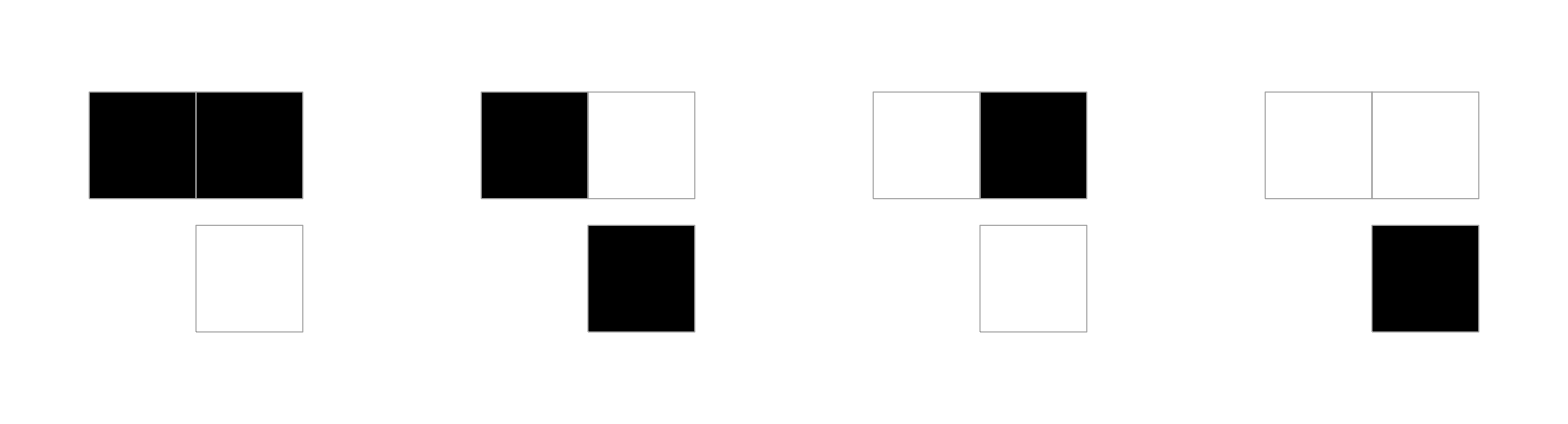
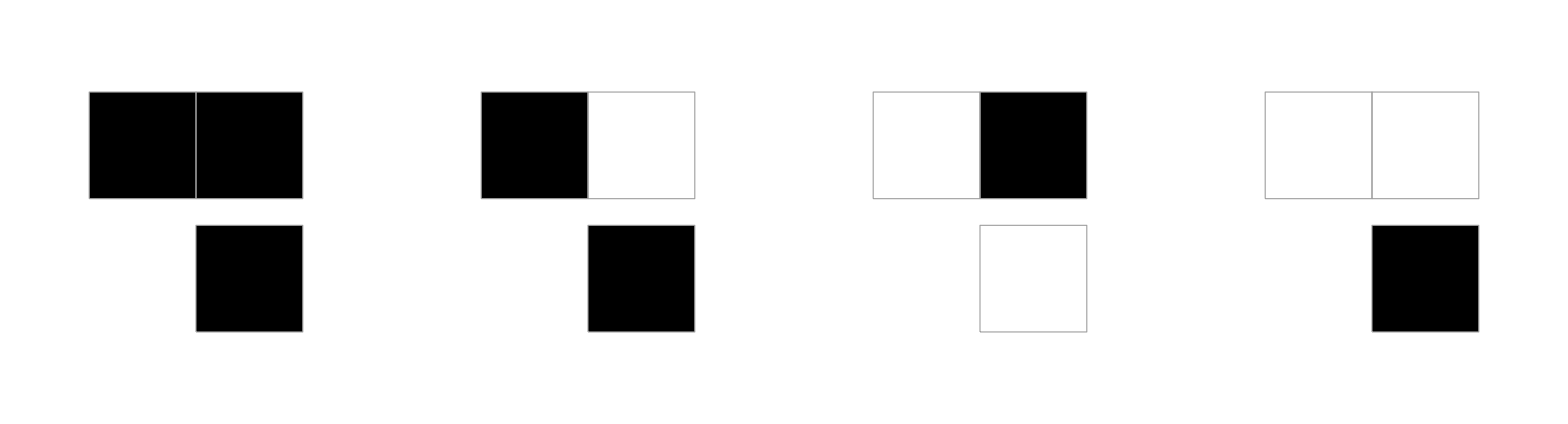
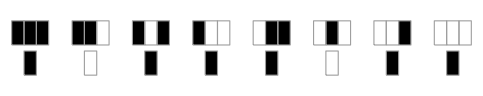

```mathematica
{RulePlot[CellularAutomaton[{5,2,1/2}]],RulePlot[CellularAutomaton[{13,2,1/2}]],RulePlot[CellularAutomaton[{187,2,1}]]}
```